```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
(*alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsNUCLmartinrimas[[All,{1,6,7}]];
a0a1REFERENCE=a0a1NUCLmartinrimas[[All,{8,9}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 (r^2+rp^2)] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

Amat+=(cij (amat+wmat));

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

```mathematica
SolveSecularF[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,c01_?NumberQ,a01_?NumberQ,c02_?NumberQ,a02_?NumberQ,TwoMyOverHBsq_?NumberQ]:=Block[{a00,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

a00={{c01,a01},{c02,a02}};

normsqu=NormTF[a00]^2;

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

Amat+=(cij (amat+wmat));

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nGrid=200;

nf={6,4}; (* number form for printing, only *)
k0FM=0.1;

afit=3.1;rr=25.0; 
αL=Get[LocalObject["3-1_CorePara_SwaveRimas"]];

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV"]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.276473 MeV

S- and P-wave phase shifts

```mathematica
rr=22;nGrid=50;
k0FM=0.05;ErangeMeV=Subdivide[(k0FM hbar)^2/(2 μ),5.0,6];
nn=9;
λ=0.25 activeLEC⟦nn⟧[[1]]^2;C0=activeLEC⟦nn⟧[[2]];D0=activeLEC⟦nn⟧[[3]];
c1=1.0;
α1=2.8;

Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]," ; c_1 = ",NumberForm[c1,nf]," ; α_1 = ",NumberForm[α1,nf]];

a2Range=Subdivide[0.14,1.05,3];
c2Range=Subdivide[-10.15,-0.1,20];
```

λ = Λ^2/4 = 16.0000  ⇒ Λ = 8.0000 ; C_0 = -1898.5500 ; D_0 = 25697 ; c_1 = 1.0000 ; α_1 = 2.8000

```mathematica
tanDsL={};tanDpL={};

Do[

c2=nb;
α2=na α1;
core={{c1,α1},{c2,α2}};

tanDs={};tanDp={};
SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[2 μ energ]/hbar;

TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tnDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]];
tnDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]];
AppendTo[tanDsL,{nb,na,tnDs}];
AppendTo[tanDpL,{nb,na,tnDp}];

Print["ϕ_core += ",NumberForm[nb,nf],"×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=",NumberForm[α2,nf],"  finished."];

,{nb,c2Range},{na,a2Range}]
Put[tanDsL,LocalObject["tanDsL"]]
Put[tanDpL,LocalObject["tanDpL"]]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96786-1.74089×10^-19 ⅈ,1.02006-1.63909×10^-18 ⅈ,0.0177871-4.07185×10^-19 ⅈ,0.0114768-1.7712×10^-18 ⅈ,0.00508898+8.62452×10^-20 ⅈ,0.00106304-8.99247×10^-20 ⅈ,-0.000423169+1.31762×10^-19 ⅈ,-0.000553565+1.87347×10^-20 ⅈ,-0.000323417+4.28025×10^-20 ⅈ,-0.000135069+1.3494×10^-20 ⅈ,-0.0000445497+4.21125×10^-21 ⅈ,-0.0000120689+9.90213×10^-22 ⅈ,-2.7379×10^-6+2.0643×10^-22 ⅈ,«24»,-9.91772×10^-44-1.16791×10^-59 ⅈ,-4.75778×10^-46-1.26528×10^-63 ⅈ,-1.97691×10^-48-2.0554×10^-64 ⅈ,-7.11529×10^-51-6.70872×10^-67 ⅈ,-2.21846×10^-53-1.98524×10^-69 ⅈ,-5.99227×10^-56-4.75862×10^-72 ⅈ,-1.40229×10^-58-2.11286×10^-74 ⅈ,-2.84323×10^-61-3.88978×10^-77 ⅈ,-4.99505×10^-64-6.47378×10^-80 ⅈ,-7.60394×10^-67+2.38734×10^-117 ⅈ,-1.00306×10^-69-1.13947×10^-85 ⅈ,-1.14664×10^-72-1.18386×10^-88 ⅈ,-1.13593×10^-75-1.08681×10^-91 ⅈ},«48»,{-3.2289×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96225-1.6195×10^-19 ⅈ,1.01983-1.62531×10^-18 ⅈ,0.0175379-3.83186×10^-19 ⅈ,0.0112727-1.75432×10^-18 ⅈ,0.00495285+9.62495×10^-20 ⅈ,0.000987238-8.48905×10^-20 ⅈ,-0.000458833+1.33908×10^-19 ⅈ,-0.000567851+1.87369×10^-20 ⅈ,-0.000328313+4.3302×10^-20 ⅈ,-0.000136508+1.36303×10^-20 ⅈ,-0.000044914+4.24333×10^-21 ⅈ,-0.0000121484+9.96735×10^-22 ⅈ,-2.75285×10^-6+2.07576×10^-22 ⅈ,«24»,-9.9234×10^-44-1.16853×10^-59 ⅈ,-4.76036×10^-46-1.26528×10^-63 ⅈ,-1.97793×10^-48-2.05638×10^-64 ⅈ,-7.11878×10^-51-6.71183×10^-67 ⅈ,-2.2195×10^-53-1.9861×10^-69 ⅈ,-5.99493×10^-56-4.76066×10^-72 ⅈ,-1.40288×10^-58-2.11371×10^-74 ⅈ,-2.84439×10^-61-3.89131×10^-77 ⅈ,-4.99698×10^-64-6.47616×10^-80 ⅈ,-7.60676×10^-67+2.38734×10^-117 ⅈ,-1.00342×10^-69-1.13985×10^-85 ⅈ,-1.14703×10^-72-1.18424×10^-88 ⅈ,-1.1363×10^-75-1.08715×10^-91 ⅈ},«48»,{-3.22927×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95664-1.49812×10^-19 ⅈ,1.01959-1.61153×10^-18 ⅈ,0.0172886-3.59186×10^-19 ⅈ,0.0110687-1.73744×10^-18 ⅈ,0.00481673+1.06254×10^-19 ⅈ,0.000911441-7.98563×10^-20 ⅈ,-0.000494497+1.36054×10^-19 ⅈ,-0.000582137+1.87391×10^-20 ⅈ,-0.000333208+4.38014×10^-20 ⅈ,-0.000137948+1.37666×10^-20 ⅈ,-0.0000452782+4.27541×10^-21 ⅈ,-0.0000122278+1.00326×10^-21 ⅈ,-2.7678×10^-6+2.08722×10^-22 ⅈ,«24»,-9.92909×10^-44-1.16916×10^-59 ⅈ,-4.76295×10^-46-1.26528×10^-63 ⅈ,-1.97895×10^-48-2.05736×10^-64 ⅈ,-7.12227×10^-51-6.71493×10^-67 ⅈ,-2.22053×10^-53-1.98695×10^-69 ⅈ,-5.9976×10^-56-4.76271×10^-72 ⅈ,-1.40348×10^-58-2.11456×10^-74 ⅈ,-2.84554×10^-61-3.89284×10^-77 ⅈ,-4.99892×10^-64-6.47855×10^-80 ⅈ,-7.60958×10^-67+2.38734×10^-117 ⅈ,-1.00378×10^-69-1.14022×10^-85 ⅈ,-1.14742×10^-72-1.18463×10^-88 ⅈ,-1.13667×10^-75-1.08749×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95103-1.37673×10^-19 ⅈ,1.01935-1.59775×10^-18 ⅈ,0.0170394-3.35187×10^-19 ⅈ,0.0108647-1.72056×10^-18 ⅈ,0.0046806+1.16258×10^-19 ⅈ,0.000835644-7.48222×10^-20 ⅈ,-0.000530161+1.382×10^-19 ⅈ,-0.000596423+1.87413×10^-20 ⅈ,-0.000338103+4.43009×10^-20 ⅈ,-0.000139388+1.39029×10^-20 ⅈ,-0.0000456425+4.30748×10^-21 ⅈ,-0.0000123072+1.00978×10^-21 ⅈ,-2.78275×10^-6+2.09868×10^-22 ⅈ,«24»,-9.93477×10^-44-1.16979×10^-59 ⅈ,-4.76553×10^-46-1.26528×10^-63 ⅈ,-1.97997×10^-48-2.05833×10^-64 ⅈ,-7.12576×10^-51-6.71804×10^-67 ⅈ,-2.22157×10^-53-1.98781×10^-69 ⅈ,-6.00027×10^-56-4.76476×10^-72 ⅈ,-1.40407×10^-58-2.11541×10^-74 ⅈ,-2.84669×10^-61-3.89436×10^-77 ⅈ,-5.00086×10^-64-6.48093×10^-80 ⅈ,-7.61241×10^-67+2.38734×10^-117 ⅈ,-1.00413×10^-69-1.1406×10^-85 ⅈ,-1.14781×10^-72-1.18501×10^-88 ⅈ,-1.13704×10^-75-1.08783×10^-91 ⅈ},{«1»},«46»,{-«22»-«23» ⅈ,«49»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97908-1.98367×10^-19 ⅈ,1.02053-1.66664×10^-18 ⅈ,0.0182855-4.55184×10^-19 ⅈ,0.0118848-1.80496×10^-18 ⅈ,0.00536124+6.62367×10^-20 ⅈ,0.00121463-9.9993×10^-20 ⅈ,-0.000351841+1.27469×10^-19 ⅈ,-0.000524993+1.87303×10^-20 ⅈ,-0.000313627+4.18036×10^-20 ⅈ,-0.000132189+1.32213×10^-20 ⅈ,-0.0000438211+4.1471×10^-21 ⅈ,-0.00001191+9.77169×10^-22 ⅈ,-2.708×10^-6+2.04138×10^-22 ⅈ,«24»,-9.90636×10^-44-1.16665×10^-59 ⅈ,-4.75261×10^-46-1.26528×10^-63 ⅈ,-1.97487×10^-48-2.05345×10^-64 ⅈ,-7.10831×10^-51-6.70251×10^-67 ⅈ,-2.21639×10^-53-1.98353×10^-69 ⅈ,-5.98693×10^-56-4.75452×10^-72 ⅈ,-1.4011×10^-58-2.11116×10^-74 ⅈ,-2.84093×10^-61-3.88673×10^-77 ⅈ,-4.99117×10^-64-6.46902×10^-80 ⅈ,-7.59829×10^-67+2.38734×10^-117 ⅈ,-1.00235×10^-69-1.13871×10^-85 ⅈ,-1.14586×10^-72-1.18309×10^-88 ⅈ,-1.13518×10^-75-1.08613×10^-91 ⅈ},«48»,{-3.22816×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98421+1.19003×10^-19 ⅈ,0.992026+4.76406×10^-19 ⅈ,-0.0125945+1.38681×10^-18 ⅈ,-0.0136498+7.90047×10^-19 ⅈ,-0.0108559+8.48008×10^-19 ⅈ,-0.00664478+5.95773×10^-19 ⅈ,-0.00328471+3.98458×10^-19 ⅈ,-0.00134966+1.25473×10^-19 ⅈ,-0.000467412+4.80436×10^-20 ⅈ,-0.000137295+1.24146×10^-20 ⅈ,-0.0000342613+2.68727×10^-21 ⅈ,-7.25276×10^-6+8.2647×10^-22 ⅈ,-1.29752×10^-6+1.28602×10^-22 ⅈ,-1.94981×10^-7+6.68102×10^-24 ⅈ,«23»,5.07851×10^-44-4.92269×10^-60 ⅈ,2.50501×10^-46-1.90635×10^-62 ⅈ,1.06796×10^-48-1.67348×10^-64 ⅈ,3.93645×10^-51-2.90867×10^-67 ⅈ,1.2548×10^-53-1.64833×10^-69 ⅈ,3.45995×10^-56-2.26696×10^-74 ⅈ,8.25419×10^-59-9.36383×10^-75 ⅈ,1.70401×10^-61-9.26485×10^-79 ⅈ,3.04461×10^-64-2.84404×10^-80 ⅈ,4.70888×10^-67+8.25361×10^-85 ⅈ,6.30504×10^-70-9.8841×10^-86 ⅈ,7.30959×10^-73-5.39072×10^-89 ⅈ,7.33807×10^-76-4.97046×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96693+1.17845×10^-19 ⅈ,0.992064+4.73763×10^-19 ⅈ,-0.0125327+1.37803×10^-18 ⅈ,-0.0135821+7.83826×10^-19 ⅈ,-0.0107994+8.44371×10^-19 ⅈ,-0.00660699+5.92086×10^-19 ⅈ,-0.00326402+3.95255×10^-19 ⅈ,-0.00134023+1.24289×10^-19 ⅈ,-0.000463798+4.7669×10^-20 ⅈ,-0.000136123+1.23126×10^-20 ⅈ,-0.0000339379+2.66324×10^-21 ⅈ,-7.17657×10^-6+8.16692×10^-22 ⅈ,-1.28214×10^-6+1.26883×10^-22 ⅈ,-1.9232×10^-7+6.68103×10^-24 ⅈ,«23»,5.09036×10^-44-4.93212×10^-60 ⅈ,2.51045×10^-46-1.91034×10^-62 ⅈ,1.07013×10^-48-1.67641×10^-64 ⅈ,3.94395×10^-51-2.91332×10^-67 ⅈ,1.25705×10^-53-1.6509×10^-69 ⅈ,3.46578×10^-56-2.26696×10^-74 ⅈ,8.26733×10^-59-9.37657×10^-75 ⅈ,1.70657×10^-61-9.26485×10^-79 ⅈ,3.04895×10^-64-2.84761×10^-80 ⅈ,4.71525×10^-67+8.25361×10^-85 ⅈ,6.31314×10^-70-9.89543×10^-86 ⅈ,7.31853×10^-73-5.39648×10^-89 ⅈ,7.34661×10^-76-4.97554×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97269+1.18231×10^-19 ⅈ,0.992051+4.74644×10^-19 ⅈ,-0.0125533+1.38096×10^-18 ⅈ,-0.0136046+7.85899×10^-19 ⅈ,-0.0108182+8.45583×10^-19 ⅈ,-0.00661959+5.93315×10^-19 ⅈ,-0.00327091+3.96323×10^-19 ⅈ,-0.00134337+1.24684×10^-19 ⅈ,-0.000465003+4.77939×10^-20 ⅈ,-0.000136513+1.23466×10^-20 ⅈ,-0.0000340457+2.67125×10^-21 ⅈ,-7.20197×10^-6+8.19951×10^-22 ⅈ,-1.28727×10^-6+1.27456×10^-22 ⅈ,-1.93207×10^-7+6.68103×10^-24 ⅈ,«23»,5.08641×10^-44-4.92898×10^-60 ⅈ,2.50864×10^-46-1.90901×10^-62 ⅈ,1.0694×10^-48-1.67544×10^-64 ⅈ,3.94145×10^-51-2.91177×10^-67 ⅈ,1.2563×10^-53-1.65004×10^-69 ⅈ,3.46383×10^-56-2.26696×10^-74 ⅈ,8.26295×10^-59-9.37232×10^-75 ⅈ,1.70572×10^-61-9.26485×10^-79 ⅈ,3.0475×10^-64-2.84642×10^-80 ⅈ,4.71312×10^-67+8.25361×10^-85 ⅈ,6.31044×10^-70-9.89165×10^-86 ⅈ,7.31555×10^-73-5.39456×10^-89 ⅈ,7.34377×10^-76-4.97384×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96117+1.17459×10^-19 ⅈ,0.992077+4.72882×10^-19 ⅈ,-0.012512+1.3751×10^-18 ⅈ,-0.0135595+7.81752×10^-19 ⅈ,-0.0107805+8.43158×10^-19 ⅈ,-0.0065944+5.90857×10^-19 ⅈ,-0.00325712+3.94188×10^-19 ⅈ,-0.00133708+1.23895×10^-19 ⅈ,-0.000462593+4.75441×10^-20 ⅈ,-0.000135732+1.22787×10^-20 ⅈ,-0.00003383+2.65523×10^-21 ⅈ,-7.15117×10^-6+8.13432×10^-22 ⅈ,-1.27702×10^-6+1.2631×10^-22 ⅈ,-1.91432×10^-7+6.68104×10^-24 ⅈ,«23»,5.0943×10^-44-4.93527×10^-60 ⅈ,2.51227×10^-46-1.91167×10^-62 ⅈ,1.07085×10^-48-1.67739×10^-64 ⅈ,3.94645×10^-51-2.91488×10^-67 ⅈ,1.2578×10^-53-1.65175×10^-69 ⅈ,3.46772×10^-56-2.26696×10^-74 ⅈ,8.2717×10^-59-9.38082×10^-75 ⅈ,1.70743×10^-61-9.26485×10^-79 ⅈ,3.05039×10^-64-2.8488×10^-80 ⅈ,4.71737×10^-67+8.25361×10^-85 ⅈ,6.31584×10^-70-9.89921×10^-86 ⅈ,7.32151×10^-73-5.3984×10^-89 ⅈ,7.34946×10^-76-4.97723×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99573+1.19775×10^-19 ⅈ,0.992+4.78167×10^-19 ⅈ,-0.0126358+1.39267×10^-18 ⅈ,-0.013695+7.94195×10^-19 ⅈ,-0.0108937+8.50433×10^-19 ⅈ,-0.00666997+5.98231×10^-19 ⅈ,-0.0032985+4.00592×10^-19 ⅈ,-0.00135595+1.26262×10^-19 ⅈ,-0.000469822+4.82933×10^-20 ⅈ,-0.000138076+1.24825×10^-20 ⅈ,-0.0000344769+2.70329×10^-21 ⅈ,-7.30356×10^-6+8.32989×10^-22 ⅈ,-1.30776×10^-6+1.29748×10^-22 ⅈ,-1.96755×10^-7+6.68102×10^-24 ⅈ,«23»,5.07062×10^-44-4.9164×10^-60 ⅈ,2.50138×10^-46-1.90369×10^-62 ⅈ,1.06651×10^-48-1.67153×10^-64 ⅈ,3.93145×10^-51-2.90556×10^-67 ⅈ,1.25331×10^-53-1.64661×10^-69 ⅈ,3.45606×10^-56-2.26696×10^-74 ⅈ,8.24544×10^-59-9.35533×10^-75 ⅈ,1.7023×10^-61-9.26485×10^-79 ⅈ,3.04172×10^-64-2.84165×10^-80 ⅈ,4.70464×10^-67+8.25361×10^-85 ⅈ,6.29964×10^-70-9.87654×10^-86 ⅈ,7.30364×10^-73-5.38687×10^-89 ⅈ,7.33237×10^-76-4.96707×10^-92 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97347-1.86228×10^-19 ⅈ,1.0203-1.65286×10^-18 ⅈ,0.0180363-4.31184×10^-19 ⅈ,0.0116808-1.78808×10^-18 ⅈ,0.00522511+7.6241×10^-20 ⅈ,0.00113883-9.49589×10^-20 ⅈ,-0.000387505+1.29615×10^-19 ⅈ,-0.000539279+1.87325×10^-20 ⅈ,-0.000318522+4.23031×10^-20 ⅈ,-0.000133629+1.33577×10^-20 ⅈ,-0.0000441854+4.17917×10^-21 ⅈ,-0.0000119895+9.83691×10^-22 ⅈ,-2.72295×10^-6+2.05284×10^-22 ⅈ,«24»,-9.91204×10^-44-1.16728×10^-59 ⅈ,-4.75519×10^-46-1.26528×10^-63 ⅈ,-1.97589×10^-48-2.05443×10^-64 ⅈ,-7.1118×10^-51-6.70562×10^-67 ⅈ,-2.21742×10^-53-1.98438×10^-69 ⅈ,-5.9896×10^-56-4.75657×10^-72 ⅈ,-1.40169×10^-58-2.11201×10^-74 ⅈ,-2.84208×10^-61-3.88825×10^-77 ⅈ,-4.99311×10^-64-6.4714×10^-80 ⅈ,-7.60111×10^-67+2.38734×10^-117 ⅈ,-1.00271×10^-69-1.13909×10^-85 ⅈ,-1.14625×10^-72-1.18348×10^-88 ⅈ,-1.13555×10^-75-1.08647×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -10.1500×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -10.1500×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -10.1500×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -10.1500×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96786-1.6935×10^-19 ⅈ,1.02007-1.64307×10^-18 ⅈ,0.0178127-4.08268×10^-19 ⅈ,0.0115053-1.77552×10^-18 ⅈ,0.00511101+8.60506×10^-20 ⅈ,0.00107507-8.9099×10^-20 ⅈ,-0.000418668+1.31949×10^-19 ⅈ,-0.00055253+1.8907×10^-20 ⅈ,-0.000323371+4.28549×10^-20 ⅈ,-0.000135146+1.35196×10^-20 ⅈ,-0.0000445906+4.21744×10^-21 ⅈ,-0.0000120821+9.91609×10^-22 ⅈ,-2.7411×10^-6+2.06683×10^-22 ⅈ,«24»,-9.92987×10^-44-1.16934×10^-59 ⅈ,-4.76361×10^-46-1.26683×10^-63 ⅈ,-1.97933×10^-48-2.05792×10^-64 ⅈ,-7.12401×10^-51-6.71694×10^-67 ⅈ,-2.22118×10^-53-1.98767×10^-69 ⅈ,-5.99961×10^-56-4.76445×10^-72 ⅈ,-1.40401×10^-58-2.11545×10^-74 ⅈ,-2.84672×10^-61-3.89455×10^-77 ⅈ,-5.00116×10^-64-6.48171×10^-80 ⅈ,-7.61325×10^-67+2.39034×10^-117 ⅈ,-1.00429×10^-69-1.14086×10^-85 ⅈ,-1.14804×10^-72-1.18531×10^-88 ⅈ,-1.13732×10^-75-1.08814×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94542-1.20776×10^-19 ⅈ,1.01913-1.58795×10^-18 ⅈ,0.0168151-3.12192×10^-19 ⅈ,0.0106885-1.70794×10^-18 ⅈ,0.004566+1.26117×10^-19 ⅈ,0.000771582-6.89327×10^-20 ⅈ,-0.000561477+1.40544×10^-19 ⅈ,-0.000609739+1.89162×10^-20 ⅈ,-0.000342975+4.48552×10^-20 ⅈ,-0.000140912+1.40656×10^-20 ⅈ,-0.0000460496+4.34591×10^-21 ⅈ,-0.0000124002+1.01773×10^-21 ⅈ,-2.80098×10^-6+2.11273×10^-22 ⅈ,«24»,-9.95263×10^-44-1.17186×10^-59 ⅈ,-4.77396×10^-46-1.26683×10^-63 ⅈ,-1.98342×10^-48-2.06183×10^-64 ⅈ,-7.13799×10^-51-6.72938×10^-67 ⅈ,-2.22533×10^-53-1.9911×10^-69 ⅈ,-6.01029×10^-56-4.77265×10^-72 ⅈ,-1.40639×10^-58-2.11885×10^-74 ⅈ,-2.85134×10^-61-3.90067×10^-77 ⅈ,-5.00893×10^-64-6.49125×10^-80 ⅈ,-7.62456×10^-67+2.39034×10^-117 ⅈ,-1.00572×10^-69-1.14238×10^-85 ⅈ,-1.14961×10^-72-1.18685×10^-88 ⅈ,-1.13881×10^-75-1.0895×10^-91 ⅈ},«48»,{-3.23435×10^-75-«23» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97908-1.93637×10^-19 ⅈ,1.02054-1.67063×10^-18 ⅈ,0.0183115-4.56306×10^-19 ⅈ,0.0119137-1.80931×10^-18 ⅈ,0.00538352+6.60176×10^-20 ⅈ,0.00122682-9.91822×10^-20 ⅈ,-0.000347263+1.27651×10^-19 ⅈ,-0.000523926+1.89023×10^-20 ⅈ,-0.000313569+4.18548×10^-20 ⅈ,-0.000132263+1.32467×10^-20 ⅈ,-0.0000438612+4.15321×10^-21 ⅈ,-0.000011923+9.78548×10^-22 ⅈ,-2.71117×10^-6+2.04389×10^-22 ⅈ,«24»,-9.9185×10^-44-1.16808×10^-59 ⅈ,-4.75843×10^-46-1.26683×10^-63 ⅈ,-1.97729×10^-48-2.05597×10^-64 ⅈ,-7.11702×10^-51-6.71072×10^-67 ⅈ,-2.2191×10^-53-1.98596×10^-69 ⅈ,-5.99427×10^-56-4.76034×10^-72 ⅈ,-1.40281×10^-58-2.11375×10^-74 ⅈ,-2.84441×10^-61-3.89149×10^-77 ⅈ,-4.99728×10^-64-6.47694×10^-80 ⅈ,-7.6076×10^-67+2.39034×10^-117 ⅈ,-1.00358×10^-69-1.14011×10^-85 ⅈ,-1.14726×10^-72-1.18454×10^-88 ⅈ,-1.13657×10^-75-1.08747×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95664-1.45063×10^-19 ⅈ,1.0196-1.61551×10^-18 ⅈ,0.0173139-3.6023×10^-19 ⅈ,0.0110969-1.74173×10^-18 ⅈ,0.00483851+1.06084×10^-19 ⅈ,0.000923327-7.90159×10^-20 ⅈ,-0.000490072+1.36246×10^-19 ⅈ,-0.000581135+1.89116×10^-20 ⅈ,-0.000333173+4.3855×10^-20 ⅈ,-0.000138029+1.37926×10^-20 ⅈ,-0.0000453201+4.28168×10^-21 ⅈ,-0.0000122411+1.00467×10^-21 ⅈ,-2.77104×10^-6+2.08978×10^-22 ⅈ,«24»,-9.94125×10^-44-1.1706×10^-59 ⅈ,-4.76878×10^-46-1.26683×10^-63 ⅈ,-1.98137×10^-48-2.05988×10^-64 ⅈ,-7.131×10^-51-6.72316×10^-67 ⅈ,-2.22325×10^-53-1.98939×10^-69 ⅈ,-6.00495×10^-56-4.76855×10^-72 ⅈ,-1.4052×10^-58-2.11715×10^-74 ⅈ,-2.84903×10^-61-3.89761×10^-77 ⅈ,-5.00505×10^-64-6.48648×10^-80 ⅈ,-7.61891×10^-67+2.39034×10^-117 ⅈ,-1.00501×10^-69-1.14162×10^-85 ⅈ,-1.14883×10^-72-1.18608×10^-88 ⅈ,-1.13806×10^-75-1.08882×10^-91 ⅈ},«48»,{-3.2336×10^-75-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95103-1.32919×10^-19 ⅈ,1.01936-1.60173×10^-18 ⅈ,0.0170645-3.36211×10^-19 ⅈ,0.0108927-1.72484×10^-18 ⅈ,0.00470226+1.161×10^-19 ⅈ,0.000847454-7.39743×10^-20 ⅈ,-0.000525774+1.38395×10^-19 ⅈ,-0.000595437+1.89139×10^-20 ⅈ,-0.000338074+4.43551×10^-20 ⅈ,-0.00013947+1.39291×10^-20 ⅈ,-0.0000456848+4.3138×10^-21 ⅈ,-0.0000123207+1.0112×10^-21 ⅈ,-2.78601×10^-6+2.10126×10^-22 ⅈ,«24»,-9.94694×10^-44-1.17123×10^-59 ⅈ,-4.77137×10^-46-1.26683×10^-63 ⅈ,-1.9824×10^-48-2.06086×10^-64 ⅈ,-7.13449×10^-51-6.72627×10^-67 ⅈ,-2.22429×10^-53-1.99024×10^-69 ⅈ,-6.00762×10^-56-4.7706×10^-72 ⅈ,-1.40579×10^-58-2.118×10^-74 ⅈ,-2.85018×10^-61-3.89914×10^-77 ⅈ,-5.00699×10^-64-6.48887×10^-80 ⅈ,-7.62173×10^-67+2.39034×10^-117 ⅈ,-1.00536×10^-69-1.142×10^-85 ⅈ,-1.14922×10^-72-1.18646×10^-88 ⅈ,-1.13844×10^-75-1.08916×10^-91 ⅈ},«48»,{-3.23398×10^-75-«23» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97843+1.17369×10^-19 ⅈ,0.992055+4.74798×10^-19 ⅈ,-0.012567+1.38236×10^-18 ⅈ,-0.0136309+7.8771×10^-19 ⅈ,-0.0108468+8.47923×10^-19 ⅈ,-0.00664124+5.95728×10^-19 ⅈ,-0.00328314+3.9805×10^-19 ⅈ,-0.00134881+1.25239×10^-19 ⅈ,-0.00046698+4.79752×10^-20 ⅈ,-0.000137117+1.2403×10^-20 ⅈ,-0.0000342031+2.68338×10^-21 ⅈ,-7.23722×10^-6+8.24372×10^-22 ⅈ,-1.29408×10^-6+1.28196×10^-22 ⅈ,-1.94339×10^-7+6.68974×10^-24 ⅈ,«23»,5.08869×10^-44-4.93187×10^-60 ⅈ,2.50989×10^-46-1.91002×10^-62 ⅈ,1.06999×10^-48-1.67651×10^-64 ⅈ,3.94377×10^-51-2.91378×10^-67 ⅈ,1.25709×10^-53-1.6512×10^-69 ⅈ,3.46613×10^-56-2.26973×10^-74 ⅈ,8.26869×10^-59-9.37955×10^-75 ⅈ,1.70695×10^-61-9.2762×10^-79 ⅈ,3.04979×10^-64-2.84871×10^-80 ⅈ,4.71677×10^-67+8.26372×10^-85 ⅈ,6.31546×10^-70-9.89999×10^-86 ⅈ,7.32153×10^-73-5.39924×10^-89 ⅈ,7.34991×10^-76-4.97824×10^-92 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96116+1.16209×10^-19 ⅈ,0.992094+4.72151×10^-19 ⅈ,-0.0125052+1.37358×10^-18 ⅈ,-0.0135632+7.81488×10^-19 ⅈ,-0.0107902+8.44288×10^-19 ⅈ,-0.00660344+5.9204×10^-19 ⅈ,-0.00326243+3.94845×10^-19 ⅈ,-0.00133937+1.24054×10^-19 ⅈ,-0.000463362+4.76001×10^-20 ⅈ,-0.000135944+1.2301×10^-20 ⅈ,-0.0000338793+2.65932×10^-21 ⅈ,-7.16094×10^-6+8.14582×10^-22 ⅈ,-1.27869×10^-6+1.26475×10^-22 ⅈ,-1.91675×10^-7+6.68975×10^-24 ⅈ,«23»,5.10054×10^-44-4.94132×10^-60 ⅈ,2.51534×10^-46-1.91402×10^-62 ⅈ,1.07216×10^-48-1.67944×10^-64 ⅈ,3.95128×10^-51-2.91845×10^-67 ⅈ,1.25934×10^-53-1.65378×10^-69 ⅈ,3.47197×10^-56-2.26973×10^-74 ⅈ,8.28184×10^-59-9.39231×10^-75 ⅈ,1.70952×10^-61-9.2762×10^-79 ⅈ,3.05413×10^-64-2.85229×10^-80 ⅈ,4.72315×10^-67+8.26372×10^-85 ⅈ,6.32357×10^-70-9.91134×10^-86 ⅈ,7.33048×10^-73-5.40501×10^-89 ⅈ,7.35847×10^-76-4.98333×10^-92 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99571+1.18529×10^-19 ⅈ,0.992017+4.77444×10^-19 ⅈ,-0.0126288+1.39115×10^-18 ⅈ,-0.0136986+7.93932×10^-19 ⅈ,-0.0109034+8.51559×10^-19 ⅈ,-0.00667905+5.99415×10^-19 ⅈ,-0.00330385+4.01255×10^-19 ⅈ,-0.00135825+1.26424×10^-19 ⅈ,-0.000470599+4.83502×10^-20 ⅈ,-0.000138291+1.25051×10^-20 ⅈ,-0.0000345269+2.70744×10^-21 ⅈ,-7.31351×10^-6+8.34162×10^-22 ⅈ,-1.30947×10^-6+1.29917×10^-22 ⅈ,-1.97004×10^-7+6.68973×10^-24 ⅈ,«23»,5.07683×10^-44-4.92242×10^-60 ⅈ,2.50444×10^-46-1.90602×10^-62 ⅈ,1.06782×10^-48-1.67358×10^-64 ⅈ,3.93627×10^-51-2.90912×10^-67 ⅈ,1.25484×10^-53-1.64863×10^-69 ⅈ,3.46029×10^-56-2.26973×10^-74 ⅈ,8.25554×10^-59-9.36679×10^-75 ⅈ,1.70438×10^-61-9.2762×10^-79 ⅈ,3.04544×10^-64-2.84513×10^-80 ⅈ,4.7104×10^-67+8.26372×10^-85 ⅈ,6.30735×10^-70-9.88864×10^-86 ⅈ,7.31259×10^-73-5.39347×10^-89 ⅈ,7.34135×10^-76-4.97315×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98419+1.17756×10^-19 ⅈ,0.992042+4.7568×10^-19 ⅈ,-0.0125876+1.38529×10^-18 ⅈ,-0.0136534+7.89784×10^-19 ⅈ,-0.0108656+8.49135×10^-19 ⅈ,-0.00665384+5.96957×10^-19 ⅈ,-0.00329005+3.99118×10^-19 ⅈ,-0.00135195+1.25634×10^-19 ⅈ,-0.000468187+4.81002×10^-20 ⅈ,-0.000137509+1.2437×10^-20 ⅈ,-0.000034311+2.6914×10^-21 ⅈ,-7.26265×10^-6+8.27635×10^-22 ⅈ,-1.29921×10^-6+1.2877×10^-22 ⅈ,-1.95228×10^-7+6.68973×10^-24 ⅈ,«23»,5.08473×10^-44-4.92872×10^-60 ⅈ,2.50808×10^-46-1.90869×10^-62 ⅈ,1.06927×10^-48-1.67553×10^-64 ⅈ,3.94127×10^-51-2.91223×10^-67 ⅈ,1.25634×10^-53-1.65035×10^-69 ⅈ,3.46418×10^-56-2.26973×10^-74 ⅈ,8.26431×10^-59-9.3753×10^-75 ⅈ,1.7061×10^-61-9.2762×10^-79 ⅈ,3.04834×10^-64-2.84752×10^-80 ⅈ,4.71465×10^-67+8.26372×10^-85 ⅈ,6.31276×10^-70-9.89621×10^-86 ⅈ,7.31855×10^-73-5.39732×10^-89 ⅈ,7.34706×10^-76-4.97655×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97267+1.16982×10^-19 ⅈ,0.992068+4.73916×10^-19 ⅈ,-0.0125464+1.37944×10^-18 ⅈ,-0.0136083+7.85636×10^-19 ⅈ,-0.0108279+8.46711×10^-19 ⅈ,-0.00662864+5.94498×10^-19 ⅈ,-0.00327624+3.96981×10^-19 ⅈ,-0.00134566+1.24844×10^-19 ⅈ,-0.000465774+4.78502×10^-20 ⅈ,-0.000136726+1.2369×10^-20 ⅈ,-0.0000340951+2.67536×10^-21 ⅈ,-7.2118×10^-6+8.21108×10^-22 ⅈ,-1.28895×10^-6+1.27622×10^-22 ⅈ,-1.93451×10^-7+6.68974×10^-24 ⅈ,«23»,5.09264×10^-44-4.93502×10^-60 ⅈ,2.51171×10^-46-1.91135×10^-62 ⅈ,1.07071×10^-48-1.67749×10^-64 ⅈ,3.94628×10^-51-2.91534×10^-67 ⅈ,1.25784×10^-53-1.65206×10^-69 ⅈ,3.46808×10^-56-2.26973×10^-74 ⅈ,8.27307×10^-59-9.38381×10^-75 ⅈ,1.70781×10^-61-9.2762×10^-79 ⅈ,3.05123×10^-64-2.84991×10^-80 ⅈ,4.7189×10^-67+8.26372×10^-85 ⅈ,6.31817×10^-70-9.90377×10^-86 ⅈ,7.32451×10^-73-5.40117×10^-89 ⅈ,7.35276×10^-76-4.97994×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97347-1.81493×10^-19 ⅈ,1.02031-1.65685×10^-18 ⅈ,0.0180621-4.32287×10^-19 ⅈ,0.0117095-1.79242×10^-18 ⅈ,0.00524727+7.60341×10^-20 ⅈ,0.00115095-9.41406×10^-20 ⅈ,-0.000382966+1.298×10^-19 ⅈ,-0.000538228+1.89047×10^-20 ⅈ,-0.00031847+4.23548×10^-20 ⅈ,-0.000133705+1.33831×10^-20 ⅈ,-0.0000442259+4.18533×10^-21 ⅈ,-0.0000120025+9.85078×10^-22 ⅈ,-2.72613×10^-6+2.05536×10^-22 ⅈ,«24»,-9.92418×10^-44-1.16871×10^-59 ⅈ,-4.76102×10^-46-1.26683×10^-63 ⅈ,-1.97831×10^-48-2.05695×10^-64 ⅈ,-7.12051×10^-51-6.71383×10^-67 ⅈ,-2.22014×10^-53-1.98681×10^-69 ⅈ,-5.99694×10^-56-4.7624×10^-72 ⅈ,-1.40341×10^-58-2.1146×10^-74 ⅈ,-2.84556×10^-61-3.89302×10^-77 ⅈ,-4.99922×10^-64-6.47933×10^-80 ⅈ,-7.61042×10^-67+2.39034×10^-117 ⅈ,-1.00393×10^-69-1.14049×10^-85 ⅈ,-1.14765×10^-72-1.18493×10^-88 ⅈ,-1.13695×10^-75-1.0878×10^-91 ⅈ},«48»,{-3.23249×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -9.6475×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -9.6475×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -9.6475×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -9.6475×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95665-1.39785×10^-19 ⅈ,1.01961-1.61993×10^-18 ⅈ,0.017342-3.61389×10^-19 ⅈ,0.0111283-1.7465×10^-18 ⅈ,0.00486273+1.05894×10^-19 ⅈ,0.00093655-7.80803×10^-20 ⅈ,-0.000485147+1.3646×10^-19 ⅈ,-0.000580017+1.91034×10^-20 ⅈ,-0.000333133+4.39145×10^-20 ⅈ,-0.000138119+1.38215×10^-20 ⅈ,-0.0000453665+4.28864×10^-21 ⅈ,-0.0000122559+1.00624×10^-21 ⅈ,-2.77463×10^-6+2.09263×10^-22 ⅈ,«24»,-9.95475×10^-44-1.17219×10^-59 ⅈ,-4.77526×10^-46-1.26855×10^-63 ⅈ,-1.98407×10^-48-2.06268×10^-64 ⅈ,-7.14068×10^-51-6.73229×10^-67 ⅈ,-2.22627×10^-53-1.99209×10^-69 ⅈ,-6.01311×10^-56-4.77503×10^-72 ⅈ,-1.40711×10^-58-2.12003×10^-74 ⅈ,-2.8529×10^-61-3.9029×10^-77 ⅈ,-5.01184×10^-64-6.49529×10^-80 ⅈ,-7.62925×10^-67+2.39366×10^-117 ⅈ,-1.00637×10^-69-1.14317×10^-85 ⅈ,-1.15039×10^-72-1.18769×10^-88 ⅈ,-1.13961×10^-75-1.0903×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94542-1.15488×10^-19 ⅈ,1.01914-1.59237×10^-18 ⅈ,0.0168427-3.13308×10^-19 ⅈ,0.0107196-1.71268×10^-18 ⅈ,0.00458995+1.25954×10^-19 ⅈ,0.000784637-6.79808×10^-20 ⅈ,-0.000556636+1.40764×10^-19 ⅈ,-0.000608657+1.91083×10^-20 ⅈ,-0.000342948+4.4916×10^-20 ⅈ,-0.000141005+1.40948×10^-20 ⅈ,-0.000046097+4.35297×10^-21 ⅈ,-0.0000124152+1.01931×10^-21 ⅈ,-2.80461×10^-6+2.11561×10^-22 ⅈ,«24»,-9.96615×10^-44-1.17345×10^-59 ⅈ,-4.78044×10^-46-1.26855×10^-63 ⅈ,-1.98611×10^-48-2.06463×10^-64 ⅈ,-7.14768×10^-51-6.73852×10^-67 ⅈ,-2.22835×10^-53-1.99381×10^-69 ⅈ,-6.01846×10^-56-4.77913×10^-72 ⅈ,-1.4083×10^-58-2.12173×10^-74 ⅈ,-2.85521×10^-61-3.90596×10^-77 ⅈ,-5.01573×10^-64-6.50007×10^-80 ⅈ,-7.63492×10^-67+2.39366×10^-117 ⅈ,-1.00709×10^-69-1.14393×10^-85 ⅈ,-1.15117×10^-72-1.18846×10^-88 ⅈ,-1.14035×10^-75-1.09098×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97266+1.15598×10^-19 ⅈ,0.992086+4.73107×10^-19 ⅈ,-0.0125387+1.37774×10^-18 ⅈ,-0.0136123+7.85341×10^-19 ⅈ,-0.0108387+8.47964×10^-19 ⅈ,-0.00663869+5.95814×10^-19 ⅈ,-0.00328216+3.97713×10^-19 ⅈ,-0.0013482+1.25021×10^-19 ⅈ,-0.000466632+4.79127×10^-20 ⅈ,-0.000136963+1.23939×10^-20 ⅈ,-0.0000341501+2.67993×10^-21 ⅈ,-7.22271×10^-6+8.22393×10^-22 ⅈ,-1.29081×10^-6+1.27807×10^-22 ⅈ,-1.93723×10^-7+6.69941×10^-24 ⅈ,«23»,5.09956×10^-44-4.94172×10^-60 ⅈ,2.51512×10^-46-1.91395×10^-62 ⅈ,1.07217×10^-48-1.67977×10^-64 ⅈ,3.95164×10^-51-2.9193×10^-67 ⅈ,1.25955×10^-53-1.65431×10^-69 ⅈ,3.47279×10^-56-2.27282×10^-74 ⅈ,8.28431×10^-59-9.39655×10^-75 ⅈ,1.71013×10^-61-9.2888×10^-79 ⅈ,3.05538×10^-64-2.85378×10^-80 ⅈ,4.72531×10^-67+8.27495×10^-85 ⅈ,6.32675×10^-70-9.91722×10^-86 ⅈ,7.33446×10^-73-5.4085×10^-89 ⅈ,7.36275×10^-76-4.9867×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97841+1.15985×10^-19 ⅈ,0.992074+4.7399×10^-19 ⅈ,-0.0125593+1.38067×10^-18 ⅈ,-0.0136349+7.87414×10^-19 ⅈ,-0.0108575+8.49175×10^-19 ⅈ,-0.0066513+5.97043×10^-19 ⅈ,-0.00328906+3.98782×10^-19 ⅈ,-0.00135135+1.25417×10^-19 ⅈ,-0.000467839+4.80379×10^-20 ⅈ,-0.000137355+1.24279×10^-20 ⅈ,-0.0000342582+2.68796×10^-21 ⅈ,-7.24817×10^-6+8.25661×10^-22 ⅈ,-1.29595×10^-6+1.28382×10^-22 ⅈ,-1.94612×10^-7+6.69941×10^-24 ⅈ,«23»,5.0956×10^-44-4.93857×10^-60 ⅈ,2.5133×10^-46-1.91261×10^-62 ⅈ,1.07144×10^-48-1.67879×10^-64 ⅈ,3.94913×10^-51-2.91774×10^-67 ⅈ,1.2588×10^-53-1.65345×10^-69 ⅈ,3.47084×10^-56-2.27282×10^-74 ⅈ,8.27992×10^-59-9.39229×10^-75 ⅈ,1.70927×10^-61-9.2888×10^-79 ⅈ,3.05393×10^-64-2.85258×10^-80 ⅈ,4.72318×10^-67+8.27495×10^-85 ⅈ,6.32404×10^-70-9.91344×10^-86 ⅈ,7.33148×10^-73-5.40658×10^-89 ⅈ,7.35989×10^-76-4.985×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96114+1.14823×10^-19 ⅈ,0.992112+4.71341×10^-19 ⅈ,-0.0124975+1.37189×10^-18 ⅈ,-0.0135672+7.81193×10^-19 ⅈ,-0.0108009+8.45541×10^-19 ⅈ,-0.00661348+5.93354×10^-19 ⅈ,-0.00326834+3.95574×10^-19 ⅈ,-0.0013419+1.2423×10^-19 ⅈ,-0.000464217+4.76623×10^-20 ⅈ,-0.00013618+1.23258×10^-20 ⅈ,-0.0000339339+2.66387×10^-21 ⅈ,-7.17178×10^-6+8.15858×10^-22 ⅈ,-1.28053×10^-6+1.26658×10^-22 ⅈ,-1.91944×10^-7+6.69942×10^-24 ⅈ,«23»,5.10747×10^-44-4.94803×10^-60 ⅈ,2.51876×10^-46-1.91662×10^-62 ⅈ,1.07362×10^-48-1.68172×10^-64 ⅈ,3.95665×10^-51-2.92241×10^-67 ⅈ,1.26105×10^-53-1.65602×10^-69 ⅈ,3.47669×10^-56-2.27282×10^-74 ⅈ,8.29309×10^-59-9.40507×10^-75 ⅈ,1.71184×10^-61-9.2888×10^-79 ⅈ,3.05828×10^-64-2.85617×10^-80 ⅈ,4.72956×10^-67+8.27495×10^-85 ⅈ,6.33216×10^-70-9.9248×10^-86 ⅈ,7.34044×10^-73-5.41235×10^-89 ⅈ,7.36846×10^-76-4.9901×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99569+1.17146×10^-19 ⅈ,0.992035+4.7664×10^-19 ⅈ,-0.012621+1.38944×10^-18 ⅈ,-0.0137026+7.93636×10^-19 ⅈ,-0.0109141+8.52809×10^-19 ⅈ,-0.00668912+6.00732×10^-19 ⅈ,-0.00330979+4.01991×10^-19 ⅈ,-0.0013608+1.26604×10^-19 ⅈ,-0.000471461+4.84134×10^-20 ⅈ,-0.00013853+1.25301×10^-20 ⅈ,-0.0000345824+2.71205×10^-21 ⅈ,-7.32456×10^-6+8.35464×10^-22 ⅈ,-1.31136×10^-6+1.30105×10^-22 ⅈ,-1.9728×10^-7+6.6994×10^-24 ⅈ,«23»,5.08373×10^-44-4.92911×10^-60 ⅈ,2.50784×10^-46-1.90861×10^-62 ⅈ,1.06927×10^-48-1.67585×10^-64 ⅈ,3.94161×10^-51-2.91307×10^-67 ⅈ,1.25655×10^-53-1.65087×10^-69 ⅈ,3.46499×10^-56-2.27282×10^-74 ⅈ,8.26676×10^-59-9.37952×10^-75 ⅈ,1.7067×10^-61-9.2888×10^-79 ⅈ,3.04958×10^-64-2.849×10^-80 ⅈ,4.7168×10^-67+8.27495×10^-85 ⅈ,6.31592×10^-70-9.90207×10^-86 ⅈ,7.32252×10^-73-5.4008×10^-89 ⅈ,7.35132×10^-76-4.97991×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98417+1.16372×10^-19 ⅈ,0.992061+4.74874×10^-19 ⅈ,-0.0125798+1.38359×10^-18 ⅈ,-0.0136575+7.89488×10^-19 ⅈ,-0.0108764+8.50386×10^-19 ⅈ,-0.00666391+5.98273×10^-19 ⅈ,-0.00329597+3.99852×10^-19 ⅈ,-0.0013545+1.25813×10^-19 ⅈ,-0.000469047+4.8163×10^-20 ⅈ,-0.000137746+1.2462×10^-20 ⅈ,-0.0000343662+2.69599×10^-21 ⅈ,-7.27364×10^-6+8.28929×10^-22 ⅈ,-1.30108×10^-6+1.28956×10^-22 ⅈ,-1.95501×10^-7+6.69941×10^-24 ⅈ,«23»,5.09164×10^-44-4.93541×10^-60 ⅈ,2.51148×10^-46-1.91128×10^-62 ⅈ,1.07072×10^-48-1.67781×10^-64 ⅈ,3.94662×10^-51-2.91619×10^-67 ⅈ,1.25805×10^-53-1.65259×10^-69 ⅈ,3.46889×10^-56-2.27282×10^-74 ⅈ,8.27553×10^-59-9.38804×10^-75 ⅈ,1.70841×10^-61-9.2888×10^-79 ⅈ,3.05248×10^-64-2.85139×10^-80 ⅈ,4.72105×10^-67+8.27495×10^-85 ⅈ,6.32134×10^-70-9.90965×10^-86 ⅈ,7.32849×10^-73-5.40465×10^-89 ⅈ,7.35704×10^-76-4.98331×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -9.1450×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -9.1450×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -9.1450×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -9.1450×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97909-1.82502×10^-19 ⅈ,1.02056-1.67998×10^-18 ⅈ,0.0183726-4.5894×10^-19 ⅈ,0.0119818-1.81956×10^-18 ⅈ,0.00543601+6.55001×10^-20 ⅈ,0.00125555-9.72686×10^-20 ⅈ,-0.000336463+1.28079×10^-19 ⅈ,-0.000521403+1.93078×10^-20 ⅈ,-0.00031343+4.19749×10^-20 ⅈ,-0.000132436+1.33062×10^-20 ⅈ,-0.0000439552+4.16758×10^-21 ⅈ,-0.0000119534+9.81791×10^-22 ⅈ,-2.71859×10^-6+2.04978×10^-22 ⅈ,«24»,-9.94701×10^-44-1.17143×10^-59 ⅈ,-4.77211×10^-46-1.27048×10^-63 ⅈ,-1.98297×10^-48-2.06188×10^-64 ⅈ,-7.13748×10^-51-6.73001×10^-67 ⅈ,-2.22548×10^-53-1.99167×10^-69 ⅈ,-6.0115×10^-56-4.77403×10^-72 ⅈ,-1.40685×10^-58-2.11983×10^-74 ⅈ,-2.85258×10^-61-3.90267×10^-77 ⅈ,-5.01165×10^-64-6.49556×10^-80 ⅈ,-7.62947×10^-67+2.39737×10^-117 ⅈ,-1.00646×10^-69-1.14339×10^-85 ⅈ,-1.15056×10^-72-1.18795×10^-88 ⅈ,-1.13984×10^-75-1.09059×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96226-1.4604×10^-19 ⅈ,1.01986-1.63864×10^-18 ⅈ,0.0176231-3.86747×10^-19 ⅈ,0.011368-1.76876×10^-18 ⅈ,0.00502637+9.5636×10^-20 ⅈ,0.0010274-8.20917×10^-20 ⅈ,-0.000443838+1.34544×10^-19 ⅈ,-0.000564423+1.93156×10^-20 ⅈ,-0.000328173+4.34794×10^-20 ⅈ,-0.000136773+1.37169×10^-20 ⅈ,-0.0000450525+4.26421×10^-21 ⅈ,-0.0000121927+1.00144×10^-21 ⅈ,-2.76363×10^-6+2.0843×10^-22 ⅈ,«24»,-9.96413×10^-44-1.17333×10^-59 ⅈ,-4.7799×10^-46-1.27048×10^-63 ⅈ,-1.98605×10^-48-2.06482×10^-64 ⅈ,-7.14799×10^-51-6.73937×10^-67 ⅈ,-2.2286×10^-53-1.99425×10^-69 ⅈ,-6.01954×10^-56-4.7802×10^-72 ⅈ,-1.40864×10^-58-2.12239×10^-74 ⅈ,-2.85606×10^-61-3.90728×10^-77 ⅈ,-5.01749×10^-64-6.50274×10^-80 ⅈ,-7.63797×10^-67+2.39737×10^-117 ⅈ,-1.00754×10^-69-1.14452×10^-85 ⅈ,-1.15174×10^-72-1.1891×10^-88 ⅈ,-1.14096×10^-75-1.09161×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95665-1.33885×10^-19 ⅈ,1.01962-1.62486×10^-18 ⅈ,0.0173733-3.62682×10^-19 ⅈ,0.0111634-1.75183×10^-18 ⅈ,0.00488983+1.05681×10^-19 ⅈ,0.000951349-7.70327×10^-20 ⅈ,-0.00047963+1.36699×10^-19 ⅈ,-0.000578763+1.93182×10^-20 ⅈ,-0.000333087+4.39809×10^-20 ⅈ,-0.000138218+1.38538×10^-20 ⅈ,-0.0000454183+4.29642×10^-21 ⅈ,-0.0000122725+1.00799×10^-21 ⅈ,-2.77864×10^-6+2.09581×10^-22 ⅈ,«24»,-9.96983×10^-44-1.17396×10^-59 ⅈ,-4.78249×10^-46-1.27048×10^-63 ⅈ,-1.98707×10^-48-2.0658×10^-64 ⅈ,-7.1515×10^-51-6.74249×10^-67 ⅈ,-2.22964×10^-53-1.99511×10^-69 ⅈ,-6.02221×10^-56-4.78226×10^-72 ⅈ,-1.40924×10^-58-2.12324×10^-74 ⅈ,-2.85722×10^-61-3.90881×10^-77 ⅈ,-5.01943×10^-64-6.50513×10^-80 ⅈ,-7.64081×10^-67+2.39737×10^-117 ⅈ,-1.0079×10^-69-1.1449×10^-85 ⅈ,-1.15213×10^-72-1.18949×10^-88 ⅈ,-1.14133×10^-75-1.09195×10^-91 ⅈ},«48»,{-3.2429×10^-75-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94543-1.09577×10^-19 ⅈ,1.01915-1.5973×10^-18 ⅈ,0.0168736-3.14553×10^-19 ⅈ,0.0107542-1.71797×10^-18 ⅈ,0.00461674+1.25772×10^-19 ⅈ,0.000799249-6.69148×10^-20 ⅈ,-0.000551214+1.41009×10^-19 ⅈ,-0.000607443+1.93233×10^-20 ⅈ,-0.000342916+4.49839×10^-20 ⅈ,-0.000141109+1.41275×10^-20 ⅈ,-0.0000461498+4.36084×10^-21 ⅈ,-0.000012432+1.02109×10^-21 ⅈ,-2.80866×10^-6+2.11883×10^-22 ⅈ,«24»,-9.98124×10^-44-1.17523×10^-59 ⅈ,-4.78768×10^-46-1.27048×10^-63 ⅈ,-1.98912×10^-48-2.06776×10^-64 ⅈ,-7.15851×10^-51-6.74873×10^-67 ⅈ,-2.23172×10^-53-1.99683×10^-69 ⅈ,-6.02757×10^-56-4.78637×10^-72 ⅈ,-1.41043×10^-58-2.12495×10^-74 ⅈ,-2.85953×10^-61-3.91188×10^-77 ⅈ,-5.02333×10^-64-6.50992×10^-80 ⅈ,-7.64648×10^-67+2.39737×10^-117 ⅈ,-1.00861×10^-69-1.14566×10^-85 ⅈ,-1.15292×10^-72-1.19026×10^-88 ⅈ,-1.14208×10^-75-1.09263×10^-91 ⅈ},{«1»},«46»,{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96787-1.58194×10^-19 ⅈ,1.02009-1.65242×10^-18 ⅈ,0.017873-4.10811×10^-19 ⅈ,0.0115726-1.78569×10^-18 ⅈ,0.00516292+8.55907×10^-20 ⅈ,0.00110345-8.71507×10^-20 ⅈ,-0.000408047+1.32389×10^-19 ⅈ,-0.000550083+1.9313×10^-20 ⅈ,-0.000323258+4.29779×10^-20 ⅈ,-0.000135327+1.358×10^-20 ⅈ,-0.0000446868+4.232×10^-21 ⅈ,-0.0000121129+9.94889×10^-22 ⅈ,-2.74862×10^-6+2.07279×10^-22 ⅈ,«24»,-9.95842×10^-44-1.1727×10^-59 ⅈ,-4.7773×10^-46-1.27048×10^-63 ⅈ,-1.98502×10^-48-2.06384×10^-64 ⅈ,-7.14449×10^-51-6.73625×10^-67 ⅈ,-2.22756×10^-53-1.99339×10^-69 ⅈ,-6.01686×10^-56-4.77814×10^-72 ⅈ,-1.40804×10^-58-2.12153×10^-74 ⅈ,-2.8549×10^-61-3.90574×10^-77 ⅈ,-5.01554×10^-64-6.50035×10^-80 ⅈ,-7.63514×10^-67+2.39737×10^-117 ⅈ,-1.00718×10^-69-1.14414×10^-85 ⅈ,-1.15134×10^-72-1.18872×10^-88 ⅈ,-1.14059×10^-75-1.09127×10^-91 ⅈ},«48»,{-3.24215×10^-75-«23» ⅈ,«48»,«24»-«24» ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96688+1.13665×10^-19 ⅈ,0.99212+4.7132×10^-19 ⅈ,-0.0125094+1.37292×10^-18 ⅈ,-0.0135942+7.82933×10^-19 ⅈ,-0.0108318+8.48152×10^-19 ⅈ,-0.0066373+5.96054×10^-19 ⅈ,-0.00328185+3.9746×10^-19 ⅈ,-0.00134789+1.24823×10^-19 ⅈ,-0.00046638+4.78571×10^-20 ⅈ,-0.000136835+1.23876×10^-20 ⅈ,-0.0000341032+2.67699×10^-21 ⅈ,-7.2094×10^-6+8.20556×10^-22 ⅈ,-1.28774×10^-6+1.27438×10^-22 ⅈ,-1.93135×10^-7+6.71022×10^-24 ⅈ,«23»,5.11124×10^-44-4.95236×10^-60 ⅈ,2.52075×10^-46-1.91818×10^-62 ⅈ,1.07452×10^-48-1.68329×10^-64 ⅈ,3.96013×10^-51-2.92528×10^-67 ⅈ,1.26221×10^-53-1.65767×10^-69 ⅈ,3.48×10^-56-2.27626×10^-74 ⅈ,8.30125×10^-59-9.41505×10^-75 ⅈ,1.71357×10^-61-9.30287×10^-79 ⅈ,3.06146×10^-64-2.85929×10^-80 ⅈ,4.73459×10^-67+8.28748×10^-85 ⅈ,6.33904×10^-70-9.93604×10^-86 ⅈ,7.34856×10^-73-5.41862×10^-89 ⅈ,7.37676×10^-76-4.99596×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99567+1.15604×10^-19 ⅈ,0.992056+4.75742×10^-19 ⅈ,-0.0126123+1.38753×10^-18 ⅈ,-0.013707+7.93302×10^-19 ⅈ,-0.0109261+8.54205×10^-19 ⅈ,-0.00670038+6.02203×10^-19 ⅈ,-0.00331643+4.02813×10^-19 ⅈ,-0.00136366+1.26804×10^-19 ⅈ,-0.000472426+4.84839×10^-20 ⅈ,-0.000138796+1.25581×10^-20 ⅈ,-0.0000346444+2.7172×10^-21 ⅈ,-7.3369×10^-6+8.36919×10^-22 ⅈ,-1.31347×10^-6+1.30315×10^-22 ⅈ,-1.97589×10^-7+6.7102×10^-24 ⅈ,«23»,5.09142×10^-44-4.93657×10^-60 ⅈ,2.51164×10^-46-1.9115×10^-62 ⅈ,1.07089×10^-48-1.67839×10^-64 ⅈ,3.94758×10^-51-2.91748×10^-67 ⅈ,1.25845×10^-53-1.65337×10^-69 ⅈ,3.47024×10^-56-2.27626×10^-74 ⅈ,8.27928×10^-59-9.39372×10^-75 ⅈ,1.70928×10^-61-9.30287×10^-79 ⅈ,3.0542×10^-64-2.85331×10^-80 ⅈ,4.72394×10^-67+8.28748×10^-85 ⅈ,6.32549×10^-70-9.91707×10^-86 ⅈ,7.33361×10^-73-5.40898×10^-89 ⅈ,7.36246×10^-76-4.98745×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97839+1.14441×10^-19 ⅈ,0.992094+4.73089×10^-19 ⅈ,-0.0125506+1.37876×10^-18 ⅈ,-0.0136393+7.8708×10^-19 ⅈ,-0.0108695+8.50573×10^-19 ⅈ,-0.00666253+5.98513×10^-19 ⅈ,-0.00329568+3.99601×10^-19 ⅈ,-0.0013542+1.25616×10^-19 ⅈ,-0.000468798+4.81078×10^-20 ⅈ,-0.000137619+1.24558×10^-20 ⅈ,-0.0000343197+2.69307×10^-21 ⅈ,-7.2604×10^-6+8.27101×10^-22 ⅈ,-1.29803×10^-6+1.28589×10^-22 ⅈ,-1.94916×10^-7+6.71021×10^-24 ⅈ,«23»,5.10332×10^-44-4.94605×10^-60 ⅈ,2.51711×10^-46-1.91551×10^-62 ⅈ,1.07307×10^-48-1.68133×10^-64 ⅈ,3.95511×10^-51-2.92216×10^-67 ⅈ,1.2607×10^-53-1.65595×10^-69 ⅈ,3.4761×10^-56-2.27626×10^-74 ⅈ,8.29246×10^-59-9.40652×10^-75 ⅈ,1.71186×10^-61-9.30287×10^-79 ⅈ,3.05855×10^-64-2.8569×10^-80 ⅈ,4.73033×10^-67+8.28748×10^-85 ⅈ,6.33362×10^-70-9.92845×10^-86 ⅈ,7.34258×10^-73-5.41477×10^-89 ⅈ,7.37104×10^-76-4.99255×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98415+1.14829×10^-19 ⅈ,0.992081+4.73973×10^-19 ⅈ,-0.0125711+1.38169×10^-18 ⅈ,-0.0136619+7.89154×10^-19 ⅈ,-0.0108884+8.51784×10^-19 ⅈ,-0.00667515+5.99743×10^-19 ⅈ,-0.0033026+4.00672×10^-19 ⅈ,-0.00135735+1.26012×10^-19 ⅈ,-0.000470007+4.82332×10^-20 ⅈ,-0.000138012+1.24899×10^-20 ⅈ,-0.0000344279+2.70111×10^-21 ⅈ,-7.2859×10^-6+8.30374×10^-22 ⅈ,-1.30318×10^-6+1.29164×10^-22 ⅈ,-1.95807×10^-7+6.7102×10^-24 ⅈ,«23»,5.09935×10^-44-4.94289×10^-60 ⅈ,2.51529×10^-46-1.91417×10^-62 ⅈ,1.07234×10^-48-1.68035×10^-64 ⅈ,3.9526×10^-51-2.9206×10^-67 ⅈ,1.25995×10^-53-1.65509×10^-69 ⅈ,3.47414×10^-56-2.27626×10^-74 ⅈ,8.28807×10^-59-9.40225×10^-75 ⅈ,1.711×10^-61-9.30287×10^-79 ⅈ,3.0571×10^-64-2.85571×10^-80 ⅈ,4.7282×10^-67+8.28748×10^-85 ⅈ,6.33091×10^-70-9.92466×10^-86 ⅈ,7.33959×10^-73-5.41284×10^-89 ⅈ,7.36818×10^-76-4.99085×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96112+1.13277×10^-19 ⅈ,0.992133+4.70435×10^-19 ⅈ,-0.0124889+1.36999×10^-18 ⅈ,-0.0135717+7.80859×10^-19 ⅈ,-0.0108129+8.46941×10^-19 ⅈ,-0.00662469+5.94824×10^-19 ⅈ,-0.00327494+3.96389×10^-19 ⅈ,-0.00134473+1.24427×10^-19 ⅈ,-0.000465171+4.77317×10^-20 ⅈ,-0.000136443+1.23535×10^-20 ⅈ,-0.000033995+2.66895×10^-21 ⅈ,-7.1839×10^-6+8.17284×10^-22 ⅈ,-1.2826×10^-6+1.26863×10^-22 ⅈ,-1.92244×10^-7+6.71022×10^-24 ⅈ,«23»,5.11521×10^-44-4.95552×10^-60 ⅈ,2.52258×10^-46-1.91952×10^-62 ⅈ,1.07525×10^-48-1.68427×10^-64 ⅈ,3.96264×10^-51-2.92684×10^-67 ⅈ,1.26296×10^-53-1.65853×10^-69 ⅈ,3.48195×10^-56-2.27626×10^-74 ⅈ,8.30565×10^-59-9.41932×10^-75 ⅈ,1.71443×10^-61-9.30287×10^-79 ⅈ,3.06291×10^-64-2.86049×10^-80 ⅈ,4.73672×10^-67+8.28748×10^-85 ⅈ,6.34175×10^-70-9.93983×10^-86 ⅈ,7.35155×10^-73-5.42055×10^-89 ⅈ,7.37962×10^-76-4.99766×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97348-1.70348×10^-19 ⅈ,1.02033-1.6662×10^-18 ⅈ,0.0181228-4.34876×10^-19 ⅈ,0.0117772-1.80263×10^-18 ⅈ,0.00529946+7.55454×10^-20 ⅈ,0.0011795-9.22096×10^-20 ⅈ,-0.000372255+1.30234×10^-19 ⅈ,-0.000535743+1.93104×10^-20 ⅈ,-0.000318344+4.24764×10^-20 ⅈ,-0.000133882+1.34431×10^-20 ⅈ,-0.000044321+4.19979×10^-21 ⅈ,-0.0000120332+9.8834×10^-22 ⅈ,-2.73361×10^-6+2.06129×10^-22 ⅈ,«24»,-9.95272×10^-44-1.17207×10^-59 ⅈ,-4.77471×10^-46-1.27048×10^-63 ⅈ,-1.984×10^-48-2.06286×10^-64 ⅈ,-7.14098×10^-51-6.73313×10^-67 ⅈ,-2.22652×10^-53-1.99253×10^-69 ⅈ,-6.01418×10^-56-4.77609×10^-72 ⅈ,-1.40744×10^-58-2.12068×10^-74 ⅈ,-2.85374×10^-61-3.90421×10^-77 ⅈ,-5.0136×10^-64-6.49795×10^-80 ⅈ,-7.6323×10^-67+2.39737×10^-117 ⅈ,-1.00682×10^-69-1.14377×10^-85 ⅈ,-1.15095×10^-72-1.18833×10^-88 ⅈ,-1.14021×10^-75-1.09093×10^-91 ⅈ},«49»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -8.6425×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -8.6425×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -8.6425×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -8.6425×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96787-1.51568×10^-19 ⅈ,1.02011-1.65796×10^-18 ⅈ,0.0179087-4.12319×10^-19 ⅈ,0.0116126-1.79174×10^-18 ⅈ,0.00519378+8.53163×10^-20 ⅈ,0.00112033-8.59901×10^-20 ⅈ,-0.000401721+1.3265×10^-19 ⅈ,-0.000548622+1.95546×10^-20 ⅈ,-0.000323189+4.30509×10^-20 ⅈ,-0.000135434+1.36158×10^-20 ⅈ,-0.0000447437+4.24064×10^-21 ⅈ,-0.0000121312+9.96834×10^-22 ⅈ,-2.75307×10^-6+2.07633×10^-22 ⅈ,«24»,-9.97534×10^-44-1.17469×10^-59 ⅈ,-4.78542×10^-46-1.27263×10^-63 ⅈ,-1.98839×10^-48-2.06735×10^-64 ⅈ,-7.15663×10^-51-6.7477×10^-67 ⅈ,-2.23135×10^-53-1.99677×10^-69 ⅈ,-6.02708×10^-56-4.78626×10^-72 ⅈ,-1.41043×10^-58-2.12514×10^-74 ⅈ,-2.85975×10^-61-3.91238×10^-77 ⅈ,-5.02406×10^-64-6.51139×10^-80 ⅈ,-7.64811×10^-67+2.40154×10^-117 ⅈ,-1.00889×10^-69-1.14609×10^-85 ⅈ,-1.1533×10^-72-1.19074×10^-88 ⅈ,-1.14253×10^-75-1.09313×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97909-1.75889×10^-19 ⅈ,1.02058-1.68552×10^-18 ⅈ,0.0184089-4.60502×10^-19 ⅈ,0.0120222-1.82564×10^-18 ⅈ,0.00546722+6.51915×10^-20 ⅈ,0.00127265-9.61287×10^-20 ⅈ,-0.000330031+1.28332×10^-19 ⅈ,-0.000519897+1.95491×10^-20 ⅈ,-0.000313344+4.20461×10^-20 ⅈ,-0.000132538+1.33416×10^-20 ⅈ,-0.0000440109+4.17611×10^-21 ⅈ,-0.0000119714+9.83714×10^-22 ⅈ,-2.723×10^-6+2.05327×10^-22 ⅈ,«24»,-9.96391×10^-44-1.17343×10^-59 ⅈ,-4.78022×10^-46-1.27263×10^-63 ⅈ,-1.98634×10^-48-2.06538×10^-64 ⅈ,-7.14961×10^-51-6.74145×10^-67 ⅈ,-2.22926×10^-53-1.99505×10^-69 ⅈ,-6.02171×10^-56-4.78214×10^-72 ⅈ,-1.40924×10^-58-2.12343×10^-74 ⅈ,-2.85743×10^-61-3.90931×10^-77 ⅈ,-5.02017×10^-64-6.5066×10^-80 ⅈ,-7.64243×10^-67+2.40154×10^-117 ⅈ,-1.00817×10^-69-1.14533×10^-85 ⅈ,-1.15251×10^-72-1.18997×10^-88 ⅈ,-1.14178×10^-75-1.09244×10^-91 ⅈ},«48»,{-3.24691×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96226-1.39408×10^-19 ⅈ,1.01987-1.64418×10^-18 ⅈ,0.0176586-3.88227×10^-19 ⅈ,0.0114078-1.77478×10^-18 ⅈ,0.00505706+9.53786×10^-20 ⅈ,0.00104418-8.09208×10^-20 ⅈ,-0.000437566+1.34808×10^-19 ⅈ,-0.000562984+1.95573×10^-20 ⅈ,-0.000328111+4.35532×10^-20 ⅈ,-0.000136882+1.37529×10^-20 ⅈ,-0.0000451101+4.2729×10^-21 ⅈ,-0.0000122111+1.00339×10^-21 ⅈ,-2.76811×10^-6+2.08785×10^-22 ⅈ,«24»,-9.98106×10^-44-1.17532×10^-59 ⅈ,-4.78802×10^-46-1.27263×10^-63 ⅈ,-1.98942×10^-48-2.06833×10^-64 ⅈ,-7.16014×10^-51-6.75082×10^-67 ⅈ,-2.23239×10^-53-1.99763×10^-69 ⅈ,-6.02976×10^-56-4.78832×10^-72 ⅈ,-1.41103×10^-58-2.12599×10^-74 ⅈ,-2.86091×10^-61-3.91392×10^-77 ⅈ,-5.02601×10^-64-6.51379×10^-80 ⅈ,-7.65095×10^-67+2.40154×10^-117 ⅈ,-1.00925×10^-69-1.14647×10^-85 ⅈ,-1.15369×10^-72-1.19112×10^-88 ⅈ,-1.1429×10^-75-1.09347×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95665-1.27247×10^-19 ⅈ,1.01964-1.6304×10^-18 ⅈ,0.0174085-3.64136×10^-19 ⅈ,0.0112029-1.75783×10^-18 ⅈ,0.00492035+1.05441×10^-19 ⅈ,0.000968024-7.58516×10^-20 ⅈ,-0.000473411+1.36967×10^-19 ⅈ,-0.000577346+1.95601×10^-20 ⅈ,-0.000333034+4.40556×10^-20 ⅈ,-0.00013833+1.38901×10^-20 ⅈ,-0.0000454764+4.30517×10^-21 ⅈ,-0.000012291+1.00995×10^-21 ⅈ,-2.78314×10^-6+2.09938×10^-22 ⅈ,«24»,-9.98677×10^-44-1.17596×10^-59 ⅈ,-4.79062×10^-46-1.27263×10^-63 ⅈ,-1.99045×10^-48-2.06931×10^-64 ⅈ,-7.16365×10^-51-6.75394×10^-67 ⅈ,-2.23343×10^-53-1.9985×10^-69 ⅈ,-6.03245×10^-56-4.79038×10^-72 ⅈ,-1.41163×10^-58-2.12685×10^-74 ⅈ,-2.86207×10^-61-3.91545×10^-77 ⅈ,-5.02796×10^-64-6.51618×10^-80 ⅈ,-7.65379×10^-67+2.40154×10^-117 ⅈ,-1.00961×10^-69-1.14685×10^-85 ⅈ,-1.15409×10^-72-1.19151×10^-88 ⅈ,-1.14327×10^-75-1.09381×10^-91 ⅈ},{«1»},«46»,{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95104-1.15086×10^-19 ⅈ,1.0194-1.61662×10^-18 ⅈ,0.0171584-3.40044×10^-19 ⅈ,0.0109981-1.74088×10^-18 ⅈ,0.00478363+1.15503×10^-19 ⅈ,0.000891869-7.07823×10^-20 ⅈ,-0.000509256+1.39126×10^-19 ⅈ,-0.000591709+1.95628×10^-20 ⅈ,-0.000337956+4.45579×10^-20 ⅈ,-0.000139778+1.40272×10^-20 ⅈ,-0.0000458428+4.33744×10^-21 ⅈ,-0.0000123709+1.01652×10^-21 ⅈ,-2.79818×10^-6+2.11091×10^-22 ⅈ,«24»,-9.99248×10^-44-1.17659×10^-59 ⅈ,-4.79322×10^-46-1.27263×10^-63 ⅈ,-1.99147×10^-48-2.07029×10^-64 ⅈ,-7.16716×10^-51-6.75707×10^-67 ⅈ,-2.23447×10^-53-1.99936×10^-69 ⅈ,-6.03513×10^-56-4.79244×10^-72 ⅈ,-1.41223×10^-58-2.1277×10^-74 ⅈ,-2.86323×10^-61-3.91699×10^-77 ⅈ,-5.02991×10^-64-6.51858×10^-80 ⅈ,-7.65663×10^-67+2.40154×10^-117 ⅈ,-1.00997×10^-69-1.14723×10^-85 ⅈ,-1.15448×10^-72-1.1919×10^-88 ⅈ,-1.14365×10^-75-1.09415×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94543-1.02926×10^-19 ⅈ,1.01916-1.60284×10^-18 ⅈ,0.0169083-3.15953×10^-19 ⅈ,0.0107933-1.72392×10^-18 ⅈ,0.00464691+1.25566×10^-19 ⅈ,0.000815713-6.5713×10^-20 ⅈ,-0.000545101+1.41284×10^-19 ⅈ,-0.000606071+1.95656×10^-20 ⅈ,-0.000342879+4.50603×10^-20 ⅈ,-0.000141226+1.41643×10^-20 ⅈ,-0.0000462092+4.3697×10^-21 ⅈ,-0.0000124508+1.02308×10^-21 ⅈ,-2.81322×10^-6+2.12244×10^-22 ⅈ,«24»,-9.9982×10^-44-1.17722×10^-59 ⅈ,-4.79582×10^-46-1.27263×10^-63 ⅈ,-1.9925×10^-48-2.07127×10^-64 ⅈ,-7.17067×10^-51-6.76019×10^-67 ⅈ,-2.23552×10^-53-2.00022×10^-69 ⅈ,-6.03781×10^-56-4.7945×10^-72 ⅈ,-1.41283×10^-58-2.12856×10^-74 ⅈ,-2.86439×10^-61-3.91853×10^-77 ⅈ,-5.03186×10^-64-6.52098×10^-80 ⅈ,-7.65947×10^-67+2.40154×10^-117 ⅈ,-1.01033×10^-69-1.14761×10^-85 ⅈ,-1.15487×10^-72-1.19228×10^-88 ⅈ,-1.14402×10^-75-1.09449×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99565+1.13873×10^-19 ⅈ,0.992079+4.74734×10^-19 ⅈ,-0.0126024+1.38538×10^-18 ⅈ,-0.0137119+7.92921×10^-19 ⅈ,-0.0109395+8.55774×10^-19 ⅈ,-0.00671303+6.03858×10^-19 ⅈ,-0.00332389+4.03738×10^-19 ⅈ,-0.00136687+1.2703×10^-19 ⅈ,-0.00047351+4.85632×10^-20 ⅈ,-0.000139096+1.25896×10^-20 ⅈ,-0.0000347141+2.72299×10^-21 ⅈ,-7.35077×10^-6+8.38554×10^-22 ⅈ,-1.31584×10^-6+1.30551×10^-22 ⅈ,-1.97935×10^-7+6.72233×10^-24 ⅈ,«23»,5.10008×10^-44-4.94496×10^-60 ⅈ,2.51591×10^-46-1.91475×10^-62 ⅈ,1.07271×10^-48-1.68124×10^-64 ⅈ,3.95429×10^-51-2.92244×10^-67 ⅈ,1.26059×10^-53-1.65618×10^-69 ⅈ,3.47614×10^-56-2.28013×10^-74 ⅈ,8.29334×10^-59-9.40968×10^-75 ⅈ,1.71219×10^-61-9.31867×10^-79 ⅈ,3.05939×10^-64-2.85816×10^-80 ⅈ,4.73197×10^-67+8.30156×10^-85 ⅈ,6.33624×10^-70-9.93392×10^-86 ⅈ,7.34607×10^-73-5.41817×10^-89 ⅈ,7.37497×10^-76-4.99593×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98413+1.13096×10^-19 ⅈ,0.992105+4.72962×10^-19 ⅈ,-0.0125613+1.37953×10^-18 ⅈ,-0.0136668+7.88774×10^-19 ⅈ,-0.0109018+8.53354×10^-19 ⅈ,-0.00668778+6.01398×10^-19 ⅈ,-0.00331004+4.01594×10^-19 ⅈ,-0.00136055+1.26236×10^-19 ⅈ,-0.000471088+4.8312×10^-20 ⅈ,-0.00013831+1.25213×10^-20 ⅈ,-0.0000344973+2.70688×10^-21 ⅈ,-7.29969×10^-6+8.31998×10^-22 ⅈ,-1.30553×10^-6+1.29398×10^-22 ⅈ,-1.96151×10^-7+6.72234×10^-24 ⅈ,«23»,5.10802×10^-44-4.95129×10^-60 ⅈ,2.51956×10^-46-1.91743×10^-62 ⅈ,1.07416×10^-48-1.68321×10^-64 ⅈ,3.95932×10^-51-2.92556×10^-67 ⅈ,1.26209×10^-53-1.6579×10^-69 ⅈ,3.48005×10^-56-2.28013×10^-74 ⅈ,8.30215×10^-59-9.41823×10^-75 ⅈ,1.71391×10^-61-9.31867×10^-79 ⅈ,3.0623×10^-64-2.86056×10^-80 ⅈ,4.73624×10^-67+8.30156×10^-85 ⅈ,6.34167×10^-70-9.94152×10^-86 ⅈ,7.35206×10^-73-5.42203×10^-89 ⅈ,7.3807×10^-76-4.99933×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96685+1.1193×10^-19 ⅈ,0.992143+4.70303×10^-19 ⅈ,-0.0124996+1.37077×10^-18 ⅈ,-0.0135992+7.82552×10^-19 ⅈ,-0.0108452+8.49724×10^-19 ⅈ,-0.00664991+5.97707×10^-19 ⅈ,-0.00328928+3.98377×10^-19 ⅈ,-0.00135108+1.25045×10^-19 ⅈ,-0.000467455+4.79352×10^-20 ⅈ,-0.000137131+1.24188×10^-20 ⅈ,-0.000034172+2.68271×10^-21 ⅈ,-7.22305×10^-6+8.22164×10^-22 ⅈ,-1.29007×10^-6+1.2767×10^-22 ⅈ,-1.93474×10^-7+6.72235×10^-24 ⅈ,«23»,5.11993×10^-44-4.96078×10^-60 ⅈ,2.52504×10^-46-1.92144×10^-62 ⅈ,1.07635×10^-48-1.68615×10^-64 ⅈ,3.96686×10^-51-2.93025×10^-67 ⅈ,1.26435×10^-53-1.66049×10^-69 ⅈ,3.48591×10^-56-2.28013×10^-74 ⅈ,8.31536×10^-59-9.43105×10^-75 ⅈ,1.71649×10^-61-9.31867×10^-79 ⅈ,3.06666×10^-64-2.86415×10^-80 ⅈ,4.74264×10^-67+8.30156×10^-85 ⅈ,6.34981×10^-70-9.95292×10^-86 ⅈ,7.36105×10^-73-5.42783×10^-89 ⅈ,7.3893×10^-76-5.00444×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96109+1.11542×10^-19 ⅈ,0.992156+4.69417×10^-19 ⅈ,-0.0124791+1.36785×10^-18 ⅈ,-0.0135766+7.80478×10^-19 ⅈ,-0.0108263+8.48514×10^-19 ⅈ,-0.00663729+5.96477×10^-19 ⅈ,-0.00328235+3.97305×10^-19 ⅈ,-0.00134792+1.24649×10^-19 ⅈ,-0.000466245+4.78096×10^-20 ⅈ,-0.000136739+1.23846×10^-20 ⅈ,-0.0000340636+2.67466×10^-21 ⅈ,-7.19751×10^-6+8.18886×10^-22 ⅈ,-1.28492×10^-6+1.27093×10^-22 ⅈ,-1.92582×10^-7+6.72236×10^-24 ⅈ,«23»,5.1239×10^-44-4.96394×10^-60 ⅈ,2.52686×10^-46-1.92278×10^-62 ⅈ,1.07707×10^-48-1.68713×10^-64 ⅈ,3.96937×10^-51-2.93181×10^-67 ⅈ,1.26511×10^-53-1.66135×10^-69 ⅈ,3.48787×10^-56-2.28013×10^-74 ⅈ,8.31976×10^-59-9.43532×10^-75 ⅈ,1.71735×10^-61-9.31867×10^-79 ⅈ,3.06811×10^-64-2.86535×10^-80 ⅈ,4.74477×10^-67+8.30156×10^-85 ⅈ,6.35253×10^-70-9.95672×10^-86 ⅈ,7.36404×10^-73-5.42976×10^-89 ⅈ,7.39216×10^-76-5.00615×10^-92 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97837+1.12707×10^-19 ⅈ,0.992117+4.72076×10^-19 ⅈ,-0.0125407+1.37661×10^-18 ⅈ,-0.0136443+7.867×10^-19 ⅈ,-0.0108829+8.52144×10^-19 ⅈ,-0.00667516+6.00167×10^-19 ⅈ,-0.00330312+4.00522×10^-19 ⅈ,-0.00135739+1.25839×10^-19 ⅈ,-0.000469877+4.81864×10^-20 ⅈ,-0.000137917+1.24871×10^-20 ⅈ,-0.0000343889+2.69882×10^-21 ⅈ,-7.27414×10^-6+8.2872×10^-22 ⅈ,-1.30038×10^-6+1.28822×10^-22 ⅈ,-1.95258×10^-7+6.72234×10^-24 ⅈ,«23»,5.11199×10^-44-4.95445×10^-60 ⅈ,2.52139×10^-46-1.91876×10^-62 ⅈ,1.07489×10^-48-1.68419×10^-64 ⅈ,3.96183×10^-51-2.92713×10^-67 ⅈ,1.26285×10^-53-1.65876×10^-69 ⅈ,3.482×10^-56-2.28013×10^-74 ⅈ,8.30655×10^-59-9.4225×10^-75 ⅈ,1.71477×10^-61-9.31867×10^-79 ⅈ,3.06375×10^-64-2.86176×10^-80 ⅈ,4.73837×10^-67+8.30156×10^-85 ⅈ,6.34438×10^-70-9.94532×10^-86 ⅈ,7.35506×10^-73-5.42397×10^-89 ⅈ,7.38356×10^-76-5.00104×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97261+1.12319×10^-19 ⅈ,0.99213+4.71189×10^-19 ⅈ,-0.0125202+1.37369×10^-18 ⅈ,-0.0136217+7.84626×10^-19 ⅈ,-0.0108641+8.50934×10^-19 ⅈ,-0.00666253+5.98937×10^-19 ⅈ,-0.0032962+3.99449×10^-19 ⅈ,-0.00135424+1.25442×10^-19 ⅈ,-0.000468666+4.80608×10^-20 ⅈ,-0.000137524+1.2453×10^-20 ⅈ,-0.0000342804+2.69077×10^-21 ⅈ,-7.2486×10^-6+8.25442×10^-22 ⅈ,-1.29523×10^-6+1.28246×10^-22 ⅈ,-1.94366×10^-7+6.72235×10^-24 ⅈ,«23»,5.11596×10^-44-4.95761×10^-60 ⅈ,2.52321×10^-46-1.9201×10^-62 ⅈ,1.07562×10^-48-1.68517×10^-64 ⅈ,3.96435×10^-51-2.92869×10^-67 ⅈ,1.2636×10^-53-1.65963×10^-69 ⅈ,3.48396×10^-56-2.28013×10^-74 ⅈ,8.31095×10^-59-9.42678×10^-75 ⅈ,1.71563×10^-61-9.31867×10^-79 ⅈ,3.06521×10^-64-2.86295×10^-80 ⅈ,4.7405×10^-67+8.30156×10^-85 ⅈ,6.3471×10^-70-9.94912×10^-86 ⅈ,7.35805×10^-73-5.4259×10^-89 ⅈ,7.38643×10^-76-5.00274×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97348-1.63729×10^-19 ⅈ,1.02034-1.67174×10^-18 ⅈ,0.0181588-4.3641×10^-19 ⅈ,0.0118174-1.80869×10^-18 ⅈ,0.0053305+7.52539×10^-20 ⅈ,0.00119649-9.10594×10^-20 ⅈ,-0.000365876+1.30491×10^-19 ⅈ,-0.000534259+1.95518×10^-20 ⅈ,-0.000318267+4.25485×10^-20 ⅈ,-0.000133986+1.34787×10^-20 ⅈ,-0.0000443773+4.20837×10^-21 ⅈ,-0.0000120513+9.90274×10^-22 ⅈ,-2.73803×10^-6+2.0648×10^-22 ⅈ,«24»,-9.96963×10^-44-1.17406×10^-59 ⅈ,-4.78282×10^-46-1.27263×10^-63 ⅈ,-1.98737×10^-48-2.06636×10^-64 ⅈ,-7.15312×10^-51-6.74457×10^-67 ⅈ,-2.23031×10^-53-1.99591×10^-69 ⅈ,-6.0244×10^-56-4.7842×10^-72 ⅈ,-1.40983×10^-58-2.12428×10^-74 ⅈ,-2.85859×10^-61-3.91084×10^-77 ⅈ,-5.02212×10^-64-6.509×10^-80 ⅈ,-7.64527×10^-67+2.40154×10^-117 ⅈ,-1.00853×10^-69-1.14571×10^-85 ⅈ,-1.15291×10^-72-1.19035×10^-88 ⅈ,-1.14215×10^-75-1.09279×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -8.1400×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -8.1400×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -8.1400×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -8.1400×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.9791-1.68392×10^-19 ⅈ,1.02059-1.6918×10^-18 ⅈ,0.0184499-4.62269×10^-19 ⅈ,0.0120681-1.83254×10^-18 ⅈ,0.00550262+6.48407×10^-20 ⅈ,0.00129205-9.48335×10^-20 ⅈ,-0.000322723+1.28619×10^-19 ⅈ,-0.000518183+1.98229×10^-20 ⅈ,-0.000313245+4.21268×10^-20 ⅈ,-0.000132653+1.33816×10^-20 ⅈ,-0.0000440739+4.18576×10^-21 ⅈ,-0.0000119918+9.85891×10^-22 ⅈ,-2.72798×10^-6+2.05722×10^-22 ⅈ,«24»,-9.98304×10^-44-1.17568×10^-59 ⅈ,-4.7894×10^-46-1.27508×10^-63 ⅈ,-1.99016×10^-48-2.06935×10^-64 ⅈ,-7.16333×10^-51-6.75439×10^-67 ⅈ,-2.23354×10^-53-1.99888×10^-69 ⅈ,-6.03328×10^-56-4.79132×10^-72 ⅈ,-1.41194×10^-58-2.12751×10^-74 ⅈ,-2.86292×10^-61-3.91681×10^-77 ⅈ,-5.0298×10^-64-6.51909×10^-80 ⅈ,-7.6571×10^-67+2.40626×10^-117 ⅈ,-1.01011×10^-69-1.14753×10^-85 ⅈ,-1.15473×10^-72-1.19225×10^-88 ⅈ,-1.14397×10^-75-1.09454×10^-91 ⅈ},«48»,{-3.25315×10^-75-«23» ⅈ,«48»,«24»-«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95666-1.19722×10^-19 ⅈ,1.01965-1.63667×10^-18 ⅈ,0.0174484-3.65781×10^-19 ⅈ,0.0112477-1.76463×10^-18 ⅈ,0.00495497+1.05167×10^-19 ⅈ,0.000986955-7.45096×10^-20 ⅈ,-0.000466344+1.37271×10^-19 ⅈ,-0.000575734+1.98347×10^-20 ⅈ,-0.000332971+4.414×10^-20 ⅈ,-0.000138456+1.39312×10^-20 ⅈ,-0.0000455422+4.31507×10^-21 ⅈ,-0.000012312+1.01218×10^-21 ⅈ,-2.78824×10^-6+2.10342×10^-22 ⅈ,«24»,-1.00059×10^-43-1.17821×10^-59 ⅈ,-4.79981×10^-46-1.27508×10^-63 ⅈ,-1.99427×10^-48-2.07328×10^-64 ⅈ,-7.1774×10^-51-6.76691×10^-67 ⅈ,-2.23772×10^-53-2.00233×10^-69 ⅈ,-6.04403×10^-56-4.79958×10^-72 ⅈ,-1.41434×10^-58-2.13093×10^-74 ⅈ,-2.86757×10^-61-3.92297×10^-77 ⅈ,-5.03762×10^-64-6.52869×10^-80 ⅈ,-7.66849×10^-67+2.40626×10^-117 ⅈ,-1.01155×10^-69-1.14905×10^-85 ⅈ,-1.1563×10^-72-1.1938×10^-88 ⅈ,-1.14547×10^-75-1.09591×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94544-9.53861×10^-20 ⅈ,1.01918-1.60911×10^-18 ⅈ,0.0169476-3.17537×10^-19 ⅈ,0.0108375-1.73068×10^-18 ⅈ,0.00468114+1.25331×10^-19 ⅈ,0.000834406-6.43477×10^-20 ⅈ,-0.000538154+1.41596×10^-19 ⅈ,-0.00060451+1.98405×10^-20 ⅈ,-0.000342834+4.51467×10^-20 ⅈ,-0.000141357+1.4206×10^-20 ⅈ,-0.0000462763+4.37973×10^-21 ⅈ,-0.0000124721+1.02533×10^-21 ⅈ,-2.81837×10^-6+2.12652×10^-22 ⅈ,«24»,-1.00174×10^-43-1.17948×10^-59 ⅈ,-4.80502×10^-46-1.27508×10^-63 ⅈ,-1.99632×10^-48-2.07525×10^-64 ⅈ,-7.18444×10^-51-6.77317×10^-67 ⅈ,-2.23981×10^-53-2.00406×10^-69 ⅈ,-6.0494×10^-56-4.80371×10^-72 ⅈ,-1.41554×10^-58-2.13264×10^-74 ⅈ,-2.86989×10^-61-3.92605×10^-77 ⅈ,-5.04152×10^-64-6.5335×10^-80 ⅈ,-7.67418×10^-67+2.40626×10^-117 ⅈ,-1.01227×10^-69-1.14981×10^-85 ⅈ,-1.15709×10^-72-1.19457×10^-88 ⅈ,-1.14622×10^-75-1.09659×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96788-1.44057×10^-19 ⅈ,1.02012-1.66424×10^-18 ⅈ,0.0179491-4.14025×10^-19 ⅈ,0.0116579-1.79859×10^-18 ⅈ,0.00522879+8.5004×10^-20 ⅈ,0.0011395-8.46716×10^-20 ⅈ,-0.000394534+1.32945×10^-19 ⅈ,-0.000546959+1.98288×10^-20 ⅈ,-0.000323108+4.31334×10^-20 ⅈ,-0.000135555+1.36564×10^-20 ⅈ,-0.000044808+4.25042×10^-21 ⅈ,-0.0000121519+9.99037×10^-22 ⅈ,-2.75811×10^-6+2.08032×10^-22 ⅈ,«24»,-9.99449×10^-44-1.17695×10^-59 ⅈ,-4.79461×10^-46-1.27508×10^-63 ⅈ,-1.99221×10^-48-2.07131×10^-64 ⅈ,-7.17037×10^-51-6.76065×10^-67 ⅈ,-2.23563×10^-53-2.00061×10^-69 ⅈ,-6.03865×10^-56-4.79545×10^-72 ⅈ,-1.41314×10^-58-2.12922×10^-74 ⅈ,-2.86524×10^-61-3.91989×10^-77 ⅈ,-5.03371×10^-64-6.52389×10^-80 ⅈ,-7.66279×10^-67+2.40626×10^-117 ⅈ,-1.01083×10^-69-1.14829×10^-85 ⅈ,-1.15551×10^-72-1.19302×10^-88 ⅈ,-1.14472×10^-75-1.09522×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95105-1.07554×10^-19 ⅈ,1.01942-1.62289×10^-18 ⅈ,0.017198-3.41659×10^-19 ⅈ,0.0110426-1.74765×10^-18 ⅈ,0.00481806+1.15249×10^-19 ⅈ,0.000910681-6.94286×10^-20 ⅈ,-0.000502249+1.39433×10^-19 ⅈ,-0.000590122+1.98376×10^-20 ⅈ,-0.000337902+4.46434×10^-20 ⅈ,-0.000139906+1.40686×10^-20 ⅈ,-0.0000459092+4.3474×10^-21 ⅈ,-0.0000123921+1.01876×10^-21 ⅈ,-2.80331×10^-6+2.11497×10^-22 ⅈ,«24»,-1.00117×10^-43-1.17885×10^-59 ⅈ,-4.80242×10^-46-1.27508×10^-63 ⅈ,-1.9953×10^-48-2.07427×10^-64 ⅈ,-7.18092×10^-51-6.77004×10^-67 ⅈ,-2.23876×10^-53-2.0032×10^-69 ⅈ,-6.04671×10^-56-4.80164×10^-72 ⅈ,-1.41494×10^-58-2.13179×10^-74 ⅈ,-2.86873×10^-61-3.92451×10^-77 ⅈ,-5.03957×10^-64-6.53109×10^-80 ⅈ,-7.67133×10^-67+2.40626×10^-117 ⅈ,-1.01191×10^-69-1.14943×10^-85 ⅈ,-1.1567×10^-72-1.19419×10^-88 ⅈ,-1.14584×10^-75-1.09625×10^-91 ⅈ},{«1»},{«1»},«44»,{«1»,«49»},{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97834+1.10747×10^-19 ⅈ,0.992144+4.70928×10^-19 ⅈ,-0.0125295+1.37416×10^-18 ⅈ,-0.0136498+7.86262×10^-19 ⅈ,-0.0108981+8.53923×10^-19 ⅈ,-0.00668945+6.02042×10^-19 ⅈ,-0.00331155+4.01564×10^-19 ⅈ,-0.00136102+1.26092×10^-19 ⅈ,-0.000471099+4.82753×10^-20 ⅈ,-0.000138254+1.25226×10^-20 ⅈ,-0.0000344672+2.70533×10^-21 ⅈ,-7.2897×10^-6+8.30553×10^-22 ⅈ,-1.30303×10^-6+1.29086×10^-22 ⅈ,-1.95646×10^-7+6.73608×10^-24 ⅈ,«23»,5.1218×10^-44-4.96396×10^-60 ⅈ,2.52623×10^-46-1.92245×10^-62 ⅈ,1.07695×10^-48-1.68742×10^-64 ⅈ,3.96944×10^-51-2.93275×10^-67 ⅈ,1.26527×10^-53-1.66195×10^-69 ⅈ,3.48869×10^-56-2.2845×10^-74 ⅈ,8.3225×10^-59-9.44059×10^-75 ⅈ,1.71806×10^-61-9.33656×10^-79 ⅈ,3.06963×10^-64-2.86725×10^-80 ⅈ,4.74747×10^-67+8.3175×10^-85 ⅈ,6.35656×10^-70-9.96441×10^-86 ⅈ,7.36918×10^-73-5.43438×10^-89 ⅈ,7.39774×10^-76-5.01064×10^-92 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99562+1.11916×10^-19 ⅈ,0.992106+4.73592×10^-19 ⅈ,-0.012591+1.38292×10^-18 ⅈ,-0.0137174+7.92484×10^-19 ⅈ,-0.0109548+8.5755×10^-19 ⅈ,-0.00672735+6.05734×10^-19 ⅈ,-0.00333234+4.04785×10^-19 ⅈ,-0.00137051+1.27285×10^-19 ⅈ,-0.000474738+4.86528×10^-20 ⅈ,-0.000139435+1.26253×10^-20 ⅈ,-0.000034793+2.72954×10^-21 ⅈ,-7.36648×10^-6+8.40406×10^-22 ⅈ,-1.31852×10^-6+1.30818×10^-22 ⅈ,-1.98328×10^-7+6.73607×10^-24 ⅈ,«23»,5.10987×10^-44-4.95445×10^-60 ⅈ,2.52074×10^-46-1.91842×10^-62 ⅈ,1.07477×10^-48-1.68447×10^-64 ⅈ,3.96188×10^-51-2.92805×10^-67 ⅈ,1.26301×10^-53-1.65936×10^-69 ⅈ,3.48281×10^-56-2.2845×10^-74 ⅈ,8.30926×10^-59-9.42775×10^-75 ⅈ,1.71548×10^-61-9.33656×10^-79 ⅈ,3.06526×10^-64-2.86365×10^-80 ⅈ,4.74105×10^-67+8.3175×10^-85 ⅈ,6.3484×10^-70-9.95299×10^-86 ⅈ,7.36017×10^-73-5.42857×10^-89 ⅈ,7.38912×10^-76-5.00552×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.9841+1.11137×10^-19 ⅈ,0.992131+4.71816×10^-19 ⅈ,-0.01255+1.37708×10^-18 ⅈ,-0.0136723+7.88336×10^-19 ⅈ,-0.010917+8.55132×10^-19 ⅈ,-0.00670208+6.03272×10^-19 ⅈ,-0.00331848+4.02638×10^-19 ⅈ,-0.00136418+1.2649×10^-19 ⅈ,-0.000472312+4.84012×10^-20 ⅈ,-0.000138648+1.25568×10^-20 ⅈ,-0.0000345758+2.7134×10^-21 ⅈ,-7.31529×10^-6+8.33837×10^-22 ⅈ,-1.3082×10^-6+1.29663×10^-22 ⅈ,-1.9654×10^-7+6.73608×10^-24 ⅈ,«23»,5.11782×10^-44-4.96079×10^-60 ⅈ,2.5244×10^-46-1.92111×10^-62 ⅈ,1.07622×10^-48-1.68644×10^-64 ⅈ,3.96692×10^-51-2.93118×10^-67 ⅈ,1.26452×10^-53-1.66109×10^-69 ⅈ,3.48673×10^-56-2.2845×10^-74 ⅈ,8.31809×10^-59-9.43631×10^-75 ⅈ,1.7172×10^-61-9.33656×10^-79 ⅈ,3.06818×10^-64-2.86605×10^-80 ⅈ,4.74533×10^-67+8.3175×10^-85 ⅈ,6.35384×10^-70-9.96061×10^-86 ⅈ,7.36617×10^-73-5.43244×10^-89 ⅈ,7.39487×10^-76-5.00893×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97258+1.10358×10^-19 ⅈ,0.992157+4.70041×10^-19 ⅈ,-0.0125089+1.37124×10^-18 ⅈ,-0.0136273+7.84188×10^-19 ⅈ,-0.0108793+8.52714×10^-19 ⅈ,-0.00667682+6.00811×10^-19 ⅈ,-0.00330462+4.00491×10^-19 ⅈ,-0.00135786+1.25695×10^-19 ⅈ,-0.000469886+4.81495×10^-20 ⅈ,-0.000137861+1.24884×10^-20 ⅈ,-0.0000343586+2.69726×10^-21 ⅈ,-7.26411×10^-6+8.27269×10^-22 ⅈ,-1.29787×10^-6+1.28508×10^-22 ⅈ,-1.94752×10^-7+6.73609×10^-24 ⅈ,«23»,5.12578×10^-44-4.96713×10^-60 ⅈ,2.52805×10^-46-1.92379×10^-62 ⅈ,1.07768×10^-48-1.6884×10^-64 ⅈ,3.97196×10^-51-2.93431×10^-67 ⅈ,1.26603×10^-53-1.66281×10^-69 ⅈ,3.49065×10^-56-2.2845×10^-74 ⅈ,8.32691×10^-59-9.44487×10^-75 ⅈ,1.71892×10^-61-9.33656×10^-79 ⅈ,3.07109×10^-64-2.86845×10^-80 ⅈ,4.74961×10^-67+8.3175×10^-85 ⅈ,6.35928×10^-70-9.96822×10^-86 ⅈ,7.37218×10^-73-5.43631×10^-89 ⅈ,7.40061×10^-76-5.01234×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96107+1.09579×10^-19 ⅈ,0.992182+4.68265×10^-19 ⅈ,-0.0124679+1.3654×10^-18 ⅈ,-0.0135822+7.8004×10^-19 ⅈ,-0.0108415+8.50296×10^-19 ⅈ,-0.00665155+5.9835×10^-19 ⅈ,-0.00329076+3.98343×10^-19 ⅈ,-0.00135153+1.24899×10^-19 ⅈ,-0.000467461+4.78978×10^-20 ⅈ,-0.000137074+1.242×10^-20 ⅈ,-0.0000341413+2.68112×10^-21 ⅈ,-7.21292×10^-6+8.207×10^-22 ⅈ,-1.28754×10^-6+1.27354×10^-22 ⅈ,«24»,5.13374×10^-44-4.97347×10^-60 ⅈ,2.53171×10^-46-1.92647×10^-62 ⅈ,1.07914×10^-48-1.69037×10^-64 ⅈ,3.97699×10^-51-2.93744×10^-67 ⅈ,1.26753×10^-53-1.66454×10^-69 ⅈ,3.49456×10^-56-2.2845×10^-74 ⅈ,8.33573×10^-59-9.45343×10^-75 ⅈ,1.72064×10^-61-9.33656×10^-79 ⅈ,3.074×10^-64-2.87085×10^-80 ⅈ,4.75388×10^-67+8.3175×10^-85 ⅈ,6.36472×10^-70-9.97583×10^-86 ⅈ,7.37818×10^-73-5.44019×10^-89 ⅈ,7.40635×10^-76-5.01576×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96683+1.09969×10^-19 ⅈ,0.992169+4.69153×10^-19 ⅈ,-0.0124884+1.36832×10^-18 ⅈ,-0.0136047+7.82114×10^-19 ⅈ,-0.0108604+8.51505×10^-19 ⅈ,-0.00666419+5.9958×10^-19 ⅈ,-0.00329769+3.99417×10^-19 ⅈ,-0.00135469+1.25297×10^-19 ⅈ,-0.000468673+4.80237×10^-20 ⅈ,-0.000137467+1.24542×10^-20 ⅈ,-0.00003425+2.68919×10^-21 ⅈ,-7.23852×10^-6+8.23985×10^-22 ⅈ,-1.29271×10^-6+1.27931×10^-22 ⅈ,-1.93858×10^-7+6.73609×10^-24 ⅈ,«23»,5.12976×10^-44-4.9703×10^-60 ⅈ,2.52988×10^-46-1.92513×10^-62 ⅈ,1.07841×10^-48-1.68939×10^-64 ⅈ,3.97448×10^-51-2.93588×10^-67 ⅈ,1.26678×10^-53-1.66368×10^-69 ⅈ,3.49261×10^-56-2.2845×10^-74 ⅈ,8.33132×10^-59-9.44915×10^-75 ⅈ,1.71978×10^-61-9.33656×10^-79 ⅈ,3.07255×10^-64-2.86965×10^-80 ⅈ,4.75174×10^-67+8.3175×10^-85 ⅈ,6.362×10^-70-9.97203×10^-86 ⅈ,7.37518×10^-73-5.43825×10^-89 ⅈ,7.40348×10^-76-5.01405×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -7.6375×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -7.6375×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -7.6375×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -7.6375×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96227-1.23295×10^-19 ⅈ,1.0199-1.65761×10^-18 ⅈ,0.0177446-3.91815×10^-19 ⅈ,0.0115043-1.78941×10^-18 ⅈ,0.00513172+9.47493×10^-20 ⅈ,0.00108504-7.80661×10^-20 ⅈ,-0.000422271+1.3545×10^-19 ⅈ,-0.000559466+2.01459×10^-20 ⅈ,-0.000327954+4.3732×10^-20 ⅈ,-0.000137145+1.38405×10^-20 ⅈ,-0.0000452492+4.29398×10^-21 ⅈ,-0.0000122557+1.00814×10^-21 ⅈ,-2.77896×10^-6+2.09646×10^-22 ⅈ,«24»,-1.00221×10^-43-1.18015×10^-59 ⅈ,-4.8077×10^-46-1.27786×10^-63 ⅈ,-1.9976×10^-48-2.07683×10^-64 ⅈ,-7.18957×10^-51-6.77857×10^-67 ⅈ,-2.24157×10^-53-2.00585×10^-69 ⅈ,-6.05455×10^-56-4.808×10^-72 ⅈ,-1.41683×10^-58-2.13473×10^-74 ⅈ,-2.87267×10^-61-3.93×10^-77 ⅈ,-5.04667×10^-64-6.54056×10^-80 ⅈ,-7.6824×10^-67+2.41165×10^-117 ⅈ,-1.0134×10^-69-1.15118×10^-85 ⅈ,-1.15844×10^-72-1.19602×10^-88 ⅈ,-1.1476×10^-75-1.09796×10^-91 ⅈ},{«1»},{«1»},«44»,{«1»,«49»},{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94544-8.67672×10^-20 ⅈ,1.0192-1.61627×10^-18 ⅈ,0.0169925-3.19345×10^-19 ⅈ,0.0108881-1.7384×10^-18 ⅈ,0.00472032+1.2506×10^-19 ⅈ,0.000855813-6.27831×10^-20 ⅈ,-0.000530192+1.41952×10^-19 ⅈ,-0.000602716+2.01553×10^-20 ⅈ,-0.000342779+4.52453×10^-20 ⅈ,-0.000141506+1.42536×10^-20 ⅈ,-0.0000463528+4.39118×10^-21 ⅈ,-0.0000124964+1.0279×10^-21 ⅈ,-2.82425×10^-6+2.13118×10^-22 ⅈ,«24»,-1.00393×10^-43-1.18206×10^-59 ⅈ,-4.81553×10^-46-1.27786×10^-63 ⅈ,-2.00069×10^-48-2.07979×10^-64 ⅈ,-7.20014×10^-51-6.78798×10^-67 ⅈ,-2.24471×10^-53-2.00844×10^-69 ⅈ,-6.06263×10^-56-4.81421×10^-72 ⅈ,-1.41864×10^-58-2.13731×10^-74 ⅈ,-2.87617×10^-61-3.93463×10^-77 ⅈ,-5.05254×10^-64-6.54778×10^-80 ⅈ,-7.69095×10^-67+2.41165×10^-117 ⅈ,-1.01448×10^-69-1.15233×10^-85 ⅈ,-1.15962×10^-72-1.19718×10^-88 ⅈ,-1.14872×10^-75-1.09899×10^-91 ⅈ},{«1»},«46»,{-«24»-«23» ⅈ,«49»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96788-1.3547×10^-19 ⅈ,1.02014-1.67139×10^-18 ⅈ,0.0179953-4.15972×10^-19 ⅈ,0.0117097-1.80642×10^-18 ⅈ,0.00526886+8.46456×10^-20 ⅈ,0.00116145-8.31604×10^-20 ⅈ,-0.000386297+1.33282×10^-19 ⅈ,-0.000545049+2.01428×10^-20 ⅈ,-0.000323012+4.32276×10^-20 ⅈ,-0.000135691+1.37028×10^-20 ⅈ,-0.0000448813+4.26158×10^-21 ⅈ,-0.0000121755+1.00155×10^-21 ⅈ,-2.76386×10^-6+2.08488×10^-22 ⅈ,«24»,-1.00163×10^-43-1.17952×10^-59 ⅈ,-4.80509×10^-46-1.27786×10^-63 ⅈ,-1.99657×10^-48-2.07584×10^-64 ⅈ,-7.18604×10^-51-6.77543×10^-67 ⅈ,-2.24052×10^-53-2.00498×10^-69 ⅈ,-6.05185×10^-56-4.80594×10^-72 ⅈ,-1.41623×10^-58-2.13387×10^-74 ⅈ,-2.87151×10^-61-3.92846×10^-77 ⅈ,-5.04472×10^-64-6.53816×10^-80 ⅈ,-7.67955×10^-67+2.41165×10^-117 ⅈ,-1.01304×10^-69-1.1508×10^-85 ⅈ,-1.15804×10^-72-1.19563×10^-88 ⅈ,-1.14722×10^-75-1.09762×10^-91 ⅈ},{«1»},{«1»},«44»,{«1»,«49»},{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95666-1.11119×10^-19 ⅈ,1.01967-1.64383×10^-18 ⅈ,0.0174939-3.67658×10^-19 ⅈ,0.0112989-1.77241×10^-18 ⅈ,0.00499459+1.04853×10^-19 ⅈ,0.00100863-7.29717×10^-20 ⅈ,-0.000458244+1.37617×10^-19 ⅈ,-0.000573882+2.0149×10^-20 ⅈ,-0.000332896+4.42364×10^-20 ⅈ,-0.000138599+1.39782×10^-20 ⅈ,-0.000045617+4.32638×10^-21 ⅈ,-0.0000123359+1.01473×10^-21 ⅈ,-2.79406×10^-6+2.10803×10^-22 ⅈ,«24»,-1.00278×10^-43-1.18079×10^-59 ⅈ,-4.81031×10^-46-1.27786×10^-63 ⅈ,-1.99863×10^-48-2.07782×10^-64 ⅈ,-7.19309×10^-51-6.78171×10^-67 ⅈ,-2.24261×10^-53-2.00671×10^-69 ⅈ,-6.05724×10^-56-4.81007×10^-72 ⅈ,-1.41743×10^-58-2.13559×10^-74 ⅈ,-2.87384×10^-61-3.93155×10^-77 ⅈ,-5.04863×10^-64-6.54297×10^-80 ⅈ,-7.68525×10^-67+2.41165×10^-117 ⅈ,-1.01376×10^-69-1.15156×10^-85 ⅈ,-1.15883×10^-72-1.19641×10^-88 ⅈ,-1.14797×10^-75-1.0983×10^-91 ⅈ},«48»,{-3.26176×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96104+1.07342×10^-19 ⅈ,0.992212+4.6695×10^-19 ⅈ,-0.012455+1.36259×10^-18 ⅈ,-0.0135884+7.79532×10^-19 ⅈ,-0.0108588+8.52329×10^-19 ⅈ,-0.00666784+6.0049×10^-19 ⅈ,-0.00330036+3.99529×10^-19 ⅈ,-0.00135565+1.25185×10^-19 ⅈ,-0.000468849+4.79985×10^-20 ⅈ,-0.000137457+1.24603×10^-20 ⅈ,-0.0000342301+2.68851×10^-21 ⅈ,-7.23052×10^-6+8.22772×10^-22 ⅈ,-1.29054×10^-6+1.27651×10^-22 ⅈ,-1.934×10^-7+6.75178×10^-24 ⅈ,«23»,5.14496×10^-44-4.98435×10^-60 ⅈ,2.53725×10^-46-1.93068×10^-62 ⅈ,1.0815×10^-48-1.69407×10^-64 ⅈ,3.98569×10^-51-2.94386×10^-67 ⅈ,1.27031×10^-53-1.66818×10^-69 ⅈ,3.5022×10^-56-2.2895×10^-74 ⅈ,8.35396×10^-59-9.4741×10^-75 ⅈ,1.7244×10^-61-9.35697×10^-79 ⅈ,3.08072×10^-64-2.87713×10^-80 ⅈ,4.76428×10^-67+8.33569×10^-85 ⅈ,6.37864×10^-70-9.99764×10^-86 ⅈ,7.39431×10^-73-5.45208×10^-89 ⅈ,7.42255×10^-76-5.02672×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99559+1.09685×10^-19 ⅈ,0.992136+4.72288×10^-19 ⅈ,-0.012578+1.38009×10^-18 ⅈ,-0.0137236+7.91975×10^-19 ⅈ,-0.0109721+8.59578×10^-19 ⅈ,-0.00674369+6.07877×10^-19 ⅈ,-0.00334199+4.05982×10^-19 ⅈ,-0.00137466+1.27576×10^-19 ⅈ,-0.00047614+4.87551×10^-20 ⅈ,-0.000139823+1.2666×10^-20 ⅈ,-0.0000348831+2.73703×10^-21 ⅈ,-7.3844×10^-6+8.4252×10^-22 ⅈ,-1.32159×10^-6+1.31123×10^-22 ⅈ,-1.98775×10^-7+6.75175×10^-24 ⅈ,«23»,5.12104×10^-44-4.96528×10^-60 ⅈ,2.52625×10^-46-1.92262×10^-62 ⅈ,1.07712×10^-48-1.68815×10^-64 ⅈ,3.97054×10^-51-2.93445×10^-67 ⅈ,1.26577×10^-53-1.66299×10^-69 ⅈ,3.49042×10^-56-2.2895×10^-74 ⅈ,8.32743×10^-59-9.44836×10^-75 ⅈ,1.71923×10^-61-9.35697×10^-79 ⅈ,3.07196×10^-64-2.86991×10^-80 ⅈ,4.75142×10^-67+8.33569×10^-85 ⅈ,6.36228×10^-70-9.97475×10^-86 ⅈ,7.37626×10^-73-5.44044×10^-89 ⅈ,7.40528×10^-76-5.01646×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97255+1.08123×10^-19 ⅈ,0.992187+4.68729×10^-19 ⅈ,-0.012496+1.36843×10^-18 ⅈ,-0.0136335+7.8368×10^-19 ⅈ,-0.0108966+8.54745×10^-19 ⅈ,-0.00669312+6.02953×10^-19 ⅈ,-0.00331423+4.0168×10^-19 ⅈ,-0.00136199+1.25982×10^-19 ⅈ,-0.00047128+4.82507×10^-20 ⅈ,-0.000138245+1.25289×10^-20 ⅈ,-0.0000344478+2.70468×10^-21 ⅈ,-7.28181×10^-6+8.29354×10^-22 ⅈ,-1.30089×10^-6+1.28808×10^-22 ⅈ,-1.95192×10^-7+6.75177×10^-24 ⅈ,«23»,5.13699×10^-44-4.97799×10^-60 ⅈ,2.53358×10^-46-1.92799×10^-62 ⅈ,1.08004×10^-48-1.6921×10^-64 ⅈ,3.98064×10^-51-2.94073×10^-67 ⅈ,1.26879×10^-53-1.66645×10^-69 ⅈ,3.49828×10^-56-2.2895×10^-74 ⅈ,8.34511×10^-59-9.46552×10^-75 ⅈ,1.72268×10^-61-9.35697×10^-79 ⅈ,3.0778×10^-64-2.87472×10^-80 ⅈ,4.75999×10^-67+8.33569×10^-85 ⅈ,6.37319×10^-70-9.99001×10^-86 ⅈ,7.3883×10^-73-5.4482×10^-89 ⅈ,7.41679×10^-76-5.0233×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.9668+1.07733×10^-19 ⅈ,0.992199+4.67839×10^-19 ⅈ,-0.0124755+1.36551×10^-18 ⅈ,-0.0136109+7.81606×10^-19 ⅈ,-0.0108777+8.53537×10^-19 ⅈ,-0.00668048+6.01722×10^-19 ⅈ,-0.00330729+4.00604×10^-19 ⅈ,-0.00135882+1.25584×10^-19 ⅈ,-0.000470065+4.81246×10^-20 ⅈ,-0.000137851+1.24946×10^-20 ⅈ,-0.0000343389+2.6966×10^-21 ⅈ,-7.25617×10^-6+8.26063×10^-22 ⅈ,-1.29572×10^-6+1.2823×10^-22 ⅈ,-1.94296×10^-7+6.75177×10^-24 ⅈ,«23»,5.14097×10^-44-4.98117×10^-60 ⅈ,2.53542×10^-46-1.92934×10^-62 ⅈ,1.08077×10^-48-1.69308×10^-64 ⅈ,3.98316×10^-51-2.94229×10^-67 ⅈ,1.26955×10^-53-1.66731×10^-69 ⅈ,3.50024×10^-56-2.2895×10^-74 ⅈ,8.34953×10^-59-9.46981×10^-75 ⅈ,1.72354×10^-61-9.35697×10^-79 ⅈ,3.07926×10^-64-2.87593×10^-80 ⅈ,4.76213×10^-67+8.33569×10^-85 ⅈ,6.37591×10^-70-9.99383×10^-86 ⅈ,7.3913×10^-73-5.45014×10^-89 ⅈ,7.41967×10^-76-5.02501×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97831+1.08514×10^-19 ⅈ,0.992174+4.69619×10^-19 ⅈ,-0.0125165+1.37134×10^-18 ⅈ,-0.013656+7.85754×10^-19 ⅈ,-0.0109155+8.55953×10^-19 ⅈ,-0.00670577+6.04184×10^-19 ⅈ,-0.00332117+4.02755×10^-19 ⅈ,-0.00136516+1.26381×10^-19 ⅈ,-0.000472495+4.83768×10^-20 ⅈ,-0.00013864+1.25632×10^-20 ⅈ,-0.0000345566+2.71277×10^-21 ⅈ,-7.30746×10^-6+8.32646×10^-22 ⅈ,-1.30607×10^-6+1.29387×10^-22 ⅈ,-1.96088×10^-7+6.75176×10^-24 ⅈ,«23»,5.133×10^-44-4.97481×10^-60 ⅈ,2.53175×10^-46-1.92665×10^-62 ⅈ,1.07931×10^-48-1.69111×10^-64 ⅈ,3.97812×10^-51-2.93916×10^-67 ⅈ,1.26804×10^-53-1.66558×10^-69 ⅈ,3.49631×10^-56-2.2895×10^-74 ⅈ,8.34069×10^-59-9.46123×10^-75 ⅈ,1.72182×10^-61-9.35697×10^-79 ⅈ,3.07634×10^-64-2.87352×10^-80 ⅈ,4.75785×10^-67+8.33569×10^-85 ⅈ,6.37046×10^-70-9.9862×10^-86 ⅈ,7.38529×10^-73-5.44626×10^-89 ⅈ,7.41391×10^-76-5.02159×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98407+1.08904×10^-19 ⅈ,0.992161+4.70509×10^-19 ⅈ,-0.012537+1.37426×10^-18 ⅈ,-0.0136785+7.87827×10^-19 ⅈ,-0.0109343+8.57161×10^-19 ⅈ,-0.00671841+6.05415×10^-19 ⅈ,-0.00332811+4.03831×10^-19 ⅈ,-0.00136832+1.26779×10^-19 ⅈ,-0.00047371+4.85029×10^-20 ⅈ,-0.000139034+1.25974×10^-20 ⅈ,-0.0000346655+2.72086×10^-21 ⅈ,-7.33311×10^-6+8.35937×10^-22 ⅈ,-1.31124×10^-6+1.29966×10^-22 ⅈ,-1.96983×10^-7+6.75176×10^-24 ⅈ,«23»,5.12901×10^-44-4.97164×10^-60 ⅈ,2.52992×10^-46-1.92531×10^-62 ⅈ,1.07858×10^-48-1.69012×10^-64 ⅈ,3.97559×10^-51-2.93759×10^-67 ⅈ,1.26728×10^-53-1.66472×10^-69 ⅈ,3.49435×10^-56-2.2895×10^-74 ⅈ,8.33627×10^-59-9.45694×10^-75 ⅈ,1.72095×10^-61-9.35697×10^-79 ⅈ,3.07488×10^-64-2.87232×10^-80 ⅈ,4.7557×10^-67+8.33569×10^-85 ⅈ,6.36773×10^-70-9.98238×10^-86 ⅈ,7.38228×10^-73-5.44432×10^-89 ⅈ,7.41104×10^-76-5.01988×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97349-1.47646×10^-19 ⅈ,1.02038-1.68517×10^-18 ⅈ,0.018246-4.40128×10^-19 ⅈ,0.0119151-1.82343×10^-18 ⅈ,0.005406+7.45419×10^-20 ⅈ,0.00123786-8.82547×10^-20 ⅈ,-0.000350324+1.31115×10^-19 ⅈ,-0.000530632+2.01396×10^-20 ⅈ,-0.000318071+4.27232×10^-20 ⅈ,-0.000134238+1.35651×10^-20 ⅈ,-0.0000445134+4.22918×10^-21 ⅈ,-0.0000120953+9.94964×10^-22 ⅈ,-2.74876×10^-6+2.07331×10^-22 ⅈ,«24»,-1.00106×10^-43-1.17888×10^-59 ⅈ,-4.80248×10^-46-1.27786×10^-63 ⅈ,-1.99554×10^-48-2.07486×10^-64 ⅈ,-7.18252×10^-51-6.7723×10^-67 ⅈ,-2.23947×10^-53-2.00412×10^-69 ⅈ,-6.04916×10^-56-4.80387×10^-72 ⅈ,-1.41563×10^-58-2.13301×10^-74 ⅈ,-2.87034×10^-61-3.92692×10^-77 ⅈ,-5.04276×10^-64-6.53575×10^-80 ⅈ,-7.6767×10^-67+2.41165×10^-117 ⅈ,-1.01268×10^-69-1.15042×10^-85 ⅈ,-1.15765×10^-72-1.19524×10^-88 ⅈ,-1.14685×10^-75-1.09728×10^-91 ⅈ},{«1»},«46»,{-«24»-«24» ⅈ,«48»,«23»-«1»},{«1»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -7.1350×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -7.1350×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -7.1350×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -7.1350×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96789-1.2556×10^-19 ⅈ,1.02016-1.67963×10^-18 ⅈ,0.0180485-4.18214×10^-19 ⅈ,0.0117695-1.81546×10^-18 ⅈ,0.00531515+8.42299×10^-20 ⅈ,0.00118683-8.14111×10^-20 ⅈ,-0.000376764+1.33671×10^-19 ⅈ,-0.000542833+2.05058×10^-20 ⅈ,-0.000322898+4.3336×10^-20 ⅈ,-0.000135848+1.37563×10^-20 ⅈ,-0.0000449656+4.27445×10^-21 ⅈ,-0.0000122026+1.00445×10^-21 ⅈ,-2.77048×10^-6+2.09014×10^-22 ⅈ,«24»,-1.00415×10^-43-1.18248×10^-59 ⅈ,-4.81716×10^-46-1.28108×10^-63 ⅈ,-2.00158×10^-48-2.08106×10^-64 ⅈ,-7.2041×10^-51-6.79246×10^-67 ⅈ,-2.24615×10^-53-2.01002×10^-69 ⅈ,-6.06706×10^-56-4.81801×10^-72 ⅈ,-1.41979×10^-58-2.13923×10^-74 ⅈ,-2.87872×10^-61-3.93833×10^-77 ⅈ,-5.05739×10^-64-6.55458×10^-80 ⅈ,-7.69884×10^-67+2.41785×10^-117 ⅈ,-1.01558×10^-69-1.15369×10^-85 ⅈ,-1.16095×10^-72-1.19864×10^-88 ⅈ,-1.1501×10^-75-1.10038×10^-91 ⅈ},{«1»},«46»,{-«24»-«23» ⅈ,«49»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95667-1.0119×10^-19 ⅈ,1.01969-1.65207×10^-18 ⅈ,0.0175463-3.69821×10^-19 ⅈ,0.011358-1.78139×10^-18 ⅈ,0.00504037+1.04488×10^-19 ⅈ,0.0010337-7.11917×10^-20 ⅈ,-0.000448869+1.38017×10^-19 ⅈ,-0.000571733+2.05125×10^-20 ⅈ,-0.000332805+4.43474×10^-20 ⅈ,-0.000138763+1.40324×10^-20 ⅈ,-0.0000457032+4.33942×10^-21 ⅈ,-0.0000123635+1.01766×10^-21 ⅈ,-2.80075×10^-6+2.11334×10^-22 ⅈ,«24»,-1.0053×10^-43-1.18376×10^-59 ⅈ,-4.82239×10^-46-1.28108×10^-63 ⅈ,-2.00365×10^-48-2.08304×10^-64 ⅈ,-7.21117×10^-51-6.79874×10^-67 ⅈ,-2.24825×10^-53-2.01175×10^-69 ⅈ,-6.07246×10^-56-4.82216×10^-72 ⅈ,-1.421×10^-58-2.14095×10^-74 ⅈ,-2.88106×10^-61-3.94142×10^-77 ⅈ,-5.06131×10^-64-6.55941×10^-80 ⅈ,-7.70456×10^-67+2.41785×10^-117 ⅈ,-1.01631×10^-69-1.15446×10^-85 ⅈ,-1.16174×10^-72-1.19941×10^-88 ⅈ,-1.15086×10^-75-1.10106×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95106-8.9005×10^-20 ⅈ,1.01945-1.63829×10^-18 ⅈ,0.0172953-3.45624×10^-19 ⅈ,0.0111523-1.76435×10^-18 ⅈ,0.00490298+1.14617×10^-19 ⅈ,0.000957135-6.6082×10^-20 ⅈ,-0.000484921+1.4019×10^-19 ⅈ,-0.000586183+2.05159×10^-20 ⅈ,-0.000337759+4.48531×10^-20 ⅈ,-0.00014022+1.41705×10^-20 ⅈ,-0.0000460719+4.3719×10^-21 ⅈ,-0.0000124439+1.02426×10^-21 ⅈ,-2.81589×10^-6+2.12495×10^-22 ⅈ,«24»,-1.00588×10^-43-1.18439×10^-59 ⅈ,-4.82501×10^-46-1.28108×10^-63 ⅈ,-2.00468×10^-48-2.08402×10^-64 ⅈ,-7.2147×10^-51-6.80189×10^-67 ⅈ,-2.2493×10^-53-2.01262×10^-69 ⅈ,-6.07516×10^-56-4.82423×10^-72 ⅈ,-1.4216×10^-58-2.14181×10^-74 ⅈ,-2.88222×10^-61-3.94297×10^-77 ⅈ,-5.06328×10^-64-6.56182×10^-80 ⅈ,-7.70742×10^-67+2.41785×10^-117 ⅈ,-1.01667×10^-69-1.15484×10^-85 ⅈ,-1.16214×10^-72-1.1998×10^-88 ⅈ,-1.15123×10^-75-1.10141×10^-91 ⅈ},{«1»},«46»,{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94545-7.68199×10^-20 ⅈ,1.01921-1.62451×10^-18 ⅈ,0.0170442-3.21428×10^-19 ⅈ,0.0109466-1.74731×10^-18 ⅈ,0.00476559+1.24746×10^-19 ⅈ,0.000880569-6.09723×10^-20 ⅈ,-0.000520974+1.42363×10^-19 ⅈ,-0.000600633+2.05193×10^-20 ⅈ,-0.000342712+4.53588×10^-20 ⅈ,-0.000141677+1.43085×10^-20 ⅈ,-0.0000464407+4.40438×10^-21 ⅈ,-0.0000125244+1.03087×10^-21 ⅈ,-2.83102×10^-6+2.13655×10^-22 ⅈ,«24»,-1.00645×10^-43-1.18503×10^-59 ⅈ,-4.82763×10^-46-1.28108×10^-63 ⅈ,-2.00571×10^-48-2.08501×10^-64 ⅈ,-7.21823×10^-51-6.80503×10^-67 ⅈ,-2.25035×10^-53-2.01349×10^-69 ⅈ,-6.07786×10^-56-4.82631×10^-72 ⅈ,-1.4222×10^-58-2.14268×10^-74 ⅈ,-2.88339×10^-61-3.94452×10^-77 ⅈ,-5.06524×10^-64-6.56423×10^-80 ⅈ,-7.71028×10^-67+2.41785×10^-117 ⅈ,-1.01703×10^-69-1.15522×10^-85 ⅈ,-1.16253×10^-72-1.20019×10^-88 ⅈ,-1.15161×10^-75-1.10175×10^-91 ⅈ},«48»,{-3.27071×10^-75-«23» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97911-1.4993×10^-19 ⅈ,1.02063-1.70719×10^-18 ⅈ,0.0185506-4.66607×10^-19 ⅈ,0.012181-1.84954×10^-18 ⅈ,0.00558994+6.39717×10^-20 ⅈ,0.00133997-9.16305×10^-20 ⅈ,-0.000304659+1.29325×10^-19 ⅈ,-0.000513934+2.0499×10^-20 ⅈ,-0.000312991+4.23247×10^-20 ⅈ,-0.000132934+1.34802×10^-20 ⅈ,-0.000044228+4.20949×10^-21 ⅈ,-0.0000120418+9.91241×10^-22 ⅈ,-2.74021×10^-6+2.06693×10^-22 ⅈ,«24»,-1.003×10^-43-1.18121×10^-59 ⅈ,-4.81193×10^-46-1.28108×10^-63 ⅈ,-1.99952×10^-48-2.07908×10^-64 ⅈ,-7.19703×10^-51-6.78617×10^-67 ⅈ,-2.24405×10^-53-2.00828×10^-69 ⅈ,-6.06166×10^-56-4.81386×10^-72 ⅈ,-1.41858×10^-58-2.13751×10^-74 ⅈ,-2.87638×10^-61-3.93524×10^-77 ⅈ,-5.05347×10^-64-6.54976×10^-80 ⅈ,-7.69312×10^-67+2.41785×10^-117 ⅈ,-1.01486×10^-69-1.15293×10^-85 ⅈ,-1.16016×10^-72-1.19786×10^-88 ⅈ,-1.14935×10^-75-1.09969×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96228-1.13375×10^-19 ⅈ,1.01992-1.66585×10^-18 ⅈ,0.0177974-3.94017×10^-19 ⅈ,0.0115638-1.79842×10^-18 ⅈ,0.00517776+9.4359×10^-20 ⅈ,0.00111027-7.63014×10^-20 ⅈ,-0.000412816+1.35844×10^-19 ⅈ,-0.000557283+2.05092×10^-20 ⅈ,-0.000327852+4.38417×10^-20 ⅈ,-0.000137305+1.38944×10^-20 ⅈ,-0.0000453344+4.30693×10^-21 ⅈ,-0.0000122831+1.01105×10^-21 ⅈ,-2.78561×10^-6+2.10174×10^-22 ⅈ,«24»,-1.00473×10^-43-1.18312×10^-59 ⅈ,-4.81978×10^-46-1.28108×10^-63 ⅈ,-2.00262×10^-48-2.08205×10^-64 ⅈ,-7.20763×10^-51-6.7956×10^-67 ⅈ,-2.2472×10^-53-2.01088×10^-69 ⅈ,-6.06976×10^-56-4.82008×10^-72 ⅈ,-1.42039×10^-58-2.14009×10^-74 ⅈ,-2.87989×10^-61-3.93988×10^-77 ⅈ,-5.05935×10^-64-6.55699×10^-80 ⅈ,-7.7017×10^-67+2.41785×10^-117 ⅈ,-1.01594×10^-69-1.15407×10^-85 ⅈ,-1.16135×10^-72-1.19903×10^-88 ⅈ,-1.15048×10^-75-1.10072×10^-91 ⅈ},{«1»},«46»,{-«23»-«24» ⅈ,«49»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96676+1.05161×10^-19 ⅈ,0.992234+4.66326×10^-19 ⅈ,-0.0124604+1.36224×10^-18 ⅈ,-0.013618+7.81009×10^-19 ⅈ,-0.0108976+8.55878×10^-19 ⅈ,-0.00669926+6.04192×10^-19 ⅈ,-0.00331837+4.01974×10^-19 ⅈ,-0.00136358+1.25914×10^-19 ⅈ,-0.000471669+4.82408×10^-20 ⅈ,-0.000138293+1.25412×10^-20 ⅈ,-0.0000344415+2.70513×10^-21 ⅈ,-7.2765×10^-6+8.28458×10^-22 ⅈ,-1.29918×10^-6+1.28574×10^-22 ⅈ,-1.948×10^-7+6.76984×10^-24 ⅈ,«23»,5.15389×10^-44-4.99368×10^-60 ⅈ,2.54179×10^-46-1.93419×10^-62 ⅈ,1.08348×10^-48-1.69734×10^-64 ⅈ,3.99317×10^-51-2.94969×10^-67 ⅈ,1.27274×10^-53-1.6715×10^-69 ⅈ,3.50904×10^-56-2.29525×10^-74 ⅈ,8.37051×10^-59-9.49361×10^-75 ⅈ,1.72787×10^-61-9.38048×10^-79 ⅈ,3.087×10^-64-2.88315×10^-80 ⅈ,4.7741×10^-67+8.35663×10^-85 ⅈ,6.39193×10^-70-1.00189×10^-85 ⅈ,7.40987×10^-73-5.46383×10^-89 ⅈ,7.43831×10^-76-5.03764×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98404+1.06336×10^-19 ⅈ,0.992196+4.69002×10^-19 ⅈ,-0.0125218+1.37098×10^-18 ⅈ,-0.0136855+7.8723×10^-19 ⅈ,-0.0109542+8.59499×10^-19 ⅈ,-0.00673722+6.07887×10^-19 ⅈ,-0.00333922+4.05206×10^-19 ⅈ,-0.0013731+1.27113×10^-19 ⅈ,-0.000475322+4.86201×10^-20 ⅈ,-0.000139479+1.26443×10^-20 ⅈ,-0.0000347688+2.72945×10^-21 ⅈ,-7.35364×10^-6+8.38357×10^-22 ⅈ,-1.31474×10^-6+1.30314×10^-22 ⅈ,-1.97495×10^-7+6.76982×10^-24 ⅈ,«23»,5.1419×10^-44-4.98413×10^-60 ⅈ,2.53627×10^-46-1.93014×10^-62 ⅈ,1.08129×10^-48-1.69437×10^-64 ⅈ,3.98558×10^-51-2.94497×10^-67 ⅈ,1.27047×10^-53-1.6689×10^-69 ⅈ,3.50313×10^-56-2.29525×10^-74 ⅈ,8.35722×10^-59-9.4807×10^-75 ⅈ,1.72528×10^-61-9.38048×10^-79 ⅈ,3.08261×10^-64-2.87953×10^-80 ⅈ,4.76765×10^-67+8.35663×10^-85 ⅈ,6.38373×10^-70-1.00075×10^-85 ⅈ,7.40083×10^-73-5.458×10^-89 ⅈ,7.42966×10^-76-5.03249×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.961+1.04769×10^-19 ⅈ,0.992247+4.65434×10^-19 ⅈ,-0.0124399+1.35933×10^-18 ⅈ,-0.0135955+7.78935×10^-19 ⅈ,-0.0108787+8.54671×10^-19 ⅈ,-0.0066866+6.0296×10^-19 ⅈ,-0.00331142+4.00896×10^-19 ⅈ,-0.00136041+1.25515×10^-19 ⅈ,-0.000470451+4.81144×10^-20 ⅈ,-0.000137898+1.25068×10^-20 ⅈ,-0.0000343324+2.69702×10^-21 ⅈ,-7.25079×10^-6+8.25159×10^-22 ⅈ,-1.29399×10^-6+1.27993×10^-22 ⅈ,-1.93902×10^-7+6.76984×10^-24 ⅈ,«23»,5.15789×10^-44-4.99687×10^-60 ⅈ,2.54362×10^-46-1.93553×10^-62 ⅈ,1.08422×10^-48-1.69832×10^-64 ⅈ,3.9957×10^-51-2.95126×10^-67 ⅈ,1.2735×10^-53-1.67237×10^-69 ⅈ,3.511×10^-56-2.29525×10^-74 ⅈ,8.37494×10^-59-9.49791×10^-75 ⅈ,1.72874×10^-61-9.38048×10^-79 ⅈ,3.08847×10^-64-2.88436×10^-80 ⅈ,4.77625×10^-67+8.35663×10^-85 ⅈ,6.39467×10^-70-1.00228×10^-85 ⅈ,7.41289×10^-73-5.46578×10^-89 ⅈ,7.4412×10^-76-5.03935×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99555+1.07119×10^-19 ⅈ,0.992171+4.70786×10^-19 ⅈ,-0.0125627+1.37681×10^-18 ⅈ,-0.0137306+7.91378×10^-19 ⅈ,-0.010992+8.61913×10^-19 ⅈ,-0.00676253+6.1035×10^-19 ⅈ,-0.00335312+4.07362×10^-19 ⅈ,-0.00137945+1.27912×10^-19 ⅈ,-0.000477758+4.88729×10^-20 ⅈ,-0.000140269+1.2713×10^-20 ⅈ,-0.000034987+2.74566×10^-21 ⅈ,-7.40506×10^-6+8.44956×10^-22 ⅈ,-1.32512×10^-6+1.31474×10^-22 ⅈ,-1.99291×10^-7+6.76981×10^-24 ⅈ,«23»,5.1339×10^-44-4.97776×10^-60 ⅈ,2.5326×10^-46-1.92745×10^-62 ⅈ,1.07982×10^-48-1.69239×10^-64 ⅈ,3.98052×10^-51-2.94183×10^-67 ⅈ,1.26895×10^-53-1.66717×10^-69 ⅈ,3.49919×10^-56-2.29525×10^-74 ⅈ,8.34835×10^-59-9.4721×10^-75 ⅈ,1.72355×10^-61-9.38048×10^-79 ⅈ,3.07968×10^-64-2.87712×10^-80 ⅈ,4.76336×10^-67+8.35663×10^-85 ⅈ,6.37826×10^-70-9.99981×10^-86 ⅈ,7.3948×10^-73-5.45411×10^-89 ⅈ,7.42389×10^-76-5.02906×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97828+1.05944×10^-19 ⅈ,0.992209+4.6811×10^-19 ⅈ,-0.0125013+1.36807×10^-18 ⅈ,-0.013663+7.85156×10^-19 ⅈ,-0.0109354+8.58292×10^-19 ⅈ,-0.00672457+6.06655×10^-19 ⅈ,-0.00333227+4.04129×10^-19 ⅈ,-0.00136993+1.26713×10^-19 ⅈ,-0.000474104+4.84936×10^-20 ⅈ,-0.000139084+1.26099×10^-20 ⅈ,-0.0000346597+2.72134×10^-21 ⅈ,-7.32793×10^-6+8.35057×10^-22 ⅈ,-1.30956×10^-6+1.29734×10^-22 ⅈ,-1.96596×10^-7+6.76983×10^-24 ⅈ,«23»,5.1459×10^-44-4.98731×10^-60 ⅈ,2.53811×10^-46-1.93149×10^-62 ⅈ,1.08202×10^-48-1.69536×10^-64 ⅈ,3.98811×10^-51-2.94654×10^-67 ⅈ,1.27122×10^-53-1.66977×10^-69 ⅈ,3.5051×10^-56-2.29525×10^-74 ⅈ,8.36165×10^-59-9.485×10^-75 ⅈ,1.72614×10^-61-9.38048×10^-79 ⅈ,3.08407×10^-64-2.88074×10^-80 ⅈ,4.7698×10^-67+8.35663×10^-85 ⅈ,6.38646×10^-70-1.00113×10^-85 ⅈ,7.40384×10^-73-5.45994×10^-89 ⅈ,7.43254×10^-76-5.03421×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97252+1.05553×10^-19 ⅈ,0.992221+4.67218×10^-19 ⅈ,-0.0124808+1.36516×10^-18 ⅈ,-0.0136405+7.83083×10^-19 ⅈ,-0.0109165+8.57085×10^-19 ⅈ,-0.00671191+6.05424×10^-19 ⅈ,-0.00332532+4.03051×10^-19 ⅈ,-0.00136676+1.26314×10^-19 ⅈ,-0.000472886+4.83672×10^-20 ⅈ,-0.000138688+1.25756×10^-20 ⅈ,-0.0000345506+2.71324×10^-21 ⅈ,-7.30221×10^-6+8.31758×10^-22 ⅈ,-1.30437×10^-6+1.29154×10^-22 ⅈ,-1.95698×10^-7+6.76983×10^-24 ⅈ,«23»,5.14989×10^-44-4.9905×10^-60 ⅈ,2.53995×10^-46-1.93284×10^-62 ⅈ,1.08275×10^-48-1.69635×10^-64 ⅈ,3.99064×10^-51-2.94811×10^-67 ⅈ,1.27198×10^-53-1.67063×10^-69 ⅈ,3.50707×10^-56-2.29525×10^-74 ⅈ,8.36608×10^-59-9.4893×10^-75 ⅈ,1.72701×10^-61-9.38048×10^-79 ⅈ,3.08554×10^-64-2.88195×10^-80 ⅈ,4.77195×10^-67+8.35663×10^-85 ⅈ,6.3892×10^-70-1.00151×10^-85 ⅈ,7.40686×10^-73-5.46189×10^-89 ⅈ,7.43543×10^-76-5.03592×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -6.6325×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -6.6325×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -6.6325×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -6.6325×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97911-1.38386×10^-19 ⅈ,1.02066-1.71678×10^-18 ⅈ,0.0186134-4.69309×10^-19 ⅈ,0.0122516-1.86017×10^-18 ⅈ,0.00564462+6.34249×10^-20 ⅈ,0.00137001-8.96178×10^-20 ⅈ,-0.000293313+1.29765×10^-19 ⅈ,-0.000511255+2.09229×10^-20 ⅈ,-0.000312825+4.2448×10^-20 ⅈ,-0.000133107+1.35418×10^-20 ⅈ,-0.0000443239+4.22429×10^-21 ⅈ,-0.0000120729+9.94579×10^-22 ⅈ,-2.74782×10^-6+2.07298×10^-22 ⅈ,«24»,-1.00593×10^-43-1.18465×10^-59 ⅈ,-4.82597×10^-46-1.28481×10^-63 ⅈ,-2.00535×10^-48-2.08515×10^-64 ⅈ,-7.21803×10^-51-6.80596×10^-67 ⅈ,-2.2506×10^-53-2.01414×10^-69 ⅈ,-6.07934×10^-56-4.82791×10^-72 ⅈ,-1.42272×10^-58-2.14375×10^-74 ⅈ,-2.88478×10^-61-3.94672×10^-77 ⅈ,-5.06821×10^-64-6.56887×10^-80 ⅈ,-7.71557×10^-67+2.42507×10^-117 ⅈ,-1.01782×10^-69-1.15629×10^-85 ⅈ,-1.16354×10^-72-1.20135×10^-88 ⅈ,-1.1527×10^-75-1.1029×10^-91 ⅈ},«48»,{-3.27799×10^-75-«22» ⅈ,«48»,«24»-«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95667-8.96032×10^-20 ⅈ,1.01971-1.66166×10^-18 ⅈ,0.0176074-3.72338×10^-19 ⅈ,0.011427-1.79186×10^-18 ⅈ,0.00509387+1.04059×10^-19 ⅈ,0.00106302-6.91074×10^-20 ⅈ,-0.000437889+1.38483×10^-19 ⅈ,-0.000569209+2.09376×10^-20 ⅈ,-0.000332694+4.44766×10^-20 ⅈ,-0.000138952+1.40957×10^-20 ⅈ,-0.0000458032+4.3546×10^-21 ⅈ,-0.0000123956+1.02107×10^-21 ⅈ,-2.80854×10^-6+2.11953×10^-22 ⅈ,«24»,-1.00823×10^-43-1.18721×10^-59 ⅈ,-4.83646×10^-46-1.28481×10^-63 ⅈ,-2.00949×10^-48-2.08911×10^-64 ⅈ,-7.23221×10^-51-6.81858×10^-67 ⅈ,-2.25481×10^-53-2.01762×10^-69 ⅈ,-6.09018×10^-56-4.83623×10^-72 ⅈ,-1.42514×10^-58-2.1472×10^-74 ⅈ,-2.88946×10^-61-3.95292×10^-77 ⅈ,-5.07608×10^-64-6.57854×10^-80 ⅈ,-7.72704×10^-67+2.42507×10^-117 ⅈ,-1.01927×10^-69-1.15782×10^-85 ⅈ,-1.16513×10^-72-1.20291×10^-88 ⅈ,-1.15421×10^-75-1.10427×10^-91 ⅈ},{«1»},«46»,{-«24»-«23» ⅈ,«49»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95106-7.74075×10^-20 ⅈ,1.01947-1.64788×10^-18 ⅈ,0.0173559-3.48095×10^-19 ⅈ,0.0112209-1.77479×10^-18 ⅈ,0.00495618+1.14218×10^-19 ⅈ,0.000986275-6.39797×10^-20 ⅈ,-0.000474034+1.40662×10^-19 ⅈ,-0.000583698+2.09413×10^-20 ⅈ,-0.000337661+4.49838×10^-20 ⅈ,-0.000140414+1.42341×10^-20 ⅈ,-0.0000461731+4.38718×10^-21 ⅈ,-0.0000124762+1.0277×10^-21 ⅈ,-2.82372×10^-6+2.13116×10^-22 ⅈ,«24»,-1.00881×10^-43-1.18785×10^-59 ⅈ,-4.83909×10^-46-1.28481×10^-63 ⅈ,-2.01053×10^-48-2.0901×10^-64 ⅈ,-7.23575×10^-51-6.82173×10^-67 ⅈ,-2.25586×10^-53-2.01849×10^-69 ⅈ,-6.09288×10^-56-4.83831×10^-72 ⅈ,-1.42575×10^-58-2.14806×10^-74 ⅈ,-2.89063×10^-61-3.95447×10^-77 ⅈ,-5.07805×10^-64-6.58096×10^-80 ⅈ,-7.72991×10^-67+2.42507×10^-117 ⅈ,-1.01963×10^-69-1.15821×10^-85 ⅈ,-1.16553×10^-72-1.2033×10^-88 ⅈ,-1.15459×10^-75-1.10462×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99551+1.04136×10^-19 ⅈ,0.992211+4.69036×10^-19 ⅈ,-0.0125447+1.37295×10^-18 ⅈ,-0.0137385+7.90667×10^-19 ⅈ,-0.0110152+8.64633×10^-19 ⅈ,-0.00678447+6.13235×10^-19 ⅈ,-0.00336609+4.0897×10^-19 ⅈ,-0.00138504+1.28303×10^-19 ⅈ,-0.000479643+4.901×10^-20 ⅈ,-0.00014079+1.27678×10^-20 ⅈ,-0.000035108+2.75572×10^-21 ⅈ,-7.42912×10^-6+8.47794×10^-22 ⅈ,-1.32923×10^-6+1.31883×10^-22 ⅈ,-1.99891×10^-7+6.79085×10^-24 ⅈ,«23»,5.14888×10^-44-4.99228×10^-60 ⅈ,2.53999×10^-46-1.93307×10^-62 ⅈ,1.08297×10^-48-1.69733×10^-64 ⅈ,3.99213×10^-51-2.95041×10^-67 ⅈ,1.27265×10^-53-1.67203×10^-69 ⅈ,3.5094×10^-56-2.30195×10^-74 ⅈ,8.37271×10^-59-9.49973×10^-75 ⅈ,1.72857×10^-61-9.40785×10^-79 ⅈ,3.08867×10^-64-2.88551×10^-80 ⅈ,4.77725×10^-67+8.38101×10^-85 ⅈ,6.39687×10^-70-1.0029×10^-85 ⅈ,7.41637×10^-73-5.47002×10^-89 ⅈ,7.44554×10^-76-5.04374×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.984+1.0335×10^-19 ⅈ,0.992237+4.67247×10^-19 ⅈ,-0.0125039+1.36713×10^-18 ⅈ,-0.0136935+7.86519×10^-19 ⅈ,-0.0109774+8.62222×10^-19 ⅈ,-0.00675913+6.1077×10^-19 ⅈ,-0.00335217+4.0681×10^-19 ⅈ,-0.00137867+1.27501×10^-19 ⅈ,-0.000477201+4.87564×10^-20 ⅈ,-0.000139997+1.26989×10^-20 ⅈ,-0.0000348892+2.73946×10^-21 ⅈ,-7.37755×10^-6+8.41175×10^-22 ⅈ,-1.31883×10^-6+1.30719×10^-22 ⅈ,-1.9809×10^-7+6.79086×10^-24 ⅈ,«23»,5.1569×10^-44-4.99867×10^-60 ⅈ,2.54367×10^-46-1.93577×10^-62 ⅈ,1.08444×10^-48-1.69931×10^-64 ⅈ,3.99721×10^-51-2.95356×10^-67 ⅈ,1.27417×10^-53-1.67377×10^-69 ⅈ,3.51335×10^-56-2.30195×10^-74 ⅈ,8.3816×10^-59-9.50836×10^-75 ⅈ,1.73031×10^-61-9.40785×10^-79 ⅈ,3.0916×10^-64-2.88793×10^-80 ⅈ,4.78156×10^-67+8.38101×10^-85 ⅈ,6.40236×10^-70-1.00367×10^-85 ⅈ,7.42242×10^-73-5.47392×10^-89 ⅈ,7.45133×10^-76-5.04718×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97248+1.02565×10^-19 ⅈ,0.992262+4.65458×10^-19 ⅈ,-0.012463+1.36131×10^-18 ⅈ,-0.0136485+7.82371×10^-19 ⅈ,-0.0109396+8.59811×10^-19 ⅈ,-0.00673379+6.08306×10^-19 ⅈ,-0.00333824+4.0465×10^-19 ⅈ,-0.00137231+1.267×10^-19 ⅈ,-0.000474759+4.85028×10^-20 ⅈ,-0.000139205+1.263×10^-20 ⅈ,-0.0000346703+2.7232×10^-21 ⅈ,-7.32598×10^-6+8.34557×10^-22 ⅈ,-1.30842×10^-6+1.29556×10^-22 ⅈ,«24»,5.16492×10^-44-5.00506×10^-60 ⅈ,2.54736×10^-46-1.93848×10^-62 ⅈ,1.08591×10^-48-1.7013×10^-64 ⅈ,4.00228×10^-51-2.95672×10^-67 ⅈ,1.27569×10^-53-1.67551×10^-69 ⅈ,3.5173×10^-56-2.30195×10^-74 ⅈ,8.39049×10^-59-9.51699×10^-75 ⅈ,1.73205×10^-61-9.40785×10^-79 ⅈ,3.09454×10^-64-2.89035×10^-80 ⅈ,4.78587×10^-67+8.38101×10^-85 ⅈ,6.40784×10^-70-1.00443×10^-85 ⅈ,7.42847×10^-73-5.47782×10^-89 ⅈ,7.45712×10^-76-5.05062×10^-92 ⅈ},«48»,{2.47449×10^-75-1.5326×10^-91 ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96672+1.02172×10^-19 ⅈ,0.992275+4.64564×10^-19 ⅈ,-0.0124426+1.3584×10^-18 ⅈ,-0.013626+7.80298×10^-19 ⅈ,-0.0109207+8.58605×10^-19 ⅈ,-0.00672113+6.07073×10^-19 ⅈ,-0.00333128+4.0357×10^-19 ⅈ,-0.00136913+1.26299×10^-19 ⅈ,-0.000473539+4.8376×10^-20 ⅈ,-0.000138808+1.25956×10^-20 ⅈ,-0.0000345609+2.71507×10^-21 ⅈ,-7.30019×10^-6+8.31248×10^-22 ⅈ,-1.30322×10^-6+1.28974×10^-22 ⅈ,-1.95388×10^-7+6.79087×10^-24 ⅈ,«23»,5.16893×10^-44-5.00825×10^-60 ⅈ,2.5492×10^-46-1.93983×10^-62 ⅈ,1.08665×10^-48-1.70229×10^-64 ⅈ,4.00482×10^-51-2.95829×10^-67 ⅈ,1.27645×10^-53-1.67638×10^-69 ⅈ,3.51927×10^-56-2.30195×10^-74 ⅈ,8.39493×10^-59-9.5213×10^-75 ⅈ,1.73291×10^-61-9.40785×10^-79 ⅈ,3.09601×10^-64-2.89156×10^-80 ⅈ,4.78803×10^-67+8.38101×10^-85 ⅈ,6.41058×10^-70-1.00482×10^-85 ⅈ,7.43149×10^-73-5.47977×10^-89 ⅈ,7.46001×10^-76-5.05234×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97824+1.02958×10^-19 ⅈ,0.992249+4.66353×10^-19 ⅈ,-0.0124834+1.36422×10^-18 ⅈ,-0.013671+7.84445×10^-19 ⅈ,-0.0109585+8.61016×10^-19 ⅈ,-0.00674646+6.09538×10^-19 ⅈ,-0.00334521+4.0573×10^-19 ⅈ,-0.00137549+1.271×10^-19 ⅈ,-0.00047598+4.86296×10^-20 ⅈ,-0.000139601+1.26645×10^-20 ⅈ,-0.0000347798+2.73133×10^-21 ⅈ,-7.35176×10^-6+8.37866×10^-22 ⅈ,-1.31362×10^-6+1.30138×10^-22 ⅈ,-1.97189×10^-7+6.79086×10^-24 ⅈ,«23»,5.16091×10^-44-5.00186×10^-60 ⅈ,2.54551×10^-46-1.93713×10^-62 ⅈ,1.08518×10^-48-1.7003×10^-64 ⅈ,3.99975×10^-51-2.95514×10^-67 ⅈ,1.27493×10^-53-1.67464×10^-69 ⅈ,3.51532×10^-56-2.30195×10^-74 ⅈ,8.38604×10^-59-9.51267×10^-75 ⅈ,1.73118×10^-61-9.40785×10^-79 ⅈ,3.09307×10^-64-2.88914×10^-80 ⅈ,4.78372×10^-67+8.38101×10^-85 ⅈ,6.4051×10^-70-1.00405×10^-85 ⅈ,7.42544×10^-73-5.47587×10^-89 ⅈ,7.45422×10^-76-5.0489×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.9735-1.26191×10^-19 ⅈ,1.02042-1.703×10^-18 ⅈ,0.0183619-4.45067×10^-19 ⅈ,0.0120455-1.84309×10^-18 ⅈ,0.00550694+7.35835×10^-20 ⅈ,0.00129326-8.44902×10^-20 ⅈ,-0.000329457+1.31945×10^-19 ⅈ,-0.000525743+2.09266×10^-20 ⅈ,-0.000317792+4.29551×10^-20 ⅈ,-0.000134568+1.36803×10^-20 ⅈ,-0.0000446937+4.25687×10^-21 ⅈ,-0.0000121536+1.0012×10^-21 ⅈ,-2.763×10^-6+2.08461×10^-22 ⅈ,«24»,-1.0065×10^-43-1.18529×10^-59 ⅈ,-4.82859×10^-46-1.28481×10^-63 ⅈ,-2.00639×10^-48-2.08614×10^-64 ⅈ,-7.22157×10^-51-6.80912×10^-67 ⅈ,-2.25165×10^-53-2.01501×10^-69 ⅈ,-6.08205×10^-56-4.82999×10^-72 ⅈ,-1.42333×10^-58-2.14461×10^-74 ⅈ,-2.88595×10^-61-3.94827×10^-77 ⅈ,-5.07018×10^-64-6.57129×10^-80 ⅈ,-7.71844×10^-67+2.42507×10^-117 ⅈ,-1.01818×10^-69-1.15667×10^-85 ⅈ,-1.16394×10^-72-1.20174×10^-88 ⅈ,-1.15308×10^-75-1.10324×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -6.1300×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -6.1300×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -6.1300×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -6.1300×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95107-6.36975×10^-20 ⅈ,1.0195-1.65918×10^-18 ⅈ,0.0174274-3.51008×10^-19 ⅈ,0.011302-1.78713×10^-18 ⅈ,0.00501917+1.13742×10^-19 ⅈ,0.00102082-6.1485×10^-20 ⅈ,-0.00046111+1.41218×10^-19 ⅈ,-0.000580738+2.14454×10^-20 ⅈ,-0.000337538+4.51378×10^-20 ⅈ,-0.00014064+1.43093×10^-20 ⅈ,-0.000046292+4.40521×10^-21 ⅈ,-0.0000125143+1.03175×10^-21 ⅈ,-2.83296×10^-6+2.13849×10^-22 ⅈ,«24»,-1.01227×10^-43-1.19192×10^-59 ⅈ,-4.85568×10^-46-1.28922×10^-63 ⅈ,-2.01742×10^-48-2.09727×10^-64 ⅈ,-7.26056×10^-51-6.84512×10^-67 ⅈ,-2.26359×10^-53-2.02541×10^-69 ⅈ,-6.11378×10^-56-4.8549×10^-72 ⅈ,-1.43063×10^-58-2.15543×10^-74 ⅈ,-2.90054×10^-61-3.96803×10^-77 ⅈ,-5.09546×10^-64-6.60353×10^-80 ⅈ,-7.75641×10^-67+2.43359×10^-117 ⅈ,-1.02313×10^-69-1.16218×10^-85 ⅈ,-1.16953×10^-72-1.20743×10^-88 ⅈ,-1.15855×10^-75-1.10841×10^-91 ⅈ},«48»,{-3.29112×10^-75-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94546-5.14892×10^-20 ⅈ,1.01926-1.6454×10^-18 ⅈ,0.0171754-3.26711×10^-19 ⅈ,0.0110954-1.77001×10^-18 ⅈ,0.00488113+1.23936×10^-19 ⅈ,0.000943854-5.63362×10^-20 ⅈ,-0.000497362+1.43405×10^-19 ⅈ,-0.000595272+2.14494×10^-20 ⅈ,-0.000342522+4.56467×10^-20 ⅈ,-0.000142107+1.44483×10^-20 ⅈ,-0.0000466631+4.4379×10^-21 ⅈ,-0.0000125952+1.03839×10^-21 ⅈ,-2.84819×10^-6+2.15017×10^-22 ⅈ,«24»,-1.01285×10^-43-1.19256×10^-59 ⅈ,-4.85831×10^-46-1.28922×10^-63 ⅈ,-2.01846×10^-48-2.09827×10^-64 ⅈ,-7.26412×10^-51-6.84829×10^-67 ⅈ,-2.26465×10^-53-2.02629×10^-69 ⅈ,-6.11649×10^-56-4.85698×10^-72 ⅈ,-1.43124×10^-58-2.15629×10^-74 ⅈ,-2.90172×10^-61-3.96959×10^-77 ⅈ,-5.09743×10^-64-6.60596×10^-80 ⅈ,-7.75929×10^-67+2.43359×10^-117 ⅈ,-1.02349×10^-69-1.16256×10^-85 ⅈ,-1.16992×10^-72-1.20782×10^-88 ⅈ,-1.15893×10^-75-1.10875×10^-91 ⅈ},«48»,{-3.2915×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.9679-1.00322×10^-19 ⅈ,1.02021-1.70052×10^-18 ⅈ,0.0181835-4.239×10^-19 ⅈ,0.0119218-1.83849×10^-18 ⅈ,0.00543329+8.31618×10^-20 ⅈ,0.0012517-7.69313×10^-20 ⅈ,-0.000352354+1.34658×10^-19 ⅈ,-0.000537135+2.14333×10^-20 ⅈ,-0.000322588+4.36111×10^-20 ⅈ,-0.000136242+1.38925×10^-20 ⅈ,-0.0000451787+4.30714×10^-21 ⅈ,-0.0000122714+1.01181×10^-21 ⅈ,-2.78726×10^-6+2.10346×10^-22 ⅈ,«24»,-1.01053×10^-43-1.19×10^-59 ⅈ,-4.84778×10^-46-1.28922×10^-63 ⅈ,-2.01431×10^-48-2.09429×10^-64 ⅈ,-7.24989×10^-51-6.83563×10^-67 ⅈ,-2.26043×10^-53-2.02279×10^-69 ⅈ,-6.10562×10^-56-4.84864×10^-72 ⅈ,-1.42881×10^-58-2.15283×10^-74 ⅈ,-2.89702×10^-61-3.96336×10^-77 ⅈ,-5.08954×10^-64-6.59625×10^-80 ⅈ,-7.74778×10^-67+2.43359×10^-117 ⅈ,-1.02204×10^-69-1.16102×10^-85 ⅈ,-1.16833×10^-72-1.20626×10^-88 ⅈ,-1.15741×10^-75-1.10737×10^-91 ⅈ},{«1»},«46»,{-«24»-«23» ⅈ,«49»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96229-8.81141×10^-20 ⅈ,1.01997-1.68674×10^-18 ⅈ,0.0179314-3.99602×10^-19 ⅈ,0.0117152-1.82137×10^-18 ⅈ,0.00529525+9.33553×10^-20 ⅈ,0.00117474-7.17825×10^-20 ⅈ,-0.000388606+1.36845×10^-19 ⅈ,-0.000551669+2.14373×10^-20 ⅈ,-0.000327571+4.412×10^-20 ⅈ,-0.000137708+1.40314×10^-20 ⅈ,-0.0000455498+4.33983×10^-21 ⅈ,-0.0000123524+1.01845×10^-21 ⅈ,-2.80249×10^-6+2.11514×10^-22 ⅈ,«24»,-1.01111×10^-43-1.19064×10^-59 ⅈ,-4.85041×10^-46-1.28922×10^-63 ⅈ,-2.01535×10^-48-2.09528×10^-64 ⅈ,-7.25345×10^-51-6.83879×10^-67 ⅈ,-2.26148×10^-53-2.02367×10^-69 ⅈ,-6.10834×10^-56-4.85072×10^-72 ⅈ,-1.42942×10^-58-2.1537×10^-74 ⅈ,-2.89819×10^-61-3.96492×10^-77 ⅈ,-5.09151×10^-64-6.59867×10^-80 ⅈ,-7.75066×10^-67+2.43359×10^-117 ⅈ,-1.0224×10^-69-1.16141×10^-85 ⅈ,-1.16873×10^-72-1.20665×10^-88 ⅈ,-1.15779×10^-75-1.10772×10^-91 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97243+9.90492×10^-20 ⅈ,0.99231+4.63383×10^-19 ⅈ,-0.0124416+1.35673×10^-18 ⅈ,-0.0136578+7.81511×10^-19 ⅈ,-0.0109668+8.63025×10^-19 ⅈ,-0.00675961+6.11711×10^-19 ⅈ,-0.0033535+4.06537×10^-19 ⅈ,-0.00137887+1.27155×10^-19 ⅈ,-0.000476971+4.86626×10^-20 ⅈ,-0.000139814+1.26943×10^-20 ⅈ,-0.0000348117+2.73497×10^-21 ⅈ,-7.354×10^-6+8.3786×10^-22 ⅈ,-1.3132×10^-6+1.3003×10^-22 ⅈ,«24»,5.18263×10^-44-5.02222×10^-60 ⅈ,2.55609×10^-46-1.94512×10^-62 ⅈ,1.08963×10^-48-1.70713×10^-64 ⅈ,4.01601×10^-51-2.96685×10^-67 ⅈ,1.28007×10^-53-1.68125×10^-69 ⅈ,3.52936×10^-56-2.30984×10^-74 ⅈ,8.41926×10^-59-9.54962×10^-75 ⅈ,1.73798×10^-61-9.44011×10^-79 ⅈ,3.10515×10^-64-2.90026×10^-80 ⅈ,4.80228×10^-67+8.40975×10^-85 ⅈ,6.42981×10^-70-1.00788×10^-85 ⅈ,7.45394×10^-73-5.49661×10^-89 ⅈ,7.48269×10^-76-5.06793×10^-92 ⅈ},{0.996269+«24» ⅈ,«48»,«23»-«24» ⅈ},«46»,{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99547+1.00627×10^-19 ⅈ,0.99226+4.66973×10^-19 ⅈ,-0.0125231+1.36835×10^-18 ⅈ,-0.0137477+7.89806×10^-19 ⅈ,-0.0110424+8.67841×10^-19 ⅈ,-0.00681034+6.16643×10^-19 ⅈ,-0.00338141+4.10868×10^-19 ⅈ,-0.00139163+1.28763×10^-19 ⅈ,-0.000481869+4.91715×10^-20 ⅈ,-0.000141405+1.28326×10^-20 ⅈ,-0.0000352508+2.76759×10^-21 ⅈ,-7.45749×10^-6+8.51141×10^-22 ⅈ,-1.33408×10^-6+1.32365×10^-22 ⅈ,-2.00599×10^-7+6.81565×10^-24 ⅈ,«23»,5.16654×10^-44-5.0094×10^-60 ⅈ,2.54869×10^-46-1.9397×10^-62 ⅈ,1.08669×10^-48-1.70315×10^-64 ⅈ,4.00582×10^-51-2.96052×10^-67 ⅈ,1.27701×10^-53-1.67776×10^-69 ⅈ,3.52144×10^-56-2.30984×10^-74 ⅈ,8.40142×10^-59-9.53231×10^-75 ⅈ,1.7345×10^-61-9.44011×10^-79 ⅈ,3.09926×10^-64-2.89541×10^-80 ⅈ,4.79363×10^-67+8.40975×10^-85 ⅈ,6.41881×10^-70-1.00634×10^-85 ⅈ,7.4418×10^-73-5.48878×10^-89 ⅈ,7.47107×10^-76-5.06103×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98395+9.98382×10^-20 ⅈ,0.992285+4.65178×10^-19 ⅈ,-0.0124824+1.36254×10^-18 ⅈ,-0.0137027+7.85658×10^-19 ⅈ,-0.0110046+8.65433×10^-19 ⅈ,-0.00678497+6.14177×10^-19 ⅈ,-0.00336745+4.08703×10^-19 ⅈ,-0.00138525+1.27959×10^-19 ⅈ,-0.00047942+4.89171×10^-20 ⅈ,-0.000140609+1.27634×10^-20 ⅈ,-0.0000350312+2.75128×10^-21 ⅈ,-7.40575×10^-6+8.44501×10^-22 ⅈ,-1.32364×10^-6+1.31198×10^-22 ⅈ,-1.98792×10^-7+6.81566×10^-24 ⅈ,«23»,5.17458×10^-44-5.01581×10^-60 ⅈ,2.55239×10^-46-1.94241×10^-62 ⅈ,1.08816×10^-48-1.70514×10^-64 ⅈ,4.01091×10^-51-2.96369×10^-67 ⅈ,1.27854×10^-53-1.67951×10^-69 ⅈ,3.5254×10^-56-2.30984×10^-74 ⅈ,8.41034×10^-59-9.54096×10^-75 ⅈ,1.73624×10^-61-9.44011×10^-79 ⅈ,3.1022×10^-64-2.89784×10^-80 ⅈ,4.79796×10^-67+8.40975×10^-85 ⅈ,6.42431×10^-70-1.00711×10^-85 ⅈ,7.44787×10^-73-5.49269×10^-89 ⅈ,7.47688×10^-76-5.06448×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96092+9.82602×10^-20 ⅈ,0.992335+4.61587×10^-19 ⅈ,-0.0124008+1.35092×10^-18 ⅈ,-0.0136128+7.77364×10^-19 ⅈ,-0.010929+8.60617×10^-19 ⅈ,-0.00673424+6.09245×10^-19 ⅈ,-0.00333955+4.04371×10^-19 ⅈ,-0.0013725+1.26351×10^-19 ⅈ,-0.000474522+4.84082×10^-20 ⅈ,-0.000139019+1.26252×10^-20 ⅈ,-0.0000345921+2.71866×10^-21 ⅈ,-7.30226×10^-6+8.3122×10^-22 ⅈ,-1.30276×10^-6+1.28863×10^-22 ⅈ,-1.95176×10^-7+6.81568×10^-24 ⅈ,«23»,5.19067×10^-44-5.02863×10^-60 ⅈ,2.55979×10^-46-1.94784×10^-62 ⅈ,1.09111×10^-48-1.70912×10^-64 ⅈ,4.0211×10^-51-2.97002×10^-67 ⅈ,1.28159×10^-53-1.683×10^-69 ⅈ,3.53332×10^-56-2.30984×10^-74 ⅈ,8.42818×10^-59-9.55828×10^-75 ⅈ,1.73973×10^-61-9.44011×10^-79 ⅈ,3.1081×10^-64-2.90269×10^-80 ⅈ,4.80661×10^-67+8.40975×10^-85 ⅈ,6.43531×10^-70-1.00865×10^-85 ⅈ,7.46001×10^-73-5.50052×10^-89 ⅈ,7.48849×10^-76-5.07139×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97351-1.12531×10^-19 ⅈ,1.02045-1.7143×10^-18 ⅈ,0.0184355-4.48197×10^-19 ⅈ,0.0121285-1.85561×10^-18 ⅈ,0.00557133+7.29684×10^-20 ⅈ,0.00132866-8.208×10^-20 ⅈ,-0.000316101+1.32471×10^-19 ⅈ,-0.000522601+2.14293×10^-20 ⅈ,-0.000317604+4.31022×10^-20 ⅈ,-0.000134775+1.37535×10^-20 ⅈ,-0.0000448077+4.27445×10^-21 ⅈ,-0.0000121905+1.00516×10^-21 ⅈ,-2.77203×10^-6+2.09178×10^-22 ⅈ,«24»,-1.00995×10^-43-1.18936×10^-59 ⅈ,-4.84515×10^-46-1.28922×10^-63 ⅈ,-2.01327×10^-48-2.09329×10^-64 ⅈ,-7.24633×10^-51-6.83247×10^-67 ⅈ,-2.25937×10^-53-2.02192×10^-69 ⅈ,-6.10291×10^-56-4.84655×10^-72 ⅈ,-1.42821×10^-58-2.15197×10^-74 ⅈ,-2.89584×10^-61-3.96181×10^-77 ⅈ,-5.08756×10^-64-6.59382×10^-80 ⅈ,-7.7449×10^-67+2.43359×10^-117 ⅈ,-1.02167×10^-69-1.16064×10^-85 ⅈ,-1.16793×10^-72-1.20586×10^-88 ⅈ,-1.15704×10^-75-1.10703×10^-91 ⅈ},{«1»},«46»,{«1»},{«1»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -5.6275×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -5.6275×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -5.6275×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -5.6275×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95669-5.94642×10^-20 ⅈ,1.01977-1.68647×10^-18 ⅈ,0.0177657-3.78855×10^-19 ⅈ,0.0116066-1.81913×10^-18 ⅈ,0.00523339+1.0293×10^-19 ⅈ,0.00113963-6.36507×10^-20 ⅈ,-0.00040914+1.39689×10^-19 ⅈ,-0.000562564+2.20477×10^-20 ⅈ,-0.000332377+4.48111×10^-20 ⅈ,-0.000139437+1.426×10^-20 ⅈ,-0.0000460614+4.39398×10^-21 ⅈ,-0.0000124784+1.02992×10^-21 ⅈ,-2.8287×10^-6+2.13553×10^-22 ⅈ,«24»,-1.01583×10^-43-1.19615×10^-59 ⅈ,-4.87288×10^-46-1.29449×10^-63 ⅈ,-2.02463×10^-48-2.10484×10^-64 ⅈ,-7.28667×10^-51-6.86993×10^-67 ⅈ,-2.27179×10^-53-2.03281×10^-69 ⅈ,-6.13604×10^-56-4.87265×10^-72 ⅈ,-1.43587×10^-58-2.16337×10^-74 ⅈ,-2.91122×10^-61-3.98269×10^-77 ⅈ,-5.1143×10^-64-6.62808×10^-80 ⅈ,-7.78522×10^-67+2.44378×10^-117 ⅈ,-1.02695×10^-69-1.16654×10^-85 ⅈ,-1.17391×10^-72-1.21197×10^-88 ⅈ,-1.16291×10^-75-1.11259×10^-91 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96791-8.39106×10^-20 ⅈ,1.02024-1.71403×10^-18 ⅈ,0.0182709-4.27579×10^-19 ⅈ,0.0120209-1.85348×10^-18 ⅈ,0.0055103+8.24599×10^-20 ⅈ,0.00129406-7.39989×10^-20 ⅈ,-0.000336378+1.35298×10^-19 ⅈ,-0.000533386+2.20389×10^-20 ⅈ,-0.000322371+4.37891×10^-20 ⅈ,-0.000136493+1.39809×10^-20 ⅈ,-0.0000453162+4.32833×10^-21 ⅈ,-0.0000123159+1.01658×10^-21 ⅈ,-2.79811×10^-6+2.11208×10^-22 ⅈ,«24»,-1.01466×10^-43-1.19486×10^-59 ⅈ,-4.86759×10^-46-1.29449×10^-63 ⅈ,-2.02254×10^-48-2.10285×10^-64 ⅈ,-7.27952×10^-51-6.86357×10^-67 ⅈ,-2.26967×10^-53-2.03106×10^-69 ⅈ,-6.13058×10^-56-4.86845×10^-72 ⅈ,-1.43465×10^-58-2.16163×10^-74 ⅈ,-2.90886×10^-61-3.97956×10^-77 ⅈ,-5.11034×10^-64-6.62321×10^-80 ⅈ,-7.77945×10^-67+2.44378×10^-117 ⅈ,-1.02622×10^-69-1.16577×10^-85 ⅈ,-1.17311×10^-72-1.21119×10^-88 ⅈ,-1.16215×10^-75-1.1119×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95108-4.72411×10^-20 ⅈ,1.01953-1.67269×10^-18 ⅈ,0.0175131-3.54493×10^-19 ⅈ,0.0113994-1.80196×10^-18 ⅈ,0.00509493+1.13165×10^-19 ⅈ,0.00106241-5.84767×10^-20 ⅈ,-0.000445522+1.41885×10^-19 ⅈ,-0.000577153+2.20522×10^-20 ⅈ,-0.00033738+4.53221×10^-20 ⅈ,-0.000140909+1.43995×10^-20 ⅈ,-0.000046434+4.42681×10^-21 ⅈ,-0.0000125597+1.0366×10^-21 ⅈ,-2.844×10^-6+2.14726×10^-22 ⅈ,«24»,-1.01641×10^-43-1.19679×10^-59 ⅈ,-4.87553×10^-46-1.29449×10^-63 ⅈ,-2.02567×10^-48-2.10584×10^-64 ⅈ,-7.29024×10^-51-6.8731×10^-67 ⅈ,-2.27285×10^-53-2.03369×10^-69 ⅈ,-6.13877×10^-56-4.87474×10^-72 ⅈ,-1.43648×10^-58-2.16424×10^-74 ⅈ,-2.9124×10^-61-3.98425×10^-77 ⅈ,-5.11629×10^-64-6.63052×10^-80 ⅈ,-7.78811×10^-67+2.44378×10^-117 ⅈ,-1.02731×10^-69-1.16693×10^-85 ⅈ,-1.17431×10^-72-1.21236×10^-88 ⅈ,-1.16329×10^-75-1.11294×10^-91 ⅈ},{«1»},{«1»},«44»,{«1»,«49»},{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94547-3.50179×10^-20 ⅈ,1.01929-1.65891×10^-18 ⅈ,0.0172604-3.30131×10^-19 ⅈ,0.0111922-1.78479×10^-18 ⅈ,0.00495648+1.23401×10^-19 ⅈ,0.000985193-5.33026×10^-20 ⅈ,-0.000481903+1.44081×10^-19 ⅈ,-0.000591742+2.20566×10^-20 ⅈ,-0.000342383+4.58331×10^-20 ⅈ,-0.000142381+1.4539×10^-20 ⅈ,-0.0000468066+4.45963×10^-21 ⅈ,-0.000012641+1.04327×10^-21 ⅈ,-2.85929×10^-6+2.15898×10^-22 ⅈ,«24»,-1.01699×10^-43-1.19744×10^-59 ⅈ,-4.87817×10^-46-1.29449×10^-63 ⅈ,-2.02671×10^-48-2.10684×10^-64 ⅈ,-7.29381×10^-51-6.87628×10^-67 ⅈ,-2.27391×10^-53-2.03457×10^-69 ⅈ,-6.14149×10^-56-4.87684×10^-72 ⅈ,-1.43709×10^-58-2.16511×10^-74 ⅈ,-2.91358×10^-61-3.98582×10^-77 ⅈ,-5.11827×10^-64-6.63296×10^-80 ⅈ,-7.791×10^-67+2.44378×10^-117 ⅈ,-1.02768×10^-69-1.16732×10^-85 ⅈ,-1.17471×10^-72-1.21276×10^-88 ⅈ,-1.16367×10^-75-1.11328×10^-91 ⅈ},«48»,{-3.30495×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97913-1.08357×10^-19 ⅈ,1.02072-1.74159×10^-18 ⅈ,0.0187761-4.76303×10^-19 ⅈ,0.0124353-1.88782×10^-18 ⅈ,0.00578722+6.19896×10^-20 ⅈ,0.00144849-8.43471×10^-20 ⅈ,-0.000263616+1.30906×10^-19 ⅈ,-0.000504209+2.203×10^-20 ⅈ,-0.000312365+4.27672×10^-20 ⅈ,-0.000133549+1.37018×10^-20 ⅈ,-0.000044571+4.26268×10^-21 ⅈ,-0.0000121534+1.00323×10^-21 ⅈ,-2.76753×10^-6+2.08863×10^-22 ⅈ,«24»,-1.0135×10^-43-1.19358×10^-59 ⅈ,-4.86231×10^-46-1.29449×10^-63 ⅈ,-2.02045×10^-48-2.10085×10^-64 ⅈ,-7.27238×10^-51-6.85722×10^-67 ⅈ,-2.26755×10^-53-2.02931×10^-69 ⅈ,-6.12512×10^-56-4.86426×10^-72 ⅈ,-1.43344×10^-58-2.15989×10^-74 ⅈ,-2.9065×10^-61-3.97644×10^-77 ⅈ,-5.10637×10^-64-6.61833×10^-80 ⅈ,-7.77367×10^-67+2.44377×10^-117 ⅈ,-1.02549×10^-69-1.165×10^-85 ⅈ,-1.1723×10^-72-1.2104×10^-88 ⅈ,-1.16138×10^-75-1.1112×10^-91 ⅈ},«48»,{-3.30267×10^-75-«24» ⅈ,«48»,«24»-«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.9623-7.16874×10^-20 ⅈ,1.02001-1.70025×10^-18 ⅈ,0.0180183-4.03217×10^-19 ⅈ,0.0118138-1.8363×10^-18 ⅈ,0.00537185+9.26951×10^-20 ⅈ,0.00121684-6.88248×10^-20 ⅈ,-0.000372759+1.37493×10^-19 ⅈ,-0.000547975+2.20433×10^-20 ⅈ,-0.000327374+4.43001×10^-20 ⅈ,-0.000137965+1.41204×10^-20 ⅈ,-0.0000456888+4.36116×10^-21 ⅈ,-0.0000123972+1.02325×10^-21 ⅈ,-2.81341×10^-6+2.12381×10^-22 ⅈ,«24»,-1.01525×10^-43-1.19551×10^-59 ⅈ,-4.87024×10^-46-1.29449×10^-63 ⅈ,-2.02358×10^-48-2.10385×10^-64 ⅈ,-7.28309×10^-51-6.86675×10^-67 ⅈ,-2.27073×10^-53-2.03194×10^-69 ⅈ,-6.13331×10^-56-4.87055×10^-72 ⅈ,-1.43526×10^-58-2.1625×10^-74 ⅈ,-2.91004×10^-61-3.98113×10^-77 ⅈ,-5.11232×10^-64-6.62564×10^-80 ⅈ,-7.78234×10^-67+2.44378×10^-117 ⅈ,-1.02658×10^-69-1.16616×10^-85 ⅈ,-1.17351×10^-72-1.21158×10^-88 ⅈ,-1.16253×10^-75-1.11224×10^-91 ⅈ},«48»,{-3.30381×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98389+9.5646×10^-20 ⅈ,0.992343+4.627×10^-19 ⅈ,-0.0124562+1.35697×10^-18 ⅈ,-0.0137134+7.84597×10^-19 ⅈ,-0.011037+8.69276×10^-19 ⅈ,-0.00681591+6.18264×10^-19 ⅈ,-0.00338577+4.10971×10^-19 ⅈ,-0.00139314+1.28507×10^-19 ⅈ,-0.000482079+4.91092×10^-20 ⅈ,-0.000141343+1.28408×10^-20 ⅈ,-0.0000352013+2.76544×10^-21 ⅈ,-7.4395×10^-6+8.48482×10^-22 ⅈ,-1.3294×10^-6+1.3177×10^-22 ⅈ,-1.99631×10^-7+6.84534×10^-24 ⅈ,«23»,5.19573×10^-44-5.03631×10^-60 ⅈ,2.56283×10^-46-1.95035×10^-62 ⅈ,1.09261×10^-48-1.71211×10^-64 ⅈ,4.02731×10^-51-2.9758×10^-67 ⅈ,1.28377×10^-53-1.68637×10^-69 ⅈ,3.53981×10^-56-2.31928×10^-74 ⅈ,8.44471×10^-59-9.57996×10^-75 ⅈ,1.74334×10^-61-9.4787×10^-79 ⅈ,3.11488×10^-64-2.90968×10^-80 ⅈ,4.81757×10^-67+8.44412×10^-85 ⅈ,6.45057×10^-70-1.01122×10^-85 ⅈ,7.47831×10^-73-5.51514×10^-89 ⅈ,7.50744×10^-76-5.08518×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97238+9.48531×10^-20 ⅈ,0.992368+4.60898×10^-19 ⅈ,-0.0124155+1.35117×10^-18 ⅈ,-0.0136685+7.8045×10^-19 ⅈ,-0.0109992+8.66872×10^-19 ⅈ,-0.0067905+6.15796×10^-19 ⅈ,-0.00337178+4.08799×10^-19 ⅈ,-0.00138674+1.27699×10^-19 ⅈ,-0.000479621+4.88537×10^-20 ⅈ,-0.000140544+1.27714×10^-20 ⅈ,-0.0000349809+2.74906×10^-21 ⅈ,-7.38755×10^-6+8.41815×10^-22 ⅈ,-1.31891×10^-6+1.30598×10^-22 ⅈ,-1.97816×10^-7+6.84536×10^-24 ⅈ,«23»,5.20381×10^-44-5.04275×10^-60 ⅈ,2.56654×10^-46-1.95308×10^-62 ⅈ,1.09409×10^-48-1.71411×10^-64 ⅈ,4.03242×10^-51-2.97898×10^-67 ⅈ,1.2853×10^-53-1.68813×10^-69 ⅈ,3.54379×10^-56-2.31928×10^-74 ⅈ,8.45367×10^-59-9.58865×10^-75 ⅈ,1.74509×10^-61-9.4787×10^-79 ⅈ,3.11784×10^-64-2.91212×10^-80 ⅈ,4.82191×10^-67+8.44412×10^-85 ⅈ,6.45609×10^-70-1.012×10^-85 ⅈ,7.48441×10^-73-5.51907×10^-89 ⅈ,7.51327×10^-76-5.08865×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96662+9.44567×10^-20 ⅈ,0.99238+4.59997×10^-19 ⅈ,-0.0123952+1.34827×10^-18 ⅈ,-0.013646+7.78377×10^-19 ⅈ,-0.0109804+8.6567×10^-19 ⅈ,-0.0067778+6.14563×10^-19 ⅈ,-0.00336479+4.07713×10^-19 ⅈ,-0.00138354+1.27296×10^-19 ⅈ,-0.000478392+4.8726×10^-20 ⅈ,-0.000140145+1.27367×10^-20 ⅈ,-0.0000348707+2.74087×10^-21 ⅈ,-7.36157×10^-6+8.38481×10^-22 ⅈ,-1.31367×10^-6+1.30011×10^-22 ⅈ,-1.96908×10^-7+6.84536×10^-24 ⅈ,«23»,5.20785×10^-44-5.04597×10^-60 ⅈ,2.5684×10^-46-1.95444×10^-62 ⅈ,1.09483×10^-48-1.71511×10^-64 ⅈ,4.03498×10^-51-2.98057×10^-67 ⅈ,1.28606×10^-53-1.689×10^-69 ⅈ,3.54577×10^-56-2.31928×10^-74 ⅈ,8.45815×10^-59-9.593×10^-75 ⅈ,1.74596×10^-61-9.4787×10^-79 ⅈ,3.11932×10^-64-2.91334×10^-80 ⅈ,4.82408×10^-67+8.44412×10^-85 ⅈ,6.45885×10^-70-1.01238×10^-85 ⅈ,7.48745×10^-73-5.52104×10^-89 ⅈ,7.51619×10^-76-5.09038×10^-92 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96086+9.40603×10^-20 ⅈ,0.992393+4.59095×10^-19 ⅈ,-0.0123748+1.34537×10^-18 ⅈ,-0.0136236+7.76303×10^-19 ⅈ,-0.0109615+8.64468×10^-19 ⅈ,-0.0067651+6.13329×10^-19 ⅈ,-0.0033578+4.06627×10^-19 ⅈ,-0.00138034+1.26892×10^-19 ⅈ,-0.000477164+4.85982×10^-20 ⅈ,-0.000139746+1.27021×10^-20 ⅈ,-0.0000347605+2.73268×10^-21 ⅈ,-7.3356×10^-6+8.35148×10^-22 ⅈ,-1.30843×10^-6+1.29425×10^-22 ⅈ,-1.96001×10^-7+6.84537×10^-24 ⅈ,«23»,5.21189×10^-44-5.04918×10^-60 ⅈ,2.57025×10^-46-1.9558×10^-62 ⅈ,1.09557×10^-48-1.71611×10^-64 ⅈ,4.03754×10^-51-2.98216×10^-67 ⅈ,1.28683×10^-53-1.68988×10^-69 ⅈ,3.54776×10^-56-2.31928×10^-74 ⅈ,8.46263×10^-59-9.59735×10^-75 ⅈ,1.74684×10^-61-9.4787×10^-79 ⅈ,3.1208×10^-64-2.91456×10^-80 ⅈ,4.82625×10^-67+8.44412×10^-85 ⅈ,6.46162×10^-70-1.01277×10^-85 ⅈ,7.4905×10^-73-5.523×10^-89 ⅈ,7.5191×10^-76-5.09211×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99541+9.64389×10^-20 ⅈ,0.992318+4.64503×10^-19 ⅈ,-0.0124968+1.36277×10^-18 ⅈ,-0.0137583+7.88744×10^-19 ⅈ,-0.0110748+8.7168×10^-19 ⅈ,-0.00684132+6.20731×10^-19 ⅈ,-0.00339976+4.13144×10^-19 ⅈ,-0.00139954+1.29314×10^-19 ⅈ,-0.000484537+4.93647×10^-20 ⅈ,-0.000142141+1.29102×10^-20 ⅈ,-0.0000354217+2.78181×10^-21 ⅈ,-7.49146×10^-6+8.55149×10^-22 ⅈ,-1.33988×10^-6+1.32942×10^-22 ⅈ,«24»,5.18766×10^-44-5.02987×10^-60 ⅈ,2.55911×10^-46-1.94763×10^-62 ⅈ,1.09113×10^-48-1.71011×10^-64 ⅈ,4.02219×10^-51-2.97263×10^-67 ⅈ,1.28223×10^-53-1.68462×10^-69 ⅈ,3.53583×10^-56-2.31928×10^-74 ⅈ,8.43576×10^-59-9.57127×10^-75 ⅈ,1.74159×10^-61-9.4787×10^-79 ⅈ,3.11192×10^-64-2.90724×10^-80 ⅈ,4.81323×10^-67+8.44412×10^-85 ⅈ,6.44504×10^-70-1.01045×10^-85 ⅈ,7.47222×10^-73-5.51121×10^-89 ⅈ,7.50161×10^-76-5.08172×10^-92 ⅈ},«48»,{2.49196×10^-75-1.54345×10^-91 ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97813+9.52496×10^-20 ⅈ,0.992355+4.61799×10^-19 ⅈ,-0.0124358+1.35407×10^-18 ⅈ,-0.0136909+7.82523×10^-19 ⅈ,-0.0110181+8.68074×10^-19 ⅈ,-0.00680321+6.1703×10^-19 ⅈ,-0.00337878+4.09885×10^-19 ⅈ,-0.00138994+1.28103×10^-19 ⅈ,-0.00048085+4.89815×10^-20 ⅈ,-0.000140944+1.28061×10^-20 ⅈ,-0.0000350911+2.75725×10^-21 ⅈ,-7.41353×10^-6+8.45148×10^-22 ⅈ,-1.32415×10^-6+1.31184×10^-22 ⅈ,-1.98724×10^-7+6.84535×10^-24 ⅈ,«23»,5.19977×10^-44-5.03953×10^-60 ⅈ,2.56468×10^-46-1.95171×10^-62 ⅈ,1.09335×10^-48-1.71311×10^-64 ⅈ,4.02987×10^-51-2.97739×10^-67 ⅈ,1.28453×10^-53-1.68725×10^-69 ⅈ,3.5418×10^-56-2.31928×10^-74 ⅈ,8.44919×10^-59-9.58431×10^-75 ⅈ,1.74421×10^-61-9.4787×10^-79 ⅈ,3.11636×10^-64-2.9109×10^-80 ⅈ,4.81974×10^-67+8.44412×10^-85 ⅈ,6.45333×10^-70-1.01161×10^-85 ⅈ,7.48136×10^-73-5.51711×10^-89 ⅈ,7.51036×10^-76-5.08692×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97352-9.61337×10^-20 ⅈ,1.02048-1.72781×10^-18 ⅈ,0.0185235-4.51941×10^-19 ⅈ,0.0122281-1.87065×10^-18 ⅈ,0.00564876+7.22248×10^-20 ⅈ,0.00137127-7.9173×10^-20 ⅈ,-0.000299997+1.33102×10^-19 ⅈ,-0.000518797+2.20344×10^-20 ⅈ,-0.000317368+4.32782×10^-20 ⅈ,-0.000135021+1.38414×10^-20 ⅈ,-0.0000449436+4.29551×10^-21 ⅈ,-0.0000122346+1.0099×10^-21 ⅈ,-2.78282×10^-6+2.10036×10^-22 ⅈ,«24»,-1.01408×10^-43-1.19422×10^-59 ⅈ,-4.86495×10^-46-1.29449×10^-63 ⅈ,-2.0215×10^-48-2.10185×10^-64 ⅈ,-7.27595×10^-51-6.86039×10^-67 ⅈ,-2.26861×10^-53-2.03019×10^-69 ⅈ,-6.12785×10^-56-4.86636×10^-72 ⅈ,-1.43404×10^-58-2.16076×10^-74 ⅈ,-2.90768×10^-61-3.978×10^-77 ⅈ,-5.10836×10^-64-6.62077×10^-80 ⅈ,-7.77656×10^-67+2.44378×10^-117 ⅈ,-1.02585×10^-69-1.16538×10^-85 ⅈ,-1.17271×10^-72-1.21079×10^-88 ⅈ,-1.16176×10^-75-1.11155×10^-91 ⅈ},«48»,{-3.30305×10^-75-«23» ⅈ,«49»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -5.1250×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -5.1250×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -5.1250×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -5.1250×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97914-8.83279×10^-20 ⅈ,1.02076-1.75803×10^-18 ⅈ,0.0188841-4.80939×10^-19 ⅈ,0.0125578-1.90627×10^-18 ⅈ,0.00588259+6.10221×10^-20 ⅈ,0.00150108-8.08032×10^-20 ⅈ,-0.000243661+1.31664×10^-19 ⅈ,-0.000499447+2.27719×10^-20 ⅈ,-0.000312037+4.29788×10^-20 ⅈ,-0.000133837+1.38084×10^-20 ⅈ,-0.0000447342+4.28819×10^-21 ⅈ,-0.0000122066+1.00897×10^-21 ⅈ,-2.78058×10^-6+2.09901×10^-22 ⅈ,«24»,-1.01852×10^-43-1.19949×10^-59 ⅈ,-4.8864×10^-46-1.3009×10^-63 ⅈ,-2.03047×10^-48-2.11126×10^-64 ⅈ,-7.30842×10^-51-6.8912×10^-67 ⅈ,-2.27878×10^-53-2.03937×10^-69 ⅈ,-6.15547×10^-56-4.88837×10^-72 ⅈ,-1.44054×10^-58-2.1706×10^-74 ⅈ,-2.9209×10^-61-3.99614×10^-77 ⅈ,-5.13168×10^-64-6.65113×10^-80 ⅈ,-7.81219×10^-67+2.45618×10^-117 ⅈ,-1.03057×10^-69-1.17077×10^-85 ⅈ,-1.17811×10^-72-1.2164×10^-88 ⅈ,-1.16714×10^-75-1.11671×10^-91 ⅈ},«48»,{-3.31904×10^-75-«23» ⅈ,«48»,«24»-«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96231-5.16048×10^-20 ⅈ,1.02004-1.71669×10^-18 ⅈ,0.0181241-4.07617×10^-19 ⅈ,0.0119343-1.85456×10^-18 ⅈ,0.0054657+9.18798×10^-20 ⅈ,0.00126851-6.51884×10^-20 ⅈ,-0.000353276+1.38284×10^-19 ⅈ,-0.000543412+2.27867×10^-20 ⅈ,-0.000327117+4.45194×10^-20 ⅈ,-0.000138275+1.42291×10^-20 ⅈ,-0.0000458574+4.38716×10^-21 ⅈ,-0.0000124516+1.0291×10^-21 ⅈ,-2.82669×10^-6+2.13436×10^-22 ⅈ,«24»,-1.02028×10^-43-1.20143×10^-59 ⅈ,-4.89437×10^-46-1.3009×10^-63 ⅈ,-2.03361×10^-48-2.11427×10^-64 ⅈ,-7.31919×10^-51-6.90078×10^-67 ⅈ,-2.28198×10^-53-2.04201×10^-69 ⅈ,-6.1637×10^-56-4.89469×10^-72 ⅈ,-1.44238×10^-58-2.17322×10^-74 ⅈ,-2.92446×10^-61-4.00086×10^-77 ⅈ,-5.13766×10^-64-6.65848×10^-80 ⅈ,-7.8209×10^-67+2.45618×10^-117 ⅈ,-1.03167×10^-69-1.17194×10^-85 ⅈ,-1.17932×10^-72-1.21758×10^-88 ⅈ,-1.16829×10^-75-1.11776×10^-91 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.9511-2.71228×10^-20 ⅈ,1.01957-1.68914×10^-18 ⅈ,0.0176174-3.58736×10^-19 ⅈ,0.0115186-1.82009×10^-18 ⅈ,0.00518777+1.12452×10^-19 ⅈ,0.00111346-5.47784×10^-20 ⅈ,-0.000426352+1.42697×10^-19 ⅈ,-0.000572723+2.27966×10^-20 ⅈ,-0.00033717+4.55464×10^-20 ⅈ,-0.000141233+1.45096×10^-20 ⅈ,-0.0000466063+4.45314×10^-21 ⅈ,-0.000012615+1.04251×10^-21 ⅈ,-2.85743×10^-6+2.15793×10^-22 ⅈ,«24»,-1.02144×10^-43-1.20272×10^-59 ⅈ,-4.89969×10^-46-1.3009×10^-63 ⅈ,-2.03571×10^-48-2.11628×10^-64 ⅈ,-7.32636×10^-51-6.90716×10^-67 ⅈ,-2.28411×10^-53-2.04377×10^-69 ⅈ,-6.16919×10^-56-4.8989×10^-72 ⅈ,-1.4436×10^-58-2.17496×10^-74 ⅈ,-2.92683×10^-61-4.004×10^-77 ⅈ,-5.14164×10^-64-6.66338×10^-80 ⅈ,-7.82671×10^-67+2.45618×10^-117 ⅈ,-1.0324×10^-69-1.17271×10^-85 ⅈ,-1.18013×10^-72-1.21837×10^-88 ⅈ,-1.16905×10^-75-1.11845×10^-91 ⅈ},{«1»},«46»,{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94549-1.48818×10^-20 ⅈ,1.01933-1.67536×10^-18 ⅈ,0.017364-3.34295×10^-19 ⅈ,0.0113107-1.80285×10^-18 ⅈ,0.00504881+1.22737×10^-19 ⅈ,0.00103593-4.95735×10^-20 ⅈ,-0.00046289+1.44904×10^-19 ⅈ,-0.000587378+2.28015×10^-20 ⅈ,-0.000342196+4.60599×10^-20 ⅈ,-0.000142713+1.46499×10^-20 ⅈ,-0.0000469807+4.48613×10^-21 ⅈ,-0.0000126966+1.04922×10^-21 ⅈ,-2.8728×10^-6+2.16971×10^-22 ⅈ,«24»,-1.02203×10^-43-1.20337×10^-59 ⅈ,-4.90235×10^-46-1.3009×10^-63 ⅈ,-2.03676×10^-48-2.11728×10^-64 ⅈ,-7.32995×10^-51-6.91036×10^-67 ⅈ,-2.28517×10^-53-2.04465×10^-69 ⅈ,-6.17193×10^-56-4.901×10^-72 ⅈ,-1.44421×10^-58-2.17584×10^-74 ⅈ,-2.92802×10^-61-4.00557×10^-77 ⅈ,-5.14363×10^-64-6.66583×10^-80 ⅈ,-7.82961×10^-67+2.45618×10^-117 ⅈ,-1.03277×10^-69-1.1731×10^-85 ⅈ,-1.18053×10^-72-1.21877×10^-88 ⅈ,-1.16943×10^-75-1.1188×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99534+9.1354×10^-20 ⅈ,0.992389+4.61493×10^-19 ⅈ,-0.012464+1.35587×10^-18 ⅈ,-0.0137707+7.87403×10^-19 ⅈ,-0.0111142+8.76357×10^-19 ⅈ,-0.00687906+6.25725×10^-19 ⅈ,-0.00342215+4.15921×10^-19 ⅈ,-0.00140919+1.29985×10^-19 ⅈ,-0.000487792+4.95998×10^-20 ⅈ,-0.000143039+1.30049×10^-20 ⅈ,-0.0000356302+2.79915×10^-21 ⅈ,-7.53284×10^-6+8.60034×10^-22 ⅈ,-1.34694×10^-6+1.33645×10^-22 ⅈ,-2.02477×10^-7+6.88148×10^-24 ⅈ,«23»,5.21336×10^-44-5.0548×10^-60 ⅈ,2.57179×10^-46-1.95728×10^-62 ⅈ,1.09653×10^-48-1.71859×10^-64 ⅈ,4.04213×10^-51-2.98736×10^-67 ⅈ,1.28859×10^-53-1.69297×10^-69 ⅈ,3.55335×10^-56-2.33078×10^-74 ⅈ,8.47756×10^-59-9.6187×10^-75 ⅈ,1.75022×10^-61-9.52567×10^-79 ⅈ,3.12735×10^-64-2.92165×10^-80 ⅈ,4.83708×10^-67+8.48597×10^-85 ⅈ,6.47698×10^-70-1.01546×10^-85 ⅈ,7.50925×10^-73-5.53852×10^-89 ⅈ,7.53879×10^-76-5.1069×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97807+9.01574×10^-20 ⅈ,0.992426+4.58776×10^-19 ⅈ,-0.0124032+1.34719×10^-18 ⅈ,-0.0137034+7.81184×10^-19 ⅈ,-0.0110575+8.72758×10^-19 ⅈ,-0.00684088+6.22021×10^-19 ⅈ,-0.00340111+4.1265×10^-19 ⅈ,-0.00139955+1.28768×10^-19 ⅈ,-0.00048409+4.92146×10^-20 ⅈ,-0.000141836+1.29004×10^-20 ⅈ,-0.000035298+2.77448×10^-21 ⅈ,-7.45453×10^-6+8.49985×10^-22 ⅈ,-1.33114×10^-6+1.31878×10^-22 ⅈ,-1.99741×10^-7+6.8815×10^-24 ⅈ,«23»,5.22554×10^-44-5.0645×10^-60 ⅈ,2.57739×10^-46-1.96139×10^-62 ⅈ,1.09877×10^-48-1.7216×10^-64 ⅈ,4.04984×10^-51-2.99215×10^-67 ⅈ,1.2909×10^-53-1.69561×10^-69 ⅈ,3.55935×10^-56-2.33078×10^-74 ⅈ,8.49106×10^-59-9.6318×10^-75 ⅈ,1.75286×10^-61-9.52567×10^-79 ⅈ,3.13181×10^-64-2.92532×10^-80 ⅈ,4.84362×10^-67+8.48597×10^-85 ⅈ,6.48531×10^-70-1.01662×10^-85 ⅈ,7.51843×10^-73-5.54445×10^-89 ⅈ,7.54757×10^-76-5.11212×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96079+8.89609×10^-20 ⅈ,0.992463+4.56059×10^-19 ⅈ,-0.0123424+1.33851×10^-18 ⅈ,-0.0136362+7.74965×10^-19 ⅈ,-0.0110008+8.69159×10^-19 ⅈ,-0.0068027+6.18318×10^-19 ⅈ,-0.00338007+4.09379×10^-19 ⅈ,-0.00138992+1.27551×10^-19 ⅈ,-0.000480387+4.88295×10^-20 ⅈ,-0.000140633+1.27959×10^-20 ⅈ,-0.0000349657+2.7498×10^-21 ⅈ,-7.37622×10^-6+8.39935×10^-22 ⅈ,-1.31534×10^-6+1.30111×10^-22 ⅈ,-1.97005×10^-7+6.88152×10^-24 ⅈ,«23»,5.23772×10^-44-5.07421×10^-60 ⅈ,2.58299×10^-46-1.96549×10^-62 ⅈ,1.101×10^-48-1.72461×10^-64 ⅈ,4.05755×10^-51-2.99694×10^-67 ⅈ,1.29321×10^-53-1.69825×10^-69 ⅈ,3.56534×10^-56-2.33078×10^-74 ⅈ,8.50456×10^-59-9.64491×10^-75 ⅈ,1.75549×10^-61-9.52567×10^-79 ⅈ,3.13627×10^-64-2.929×10^-80 ⅈ,4.85017×10^-67+8.48597×10^-85 ⅈ,6.49364×10^-70-1.01779×10^-85 ⅈ,7.52762×10^-73-5.55037×10^-89 ⅈ,7.55636×10^-76-5.11735×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97231+8.97586×10^-20 ⅈ,0.992438+4.5787×10^-19 ⅈ,-0.012383+1.3443×10^-18 ⅈ,-0.013681+7.79111×10^-19 ⅈ,-0.0110386+8.71558×10^-19 ⅈ,-0.00682815+6.20787×10^-19 ⅈ,-0.00339409+4.11559×10^-19 ⅈ,-0.00139634+1.28363×10^-19 ⅈ,-0.000482855+4.90863×10^-20 ⅈ,-0.000141435+1.28656×10^-20 ⅈ,-0.0000351872+2.76625×10^-21 ⅈ,-7.42843×10^-6+8.46635×10^-22 ⅈ,-1.32588×10^-6+1.31289×10^-22 ⅈ,-1.98829×10^-7+6.88151×10^-24 ⅈ,«23»,5.2296×10^-44-5.06774×10^-60 ⅈ,2.57926×10^-46-1.96275×10^-62 ⅈ,1.09951×10^-48-1.7226×10^-64 ⅈ,4.05241×10^-51-2.99374×10^-67 ⅈ,1.29167×10^-53-1.69649×10^-69 ⅈ,3.56135×10^-56-2.33078×10^-74 ⅈ,8.49556×10^-59-9.63617×10^-75 ⅈ,1.75374×10^-61-9.52567×10^-79 ⅈ,3.13329×10^-64-2.92655×10^-80 ⅈ,4.84581×10^-67+8.48597×10^-85 ⅈ,6.48808×10^-70-1.01701×10^-85 ⅈ,7.5215×10^-73-5.54642×10^-89 ⅈ,7.5505×10^-76-5.11387×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97353-7.60869×10^-20 ⅈ,1.02052-1.74425×10^-18 ⅈ,0.0186308-4.56499×10^-19 ⅈ,0.01235-1.88903×10^-18 ⅈ,0.00574362+7.1308×10^-20 ⅈ,0.00142356-7.55983×10^-20 ⅈ,-0.0002802+1.33871×10^-19 ⅈ,-0.000514102+2.27768×10^-20 ⅈ,-0.000317064+4.34923×10^-20 ⅈ,-0.000135317+1.39486×10^-20 ⅈ,-0.0000451086+4.32118×10^-21 ⅈ,-0.0000122883+1.01568×10^-21 ⅈ,-2.79595×10^-6+2.11079×10^-22 ⅈ,«24»,-1.01911×10^-43-1.20014×10^-59 ⅈ,-4.88906×10^-46-1.3009×10^-63 ⅈ,-2.03151×10^-48-2.11226×10^-64 ⅈ,-7.31201×10^-51-6.89439×10^-67 ⅈ,-2.27985×10^-53-2.04025×10^-69 ⅈ,-6.15822×10^-56-4.89047×10^-72 ⅈ,-1.44115×10^-58-2.17147×10^-74 ⅈ,-2.92209×10^-61-3.99771×10^-77 ⅈ,-5.13367×10^-64-6.65358×10^-80 ⅈ,-7.8151×10^-67+2.45618×10^-117 ⅈ,-1.03093×10^-69-1.17116×10^-85 ⅈ,-1.17852×10^-72-1.21679×10^-88 ⅈ,-1.16752×10^-75-1.11706×10^-91 ⅈ},«48»,{-3.31942×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -4.6225×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -4.6225×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -4.6225×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -4.6225×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96233-2.64963×10^-20 ⅈ,1.02009-1.73713×10^-18 ⅈ,0.0182558-4.13089×10^-19 ⅈ,0.012085-1.8774×10^-18 ⅈ,0.00558336+9.08478×10^-20 ⅈ,0.00133341-6.061×10^-20 ⅈ,-0.000328746+1.39269×10^-19 ⅈ,-0.000537636+2.37202×10^-20 ⅈ,-0.000326771+4.4792×10^-20 ⅈ,-0.000138655+1.43649×10^-20 ⅈ,-0.0000460663+4.41955×10^-21 ⅈ,-0.0000125193+1.03637×10^-21 ⅈ,-2.8432×10^-6+2.14749×10^-22 ⅈ,«24»,-1.02653×10^-43-1.2088×10^-59 ⅈ,-4.92439×10^-46-1.30888×10^-63 ⅈ,-2.04608×10^-48-2.12724×10^-64 ⅈ,-7.36407×10^-51-6.94309×10^-67 ⅈ,-2.29597×10^-53-2.05453×10^-69 ⅈ,-6.2015×10^-56-4.9247×10^-72 ⅈ,-1.45122×10^-58-2.18654×10^-74 ⅈ,-2.94239×10^-61-4.02539×10^-77 ⅈ,-5.16916×10^-64-6.69931×10^-80 ⅈ,-7.86886×10^-67+2.47161×10^-117 ⅈ,-1.03799×10^-69-1.17912×10^-85 ⅈ,-1.18655×10^-72-1.22505×10^-88 ⅈ,-1.17545×10^-75-1.12461×10^-91 ⅈ},«48»,{-3.34054×10^-75-«23» ⅈ,«48»,«24»-«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95672-1.42334×10^-20 ⅈ,1.01985-1.72336×10^-18 ⅈ,0.0180015-3.88552×10^-19 ⅈ,0.0118763-1.86009×10^-18 ⅈ,0.00544377+1.01197×10^-19 ⅈ,0.0012555-5.53666×10^-20 ⅈ,-0.000365479+1.41489×10^-19 ⅈ,-0.000552373+2.37257×10^-20 ⅈ,-0.000331827+4.53087×10^-20 ⅈ,-0.000140143+1.4506×10^-20 ⅈ,-0.000046443+4.45275×10^-21 ⅈ,-0.0000126014+1.04312×10^-21 ⅈ,-2.85867×10^-6+2.15934×10^-22 ⅈ,«24»,-1.02712×10^-43-1.20945×10^-59 ⅈ,-4.92706×10^-46-1.30888×10^-63 ⅈ,-2.04714×10^-48-2.12825×10^-64 ⅈ,-7.36768×10^-51-6.94631×10^-67 ⅈ,-2.29704×10^-53-2.05542×10^-69 ⅈ,-6.20426×10^-56-4.92682×10^-72 ⅈ,-1.45184×10^-58-2.18742×10^-74 ⅈ,-2.94359×10^-61-4.02697×10^-77 ⅈ,-5.17117×10^-64-6.70178×10^-80 ⅈ,-7.87178×10^-67+2.47161×10^-117 ⅈ,-1.03836×10^-69-1.17951×10^-85 ⅈ,-1.18696×10^-72-1.22545×10^-88 ⅈ,-1.17584×10^-75-1.12496×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96794-3.87592×10^-20 ⅈ,1.02033-1.75091×10^-18 ⅈ,0.01851-4.37627×10^-19 ⅈ,0.0122937-1.89472×10^-18 ⅈ,0.00572295+8.04989×10^-20 ⅈ,0.00141131-6.58534×10^-20 ⅈ,-0.000292013+1.37049×10^-19 ⅈ,-0.000522898+2.37146×10^-20 ⅈ,-0.000321715+4.42754×10^-20 ⅈ,-0.000137167+1.42237×10^-20 ⅈ,-0.0000456897+4.38636×10^-21 ⅈ,-0.0000124371+1.02963×10^-21 ⅈ,-2.82774×10^-6+2.13563×10^-22 ⅈ,«24»,-1.02595×10^-43-1.20815×10^-59 ⅈ,-4.92171×10^-46-1.30888×10^-63 ⅈ,-2.04503×10^-48-2.12623×10^-64 ⅈ,-7.36046×10^-51-6.93988×10^-67 ⅈ,-2.2949×10^-53-2.05364×10^-69 ⅈ,-6.19874×10^-56-4.92258×10^-72 ⅈ,-1.45061×10^-58-2.18567×10^-74 ⅈ,-2.9412×10^-61-4.02381×10^-77 ⅈ,-5.16716×10^-64-6.69685×10^-80 ⅈ,-7.86594×10^-67+2.47161×10^-117 ⅈ,-1.03763×10^-69-1.17873×10^-85 ⅈ,-1.18615×10^-72-1.22465×10^-88 ⅈ,-1.17507×10^-75-1.12426×10^-91 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95111-1.97055×10^-21 ⅈ,1.01961-1.70958×10^-18 ⅈ,0.0177473-3.64014×10^-19 ⅈ,0.0116676-1.84277×10^-18 ⅈ,0.00530417+1.11546×10^-19 ⅈ,0.00117759-5.01232×10^-20 ⅈ,-0.000402212+1.43709×10^-19 ⅈ,-0.000567111+2.37313×10^-20 ⅈ,-0.000336882+4.58253×10^-20 ⅈ,-0.000141631+1.46471×10^-20 ⅈ,-0.0000468197+4.48594×10^-21 ⅈ,-0.0000126836+1.04987×10^-21 ⅈ,-2.87413×10^-6+2.1712×10^-22 ⅈ,«24»,-1.02771×10^-43-1.2101×10^-59 ⅈ,-4.92974×10^-46-1.30888×10^-63 ⅈ,-2.04819×10^-48-2.12926×10^-64 ⅈ,-7.37129×10^-51-6.94952×10^-67 ⅈ,-2.29812×10^-53-2.0563×10^-69 ⅈ,-6.20702×10^-56-4.92894×10^-72 ⅈ,-1.45245×10^-58-2.1883×10^-74 ⅈ,-2.94478×10^-61-4.02855×10^-77 ⅈ,-5.17317×10^-64-6.70424×10^-80 ⅈ,-7.87471×10^-67+2.47161×10^-117 ⅈ,-1.03873×10^-69-1.1799×10^-85 ⅈ,-1.18736×10^-72-1.22584×10^-88 ⅈ,-1.17622×10^-75-1.12531×10^-91 ⅈ},«48»,{-3.34131×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98374+8.42476×10^-20 ⅈ,0.992502+4.55924×10^-19 ⅈ,-0.0123817+1.34135×10^-18 ⅈ,-0.0137406+7.81516×10^-19 ⅈ,-0.0111251+8.79785×10^-19 ⅈ,-0.00690054+6.29492×10^-19 ⅈ,-0.00343599+4.17193×10^-19 ⅈ,-0.00141477+1.30004×10^-19 ⅈ,-0.000489371+4.96336×10^-20 ⅈ,-0.000143352+1.30531×10^-20 ⅈ,-0.0000356671+2.80422×10^-21 ⅈ,-7.53185×10^-6+8.59378×10^-22 ⅈ,-1.34514×10^-6+1.33334×10^-22 ⅈ,-2.01925×10^-7+6.92649×10^-24 ⅈ,«23»,5.2535×10^-44-5.09231×10^-60 ⅈ,2.59132×10^-46-1.97204×10^-62 ⅈ,1.10476×10^-48-1.73115×10^-64 ⅈ,4.07209×10^-51-3.00889×10^-67 ⅈ,1.29804×10^-53-1.70512×10^-69 ⅈ,3.57916×10^-56-2.34507×10^-74 ⅈ,8.53861×10^-59-9.68648×10^-75 ⅈ,1.76272×10^-61-9.58408×10^-79 ⅈ,3.14952×10^-64-2.94203×10^-80 ⅈ,4.87113×10^-67+8.53801×10^-85 ⅈ,6.52229×10^-70-1.02247×10^-85 ⅈ,7.56146×10^-73-5.57646×10^-89 ⅈ,7.59091×10^-76-5.14172×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97798+8.38457×10^-20 ⅈ,0.992515+4.55013×10^-19 ⅈ,-0.0123615+1.33846×10^-18 ⅈ,-0.0137182+7.79444×10^-19 ⅈ,-0.0111062+8.78588×10^-19 ⅈ,-0.00688779+6.28256×10^-19 ⅈ,-0.00342895+4.16098×10^-19 ⅈ,-0.00141154+1.29596×10^-19 ⅈ,-0.00048813+4.95045×10^-20 ⅈ,-0.000142949+1.30181×10^-20 ⅈ,-0.0000355557+2.79595×10^-21 ⅈ,-7.50559×10^-6+8.56008×10^-22 ⅈ,-1.33984×10^-6+1.32742×10^-22 ⅈ,-2.01008×10^-7+6.9265×10^-24 ⅈ,«23»,5.25758×10^-44-5.09556×10^-60 ⅈ,2.5932×10^-46-1.97341×10^-62 ⅈ,1.1055×10^-48-1.73216×10^-64 ⅈ,4.07467×10^-51-3.0105×10^-67 ⅈ,1.29881×10^-53-1.70601×10^-69 ⅈ,3.58118×10^-56-2.34507×10^-74 ⅈ,8.54313×10^-59-9.69087×10^-75 ⅈ,1.76361×10^-61-9.58408×10^-79 ⅈ,3.15101×10^-64-2.94326×10^-80 ⅈ,4.87333×10^-67+8.53801×10^-85 ⅈ,6.52508×10^-70-1.02286×10^-85 ⅈ,7.56454×10^-73-5.57845×10^-89 ⅈ,7.59386×10^-76-5.14347×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97222+8.34437×10^-20 ⅈ,0.992527+4.54101×10^-19 ⅈ,-0.0123413+1.33558×10^-18 ⅈ,-0.0136958+7.77371×10^-19 ⅈ,-0.0110873+8.77392×10^-19 ⅈ,-0.00687503+6.27021×10^-19 ⅈ,-0.00342191+4.15002×10^-19 ⅈ,-0.00140832+1.29188×10^-19 ⅈ,-0.00048689+4.93753×10^-20 ⅈ,-0.000142546+1.29831×10^-20 ⅈ,-0.0000354443+2.78767×10^-21 ⅈ,-7.47933×10^-6+8.52638×10^-22 ⅈ,-1.33454×10^-6+1.32149×10^-22 ⅈ,-2.0009×10^-7+6.92651×10^-24 ⅈ,«23»,5.26167×10^-44-5.09882×10^-60 ⅈ,2.59508×10^-46-1.97479×10^-62 ⅈ,1.10625×10^-48-1.73317×10^-64 ⅈ,4.07726×10^-51-3.0121×10^-67 ⅈ,1.29959×10^-53-1.7069×10^-69 ⅈ,3.58319×10^-56-2.34507×10^-74 ⅈ,8.54766×10^-59-9.69526×10^-75 ⅈ,1.76449×10^-61-9.58408×10^-79 ⅈ,3.15251×10^-64-2.9445×10^-80 ⅈ,4.87552×10^-67+8.53801×10^-85 ⅈ,6.52787×10^-70-1.02325×10^-85 ⅈ,7.56762×10^-73-5.58044×10^-89 ⅈ,7.59681×10^-76-5.14523×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96071+8.26399×10^-20 ⅈ,0.992552+4.52279×10^-19 ⅈ,-0.012301+1.32981×10^-18 ⅈ,-0.0136511+7.73227×10^-19 ⅈ,-0.0110495+8.74999×10^-19 ⅈ,-0.00684953+6.24549×10^-19 ⅈ,-0.00340784+4.12811×10^-19 ⅈ,-0.00140186+1.28371×10^-19 ⅈ,-0.000484408+4.9117×10^-20 ⅈ,-0.000141739+1.2913×10^-20 ⅈ,-0.0000352215+2.77112×10^-21 ⅈ,-7.42681×10^-6+8.45898×10^-22 ⅈ,-1.32394×10^-6+1.30964×10^-22 ⅈ,-1.98255×10^-7+6.92652×10^-24 ⅈ,«23»,5.26984×10^-44-5.10532×10^-60 ⅈ,2.59883×10^-46-1.97754×10^-62 ⅈ,1.10775×10^-48-1.73519×10^-64 ⅈ,4.08243×10^-51-3.01531×10^-67 ⅈ,1.30114×10^-53-1.70867×10^-69 ⅈ,3.58721×10^-56-2.34507×10^-74 ⅈ,8.55672×10^-59-9.70405×10^-75 ⅈ,1.76626×10^-61-9.58408×10^-79 ⅈ,3.1555×10^-64-2.94696×10^-80 ⅈ,4.87991×10^-67+8.53801×10^-85 ⅈ,6.53346×10^-70-1.02403×10^-85 ⅈ,7.57378×10^-73-5.58441×10^-89 ⅈ,7.6027×10^-76-5.14873×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96646+8.30418×10^-20 ⅈ,0.992539+4.5319×10^-19 ⅈ,-0.0123212+1.33269×10^-18 ⅈ,-0.0136735+7.75299×10^-19 ⅈ,-0.0110684+8.76196×10^-19 ⅈ,-0.00686228+6.25785×10^-19 ⅈ,-0.00341488+4.13907×10^-19 ⅈ,-0.00140509+1.2878×10^-19 ⅈ,-0.000485649+4.92461×10^-20 ⅈ,-0.000142142+1.2948×10^-20 ⅈ,-0.0000353329+2.7794×10^-21 ⅈ,-7.45307×10^-6+8.49268×10^-22 ⅈ,-1.32924×10^-6+1.31557×10^-22 ⅈ,-1.99172×10^-7+6.92651×10^-24 ⅈ,«23»,5.26575×10^-44-5.10207×10^-60 ⅈ,2.59695×10^-46-1.97617×10^-62 ⅈ,1.107×10^-48-1.73418×10^-64 ⅈ,4.07984×10^-51-3.01371×10^-67 ⅈ,1.30036×10^-53-1.70778×10^-69 ⅈ,3.5852×10^-56-2.34507×10^-74 ⅈ,8.55219×10^-59-9.69966×10^-75 ⅈ,1.76537×10^-61-9.58408×10^-79 ⅈ,3.154×10^-64-2.94573×10^-80 ⅈ,4.87772×10^-67+8.53801×10^-85 ⅈ,6.53067×10^-70-1.02364×10^-85 ⅈ,7.5707×10^-73-5.58242×10^-89 ⅈ,7.59976×10^-76-5.14698×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97355-5.10221×10^-20 ⅈ,1.02057-1.76468×10^-18 ⅈ,0.0187643-4.62165×10^-19 ⅈ,0.0125024-1.91203×10^-18 ⅈ,0.00586254+7.01499×10^-20 ⅈ,0.00148922-7.10969×10^-20 ⅈ,-0.00025528+1.34828×10^-19 ⅈ,-0.00050816+2.3709×10^-20 ⅈ,-0.000316659+4.37587×10^-20 ⅈ,-0.000135679+1.40826×10^-20 ⅈ,-0.000045313+4.35316×10^-21 ⅈ,-0.0000123549+1.02288×10^-21 ⅈ,-2.81227×10^-6+2.12378×10^-22 ⅈ,«24»,-1.02536×10^-43-1.2075×10^-59 ⅈ,-4.91904×10^-46-1.30888×10^-63 ⅈ,-2.04397×10^-48-2.12522×10^-64 ⅈ,-7.35685×10^-51-6.93667×10^-67 ⅈ,-2.29383×10^-53-2.05276×10^-69 ⅈ,-6.19598×10^-56-4.92046×10^-72 ⅈ,-1.44999×10^-58-2.18479×10^-74 ⅈ,-2.94001×10^-61-4.02223×10^-77 ⅈ,-5.16515×10^-64-6.69438×10^-80 ⅈ,-7.86302×10^-67+2.47161×10^-117 ⅈ,-1.03726×10^-69-1.17834×10^-85 ⅈ,-1.18574×10^-72-1.22425×10^-88 ⅈ,-1.17468×10^-75-1.12391×10^-91 ⅈ},«48»,{-3.33977×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -4.1200×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -4.1200×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -4.1200×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -4.1200×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97918-3.10828×10^-20 ⅈ,1.02087-1.80452×10^-18 ⅈ,0.0191904-4.94061×10^-19 ⅈ,0.0129082-1.95903×10^-18 ⅈ,0.00615634+5.8212×10^-20 ⅈ,0.00165253-7.05492×10^-20 ⅈ,-0.000185982+1.33816×10^-19 ⅈ,-0.000485562+2.49077×10^-20 ⅈ,-0.000311006+4.35781×10^-20 ⅈ,-0.000134634+1.41124×10^-20 ⅈ,-0.0000451931+4.36066×10^-21 ⅈ,-0.0000123571+1.02529×10^-21 ⅈ,-2.81752×10^-6+2.12841×10^-22 ⅈ,«24»,-1.03275×10^-43-1.21624×10^-59 ⅈ,-4.95464×10^-46-1.31907×10^-63 ⅈ,-2.05882×10^-48-2.14074×10^-64 ⅈ,-7.41048×10^-51-6.98743×10^-67 ⅈ,-2.3106×10^-53-2.06784×10^-69 ⅈ,-6.24143×10^-56-4.95663×10^-72 ⅈ,-1.46065×10^-58-2.20091×10^-74 ⅈ,-2.96169×10^-61-4.05195×10^-77 ⅈ,-5.20334×10^-64-6.74401×10^-80 ⅈ,-7.92128×10^-67+2.49132×10^-117 ⅈ,-1.04496×10^-69-1.18712×10^-85 ⅈ,-1.19457×10^-72-1.23338×10^-88 ⅈ,-1.18344×10^-75-1.1323×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96235+5.78795×10^-21 ⅈ,1.02015-1.76322×10^-18 ⅈ,0.0184242-4.20078×10^-19 ⅈ,0.0122789-1.90678×10^-18 ⅈ,0.00573517+8.95005×10^-20 ⅈ,0.00141734-5.46712×10^-20 ⅈ,-0.000296926+1.40529×10^-19 ⅈ,-0.00053009+2.49269×10^-20 ⅈ,-0.000326285+4.51402×10^-20 ⅈ,-0.000139132+1.45391×10^-20 ⅈ,-0.0000463318+4.46102×10^-21 ⅈ,-0.0000126055+1.04569×10^-21 ⅈ,-2.86427×10^-6+2.16425×10^-22 ⅈ,«24»,-1.03452×10^-43-1.21821×10^-59 ⅈ,-4.96272×10^-46-1.31907×10^-63 ⅈ,-2.06201×10^-48-2.1438×10^-64 ⅈ,-7.42139×10^-51-6.99714×10^-67 ⅈ,-2.31384×10^-53-2.07052×10^-69 ⅈ,-6.24977×10^-56-4.96303×10^-72 ⅈ,-1.46252×10^-58-2.20356×10^-74 ⅈ,-2.9653×10^-61-4.05672×10^-77 ⅈ,-5.2094×10^-64-6.75146×10^-80 ⅈ,-7.93011×10^-67+2.49132×10^-117 ⅈ,-1.04607×10^-69-1.1883×10^-85 ⅈ,-1.19579×10^-72-1.23458×10^-88 ⅈ,-1.1846×10^-75-1.13336×10^-91 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95674+1.80782×10^-20 ⅈ,1.01991-1.74945×10^-18 ⅈ,0.0181689-3.95417×10^-19 ⅈ,0.0120691-1.88937×10^-18 ⅈ,0.00559478+9.993×10^-20 ⅈ,0.00133894-4.93785×10^-20 ⅈ,-0.000333907+1.42766×10^-19 ⅈ,-0.000544933+2.49333×10^-20 ⅈ,-0.000331379+4.56609×10^-20 ⅈ,-0.000140631+1.46814×10^-20 ⅈ,-0.0000467113+4.49448×10^-21 ⅈ,-0.0000126883+1.05249×10^-21 ⅈ,-2.87986×10^-6+2.1762×10^-22 ⅈ,«24»,-1.03512×10^-43-1.21886×10^-59 ⅈ,-4.96541×10^-46-1.31907×10^-63 ⅈ,-2.06307×10^-48-2.14481×10^-64 ⅈ,-7.42503×10^-51-7.00038×10^-67 ⅈ,-2.31492×10^-53-2.07142×10^-69 ⅈ,-6.25255×10^-56-4.96517×10^-72 ⅈ,-1.46314×10^-58-2.20445×10^-74 ⅈ,-2.9665×10^-61-4.05832×10^-77 ⅈ,-5.21142×10^-64-6.75394×10^-80 ⅈ,-7.93306×10^-67+2.49132×10^-117 ⅈ,-1.04645×10^-69-1.18869×10^-85 ⅈ,-1.1962×10^-72-1.23499×10^-88 ⅈ,-1.18499×10^-75-1.13372×10^-91 ⅈ},«48»,{-3.36693×10^-75-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99515+7.70377×10^-20 ⅈ,0.992592+4.52954×10^-19 ⅈ,-0.0123664+1.33565×10^-18 ⅈ,-0.0138028+7.83314×10^-19 ⅈ,-0.0112249+8.89619×10^-19 ⅈ,-0.00698615+6.39973×10^-19 ⅈ,-0.00348586+4.23824×10^-19 ⅈ,-0.00143666+1.31888×10^-19 ⅈ,-0.000497057+5.02649×10^-20 ⅈ,-0.000145593+1.3275×10^-20 ⅈ,-0.0000362222+2.84847×10^-21 ⅈ,-7.65028×10^-6+8.73904×10^-22 ⅈ,-1.36698×10^-6+1.35638×10^-22 ⅈ,-2.054×10^-7+6.98398×10^-24 ⅈ,«23»,5.28616×10^-44-5.12539×10^-60 ⅈ,2.60771×10^-46-1.98461×10^-62 ⅈ,1.11185×10^-48-1.74258×10^-64 ⅈ,4.09857×10^-51-3.02907×10^-67 ⅈ,1.30658×10^-53-1.71661×10^-69 ⅈ,3.60297×10^-56-2.36332×10^-74 ⅈ,8.59594×10^-59-9.75302×10^-75 ⅈ,1.77466×10^-61-9.65868×10^-79 ⅈ,3.17102×10^-64-2.96245×10^-80 ⅈ,4.90462×10^-67+8.60446×10^-85 ⅈ,6.56743×10^-70-1.02964×10^-85 ⅈ,7.61411×10^-73-5.61586×10^-89 ⅈ,7.64406×10^-76-5.17821×10^-92 ⅈ},«48»,{«23»-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98363+7.62257×10^-20 ⅈ,0.992616+4.51117×10^-19 ⅈ,-0.0123263+1.3299×10^-18 ⅈ,-0.0137581+7.79171×10^-19 ⅈ,-0.011187+8.87235×10^-19 ⅈ,-0.00696057+6.375×10^-19 ⅈ,-0.00347171+4.2162×10^-19 ⅈ,-0.00143017+1.31065×10^-19 ⅈ,-0.000494559+5.00046×10^-20 ⅈ,-0.000144781+1.32044×10^-20 ⅈ,-0.0000359978+2.83179×10^-21 ⅈ,-7.59735×10^-6+8.67112×10^-22 ⅈ,-1.3563×10^-6+1.34443×10^-22 ⅈ,-2.0355×10^-7+6.984×10^-24 ⅈ,«23»,5.29439×10^-44-5.13194×10^-60 ⅈ,2.61149×10^-46-1.98739×10^-62 ⅈ,1.11336×10^-48-1.74462×10^-64 ⅈ,4.10378×10^-51-3.03231×10^-67 ⅈ,1.30814×10^-53-1.7184×10^-69 ⅈ,3.60702×10^-56-2.36332×10^-74 ⅈ,8.60507×10^-59-9.76187×10^-75 ⅈ,1.77644×10^-61-9.65868×10^-79 ⅈ,3.17403×10^-64-2.96493×10^-80 ⅈ,4.90905×10^-67+8.60446×10^-85 ⅈ,6.57306×10^-70-1.03043×10^-85 ⅈ,7.62032×10^-73-5.61987×10^-89 ⅈ,7.65×10^-76-5.18174×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96636+7.50078×10^-20 ⅈ,0.992653+4.48362×10^-19 ⅈ,-0.0122662+1.32128×10^-18 ⅈ,-0.0136912+7.72957×10^-19 ⅈ,-0.0111303+8.83659×10^-19 ⅈ,-0.00692221+6.3379×10^-19 ⅈ,-0.0034505+4.18315×10^-19 ⅈ,-0.00142043+1.29831×10^-19 ⅈ,-0.000490812+4.96141×10^-20 ⅈ,-0.000143562+1.30986×10^-20 ⅈ,-0.0000356611+2.80678×10^-21 ⅈ,-7.51797×10^-6+8.56924×10^-22 ⅈ,-1.34027×10^-6+1.32652×10^-22 ⅈ,-2.00776×10^-7+6.98403×10^-24 ⅈ,«23»,5.30674×10^-44-5.14178×10^-60 ⅈ,2.61717×10^-46-1.99155×10^-62 ⅈ,1.11562×10^-48-1.74767×10^-64 ⅈ,4.1116×10^-51-3.03717×10^-67 ⅈ,1.31049×10^-53-1.72107×10^-69 ⅈ,3.6131×10^-56-2.36332×10^-74 ⅈ,8.61876×10^-59-9.77516×10^-75 ⅈ,1.77912×10^-61-9.65868×10^-79 ⅈ,3.17855×10^-64-2.96866×10^-80 ⅈ,4.91568×10^-67+8.60446×10^-85 ⅈ,6.5815×10^-70-1.03161×10^-85 ⅈ,7.62963×10^-73-5.62588×10^-89 ⅈ,7.65891×10^-76-5.18704×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.9606+7.46018×10^-20 ⅈ,0.992665+4.47444×10^-19 ⅈ,-0.0122461+1.31841×10^-18 ⅈ,-0.0136688+7.70886×10^-19 ⅈ,-0.0111114+8.82467×10^-19 ⅈ,-0.00690942+6.32553×10^-19 ⅈ,-0.00344343+4.17213×10^-19 ⅈ,-0.00141719+1.2942×10^-19 ⅈ,-0.000489563+4.94839×10^-20 ⅈ,-0.000143156+1.30633×10^-20 ⅈ,-0.0000355488+2.79845×10^-21 ⅈ,-7.4915×10^-6+8.53528×10^-22 ⅈ,-1.33493×10^-6+1.32054×10^-22 ⅈ,-1.99851×10^-7+6.98404×10^-24 ⅈ,«23»,5.31086×10^-44-5.14506×10^-60 ⅈ,2.61906×10^-46-1.99294×10^-62 ⅈ,1.11637×10^-48-1.74869×10^-64 ⅈ,4.11421×10^-51-3.03878×10^-67 ⅈ,1.31127×10^-53-1.72197×10^-69 ⅈ,3.61513×10^-56-2.36332×10^-74 ⅈ,8.62332×10^-59-9.77959×10^-75 ⅈ,1.78001×10^-61-9.65868×10^-79 ⅈ,3.18006×10^-64-2.9699×10^-80 ⅈ,4.9179×10^-67+8.60446×10^-85 ⅈ,6.58431×10^-70-1.032×10^-85 ⅈ,7.63274×10^-73-5.62788×10^-89 ⅈ,7.66188×10^-76-5.18881×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97787+7.58197×10^-20 ⅈ,0.992629+4.50199×10^-19 ⅈ,-0.0123063+1.32703×10^-18 ⅈ,-0.0137358+7.771×10^-19 ⅈ,-0.0111681+8.86043×10^-19 ⅈ,-0.00694778+6.36263×10^-19 ⅈ,-0.00346464+4.20518×10^-19 ⅈ,-0.00142692+1.30654×10^-19 ⅈ,-0.00049331+4.98744×10^-20 ⅈ,-0.000144374+1.31691×10^-20 ⅈ,-0.0000358855+2.82346×10^-21 ⅈ,-7.57089×10^-6+8.63716×10^-22 ⅈ,-1.35096×10^-6+1.33846×10^-22 ⅈ,-2.02626×10^-7+6.98401×10^-24 ⅈ,«23»,5.29851×10^-44-5.13522×10^-60 ⅈ,2.61338×10^-46-1.98877×10^-62 ⅈ,1.11411×10^-48-1.74564×10^-64 ⅈ,4.10639×10^-51-3.03393×10^-67 ⅈ,1.30892×10^-53-1.71929×10^-69 ⅈ,3.60905×10^-56-2.36332×10^-74 ⅈ,8.60963×10^-59-9.7663×10^-75 ⅈ,1.77733×10^-61-9.65868×10^-79 ⅈ,3.17554×10^-64-2.96617×10^-80 ⅈ,4.91126×10^-67+8.60446×10^-85 ⅈ,6.57587×10^-70-1.03082×10^-85 ⅈ,7.62342×10^-73-5.62187×10^-89 ⅈ,7.65297×10^-76-5.18351×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97357-1.87926×10^-20 ⅈ,1.02063-1.79076×10^-18 ⅈ,0.018935-4.694×10^-19 ⅈ,0.0126984-1.94161×10^-18 ⅈ,0.00601595+6.86415×10^-20 ⅈ,0.00157413-6.52565×10^-20 ⅈ,-0.000222964+1.36054×10^-19 ⅈ,-0.000500404+2.49141×10^-20 ⅈ,-0.000316099+4.40988×10^-20 ⅈ,-0.000136133+1.42546×10^-20 ⅈ,-0.0000455726+4.39411×10^-21 ⅈ,-0.0000124399+1.03209×10^-21 ⅈ,-2.8331×10^-6+2.14036×10^-22 ⅈ,«24»,-1.03334×10^-43-1.2169×10^-59 ⅈ,-4.95733×10^-46-1.31907×10^-63 ⅈ,-2.05988×10^-48-2.14176×10^-64 ⅈ,-7.41411×10^-51-6.99066×10^-67 ⅈ,-2.31168×10^-53-2.06874×10^-69 ⅈ,-6.24421×10^-56-4.95876×10^-72 ⅈ,-1.46128×10^-58-2.20179×10^-74 ⅈ,-2.96289×10^-61-4.05354×10^-77 ⅈ,-5.20536×10^-64-6.74649×10^-80 ⅈ,-7.92423×10^-67+2.49132×10^-117 ⅈ,-1.04533×10^-69-1.18751×10^-85 ⅈ,-1.19497×10^-72-1.23378×10^-88 ⅈ,-1.18383×10^-75-1.13266×10^-91 ⅈ},«48»,{-3.36577×10^-75-«1»,«49»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -3.6175×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -3.6175×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -3.6175×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -3.6175×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95678+6.11472×10^-20 ⅈ,1.01998-1.78389×10^-18 ⅈ,0.0183903-4.04488×10^-19 ⅈ,0.0123263-1.92842×10^-18 ⅈ,0.00579703+9.82043×10^-20 ⅈ,0.00145104-4.13056×10^-20 ⅈ,-0.000291329+1.44458×10^-19 ⅈ,-0.000534806+2.65544×10^-20 ⅈ,-0.00033071+4.61261×10^-20 ⅈ,-0.00014126+1.49146×10^-20 ⅈ,-0.0000470635+4.54979×10^-21 ⅈ,-0.0000128027+1.0649×10^-21 ⅈ,-2.90782×10^-6+2.19847×10^-22 ⅈ,«24»,-1.04568×10^-43-1.2313×10^-59 ⅈ,-5.01608×10^-46-1.33253×10^-63 ⅈ,-2.08412×10^-48-2.1667×10^-64 ⅈ,-7.50079×10^-51-7.0718×10^-67 ⅈ,-2.33854×10^-53-2.09255×10^-69 ⅈ,-6.31635×10^-56-5.01583×10^-72 ⅈ,-1.47807×10^-58-2.22694×10^-74 ⅈ,-2.99677×10^-61-4.09972×10^-77 ⅈ,-5.26459×10^-64-6.82285×10^-80 ⅈ,-8.014×10^-67+2.51737×10^-117 ⅈ,-1.05712×10^-69-1.20082×10^-85 ⅈ,-1.2084×10^-72-1.24759×10^-88 ⅈ,-1.19708×10^-75-1.14528×10^-91 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96239+4.88218×10^-20 ⅈ,1.02022-1.79764×10^-18 ⅈ,0.0186472-4.29311×10^-19 ⅈ,0.0125375-1.94597×10^-18 ⅈ,0.00593846+8.76684×10^-20 ⅈ,0.00153008-4.66635×10^-20 ⅈ,-0.000254021+1.42198×10^-19 ⅈ,-0.000519825+2.65469×10^-20 ⅈ,-0.000325567+4.56001×10^-20 ⅈ,-0.000139746+1.47709×10^-20 ⅈ,-0.0000466801+4.51599×10^-21 ⅈ,-0.0000127191+1.05803×10^-21 ⅈ,-2.89208×10^-6+2.1864×10^-22 ⅈ,«24»,-1.04508×10^-43-1.23064×10^-59 ⅈ,-5.01335×10^-46-1.33253×10^-63 ⅈ,-2.08305×10^-48-2.16567×10^-64 ⅈ,-7.49711×10^-51-7.06853×10^-67 ⅈ,-2.33745×10^-53-2.09165×10^-69 ⅈ,-6.31354×10^-56-5.01367×10^-72 ⅈ,-1.47744×10^-58-2.22605×10^-74 ⅈ,-2.99555×10^-61-4.09811×10^-77 ⅈ,-5.26255×10^-64-6.82034×10^-80 ⅈ,-8.01102×10^-67+2.51737×10^-117 ⅈ,-1.05675×10^-69-1.20042×10^-85 ⅈ,-1.20799×10^-72-1.24718×10^-88 ⅈ,-1.19669×10^-75-1.14493×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94556+8.57981×10^-20 ⅈ,1.0195-1.75637×10^-18 ⅈ,0.0178766-3.54844×10^-19 ⅈ,0.011904-1.89333×10^-18 ⅈ,0.00551416+1.19276×10^-19 ⅈ,0.00129295-3.05897×10^-20 ⅈ,-0.000365945+1.48978×10^-19 ⅈ,-0.000564769+2.65694×10^-20 ⅈ,-0.000340995+4.71781×10^-20 ⅈ,-0.000144289+1.52021×10^-20 ⅈ,-0.0000478302+4.61739×10^-21 ⅈ,-0.00001297+1.07864×10^-21 ⅈ,-2.9393×10^-6+2.22261×10^-22 ⅈ,«24»,-1.04687×10^-43-1.23262×10^-59 ⅈ,-5.02152×10^-46-1.33253×10^-63 ⅈ,-2.08627×10^-48-2.16875×10^-64 ⅈ,-7.50814×10^-51-7.07834×10^-67 ⅈ,-2.34073×10^-53-2.09435×10^-69 ⅈ,-6.32197×10^-56-5.02014×10^-72 ⅈ,-1.47932×10^-58-2.22873×10^-74 ⅈ,-2.9992×10^-61-4.10294×10^-77 ⅈ,-5.26867×10^-64-6.82787×10^-80 ⅈ,-8.01994×10^-67+2.51737×10^-117 ⅈ,-1.05787×10^-69-1.20162×10^-85 ⅈ,-1.20923×10^-72-1.24839×10^-88 ⅈ,-1.19786×10^-75-1.146×10^-91 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97921+1.18456×10^-20 ⅈ,1.02095-1.83892×10^-18 ⅈ,0.0194178-5.03777×10^-19 ⅈ,0.013171-1.99861×10^-18 ⅈ,0.00636276+5.60606×10^-20 ⅈ,0.0017672-6.27374×10^-20 ⅈ,-0.000142097+1.35417×10^-19 ⅈ,-0.000474881+2.65243×10^-20 ⅈ,-0.000310139+4.40221×10^-20 ⅈ,-0.000135204+1.43396×10^-20 ⅈ,-0.0000455299+4.41459×10^-21 ⅈ,-0.0000124682+1.03741×10^-21 ⅈ,-2.84485×10^-6+2.15019×10^-22 ⅈ,«24»,-1.04328×10^-43-1.22865×10^-59 ⅈ,-5.00519×10^-46-1.33253×10^-63 ⅈ,-2.07983×10^-48-2.16258×10^-64 ⅈ,-7.48608×10^-51-7.05872×10^-67 ⅈ,-2.33418×10^-53-2.08894×10^-69 ⅈ,-6.30511×10^-56-5.0072×10^-72 ⅈ,-1.47556×10^-58-2.22336×10^-74 ⅈ,-2.99191×10^-61-4.09329×10^-77 ⅈ,-5.25643×10^-64-6.81281×10^-80 ⅈ,-8.0021×10^-67+2.51737×10^-117 ⅈ,-1.05562×10^-69-1.19923×10^-85 ⅈ,-1.20675×10^-72-1.24597×10^-88 ⅈ,-1.19551×10^-75-1.14386×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97197+6.48671×10^-20 ⅈ,0.992793+4.42901×10^-19 ⅈ,-0.01221+1.30857×10^-18 ⅈ,-0.0137346+7.71719×10^-19 ⅈ,-0.0112303+8.94721×10^-19 ⅈ,-0.00701436+6.45681×10^-19 ⅈ,-0.00350491+4.25277×10^-19 ⅈ,-0.00144408+1.31637×10^-19 ⅈ,-0.000498928+5.02312×10^-20 ⅈ,-0.000145855+1.33343×10^-20 ⅈ,-0.0000362093+2.85152×10^-21 ⅈ,-7.6306×10^-6+8.70494×10^-22 ⅈ,-1.36026×10^-6+1.34703×10^-22 ⅈ,-2.0383×10^-7+7.06008×10^-24 ⅈ,«23»,5.35673×10^-44-5.19093×10^-60 ⅈ,2.64196×10^-46-2.01047×10^-62 ⅈ,1.12624×10^-48-1.76448×10^-64 ⅈ,4.15092×10^-51-3.06652×10^-67 ⅈ,1.32307×10^-53-1.73773×10^-69 ⅈ,3.64792×10^-56-2.38744×10^-74 ⅈ,8.70209×10^-59-9.87042×10^-75 ⅈ,1.79637×10^-61-9.75723×10^-79 ⅈ,3.20946×10^-64-2.99769×10^-80 ⅈ,4.9636×10^-67+8.69225×10^-85 ⅈ,6.64581×10^-70-1.04173×10^-85 ⅈ,7.70434×10^-73-5.68125×10^-89 ⅈ,7.73405×10^-76-5.23818×10^-92 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99501+6.65132×10^-20 ⅈ,0.992745+4.46612×10^-19 ⅈ,-0.0122896+1.32×10^-18 ⅈ,-0.0138236+7.79997×10^-19 ⅈ,-0.011306+8.99465×10^-19 ⅈ,-0.00706569+6.50633×10^-19 ⅈ,-0.00353336+4.29719×10^-19 ⅈ,-0.00145716+1.33299×10^-19 ⅈ,-0.000503968+5.07572×10^-20 ⅈ,-0.000147496+1.34767×10^-20 ⅈ,-0.0000366626+2.88519×10^-21 ⅈ,-7.73751×10^-6+8.84214×10^-22 ⅈ,-1.38184×10^-6+1.37117×10^-22 ⅈ,-2.07567×10^-7+7.06004×10^-24 ⅈ,«23»,5.3401×10^-44-5.17768×10^-60 ⅈ,2.63431×10^-46-2.00486×10^-62 ⅈ,1.12319×10^-48-1.76036×10^-64 ⅈ,4.14039×10^-51-3.05998×10^-67 ⅈ,1.31991×10^-53-1.73412×10^-69 ⅈ,3.63973×10^-56-2.38744×10^-74 ⅈ,8.68365×10^-59-9.85253×10^-75 ⅈ,1.79277×10^-61-9.75723×10^-79 ⅈ,3.20337×10^-64-2.99267×10^-80 ⅈ,4.95467×10^-67+8.69225×10^-85 ⅈ,6.63443×10^-70-1.04014×10^-85 ⅈ,7.69179×10^-73-5.67316×10^-89 ⅈ,7.72205×10^-76-5.23105×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98349+6.56902×10^-20 ⅈ,0.992769+4.44756×10^-19 ⅈ,-0.0122498+1.31428×10^-18 ⅈ,-0.0137791+7.75858×10^-19 ⅈ,-0.0112682+8.97093×10^-19 ⅈ,-0.00704003+6.48157×10^-19 ⅈ,-0.00351913+4.27498×10^-19 ⅈ,-0.00145062+1.32468×10^-19 ⅈ,-0.000501448+5.04942×10^-20 ⅈ,-0.000146675+1.34055×10^-20 ⅈ,-0.000036436+2.86836×10^-21 ⅈ,-7.68406×10^-6+8.77354×10^-22 ⅈ,-1.37105×10^-6+1.3591×10^-22 ⅈ,-2.05698×10^-7+7.06006×10^-24 ⅈ,«23»,5.34841×10^-44-5.18431×10^-60 ⅈ,2.63814×10^-46-2.00766×10^-62 ⅈ,1.12471×10^-48-1.76242×10^-64 ⅈ,4.14565×10^-51-3.06325×10^-67 ⅈ,1.32149×10^-53-1.73593×10^-69 ⅈ,3.64383×10^-56-2.38744×10^-74 ⅈ,8.69287×10^-59-9.86147×10^-75 ⅈ,1.79457×10^-61-9.75723×10^-79 ⅈ,3.20641×10^-64-2.99518×10^-80 ⅈ,4.95913×10^-67+8.69225×10^-85 ⅈ,6.64012×10^-70-1.04094×10^-85 ⅈ,7.69807×10^-73-5.67721×10^-89 ⅈ,7.72805×10^-76-5.23461×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97773+6.52786×10^-20 ⅈ,0.992781+4.43828×10^-19 ⅈ,-0.0122299+1.31143×10^-18 ⅈ,-0.0137568+7.73789×10^-19 ⅈ,-0.0112492+8.95907×10^-19 ⅈ,-0.00702719+6.46919×10^-19 ⅈ,-0.00351202+4.26388×10^-19 ⅈ,-0.00144735+1.32052×10^-19 ⅈ,-0.000500188+5.03627×10^-20 ⅈ,-0.000146265+1.33699×10^-20 ⅈ,-0.0000363226+2.85994×10^-21 ⅈ,-7.65733×10^-6+8.73924×10^-22 ⅈ,-1.36566×10^-6+1.35307×10^-22 ⅈ,-2.04764×10^-7+7.06007×10^-24 ⅈ,«23»,5.35257×10^-44-5.18762×10^-60 ⅈ,2.64005×10^-46-2.00907×10^-62 ⅈ,1.12548×10^-48-1.76345×10^-64 ⅈ,4.14828×10^-51-3.06488×10^-67 ⅈ,1.32228×10^-53-1.73683×10^-69 ⅈ,3.64587×10^-56-2.38744×10^-74 ⅈ,8.69748×10^-59-9.86595×10^-75 ⅈ,1.79547×10^-61-9.75723×10^-79 ⅈ,3.20794×10^-64-2.99644×10^-80 ⅈ,4.96137×10^-67+8.69225×10^-85 ⅈ,6.64296×10^-70-1.04134×10^-85 ⅈ,7.7012×10^-73-5.67923×10^-89 ⅈ,7.73105×10^-76-5.2364×10^-92 ⅈ},«48»,{«24»-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96046+6.4044×10^-20 ⅈ,0.992817+4.41045×10^-19 ⅈ,-0.0121702+1.30285×10^-18 ⅈ,-0.0136901+7.6758×10^-19 ⅈ,-0.0111925+8.92349×10^-19 ⅈ,-0.0069887+6.43205×10^-19 ⅈ,-0.00349068+4.23056×10^-19 ⅈ,-0.00143754+1.30805×10^-19 ⅈ,-0.000496408+4.99682×10^-20 ⅈ,-0.000145035+1.32631×10^-20 ⅈ,-0.0000359826+2.83468×10^-21 ⅈ,-7.57714×10^-6+8.63634×10^-22 ⅈ,-1.34947×10^-6+1.33497×10^-22 ⅈ,-2.01962×10^-7+7.0601×10^-24 ⅈ,«23»,5.36504×10^-44-5.19756×10^-60 ⅈ,2.64578×10^-46-2.01327×10^-62 ⅈ,1.12776×10^-48-1.76653×10^-64 ⅈ,4.15618×10^-51-3.06979×10^-67 ⅈ,1.32464×10^-53-1.73954×10^-69 ⅈ,3.65202×10^-56-2.38744×10^-74 ⅈ,8.71131×10^-59-9.87937×10^-75 ⅈ,1.79817×10^-61-9.75723×10^-79 ⅈ,3.21251×10^-64-3.0002×10^-80 ⅈ,4.96807×10^-67+8.69225×10^-85 ⅈ,6.65149×10^-70-1.04253×10^-85 ⅈ,7.71061×10^-73-5.6853×10^-89 ⅈ,7.74005×10^-76-5.24175×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96622+6.44556×10^-20 ⅈ,0.992805+4.41973×10^-19 ⅈ,-0.0121901+1.30571×10^-18 ⅈ,-0.0137123+7.69649×10^-19 ⅈ,-0.0112114+8.93535×10^-19 ⅈ,-0.00700153+6.44443×10^-19 ⅈ,-0.0034978+4.24167×10^-19 ⅈ,-0.00144081+1.31221×10^-19 ⅈ,-0.000497668+5.00997×10^-20 ⅈ,-0.000145445+1.32987×10^-20 ⅈ,-0.0000360959+2.8431×10^-21 ⅈ,-7.60387×10^-6+8.67064×10^-22 ⅈ,-1.35487×10^-6+1.341×10^-22 ⅈ,-2.02896×10^-7+7.06009×10^-24 ⅈ,«23»,5.36088×10^-44-5.19424×10^-60 ⅈ,2.64387×10^-46-2.01187×10^-62 ⅈ,1.127×10^-48-1.76551×10^-64 ⅈ,4.15355×10^-51-3.06815×10^-67 ⅈ,1.32386×10^-53-1.73863×10^-69 ⅈ,3.64997×10^-56-2.38744×10^-74 ⅈ,8.7067×10^-59-9.87489×10^-75 ⅈ,1.79727×10^-61-9.75723×10^-79 ⅈ,3.21098×10^-64-2.99895×10^-80 ⅈ,4.96584×10^-67+8.69225×10^-85 ⅈ,6.64865×10^-70-1.04213×10^-85 ⅈ,7.70748×10^-73-5.68328×10^-89 ⅈ,7.73705×10^-76-5.23996×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -3.1150×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -3.1150×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -3.1150×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -3.1150×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97926+7.1891×10^-20 ⅈ,1.02105-1.88636×10^-18 ⅈ,0.0197325-5.17186×10^-19 ⅈ,0.0135387-2.05402×10^-18 ⅈ,0.00665315+5.2988×10^-20 ⅈ,0.00192917-5.16341×10^-20 ⅈ,-0.0000797987+1.37636×10^-19 ⅈ,-0.000459553+2.88073×10^-20 ⅈ,-0.000308794+4.46353×10^-20 ⅈ,-0.000135961+1.46566×10^-20 ⅈ,-0.0000459905+4.48942×10^-21 ⅈ,-0.000012621+1.05422×10^-21 ⅈ,-2.88254×10^-6+2.18027×10^-22 ⅈ,«24»,-1.05784×10^-43-1.24579×10^-59 ⅈ,-5.075×10^-46-1.35111×10^-63 ⅈ,-2.10884×10^-48-2.19275×10^-64 ⅈ,-7.59051×10^-51-7.15718×10^-67 ⅈ,-2.36674×10^-53-2.11808×10^-69 ⅈ,-6.39306×10^-56-5.07704×10^-72 ⅈ,-1.49614×10^-58-2.25438×10^-74 ⅈ,-3.03364×10^-61-4.15038×10^-77 ⅈ,-5.32975×10^-64-6.90784×10^-80 ⅈ,-8.11372×10^-67+2.55337×10^-117 ⅈ,-1.07034×10^-69-1.21596×10^-85 ⅈ,-1.22359×10^-72-1.26335×10^-88 ⅈ,-1.21219×10^-75-1.15981×10^-91 ⅈ},{«1»},{«1»},«44»,{«1»},{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96804+9.66351×10^-20 ⅈ,1.02056-1.85888×10^-18 ⅈ,0.0192148-4.67103×10^-19 ⅈ,0.0131126-2.01856×10^-18 ⅈ,0.00636742+7.43538×10^-20 ⅈ,0.00176932-4.07371×10^-20 ⅈ,-0.000155314+1.42219×10^-19 ⅈ,-0.000489898+2.88255×10^-20 ⅈ,-0.000319216+4.5702×10^-20 ⅈ,-0.00013903+1.49482×10^-20 ⅈ,-0.0000467678+4.55797×10^-21 ⅈ,-0.0000127906+1.06816×10^-21 ⅈ,-2.91446×10^-6+2.20475×10^-22 ⅈ,«24»,-1.05905×10^-43-1.24713×10^-59 ⅈ,-5.08052×10^-46-1.35111×10^-63 ⅈ,-2.11101×10^-48-2.19483×10^-64 ⅈ,-7.59796×10^-51-7.16381×10^-67 ⅈ,-2.36895×10^-53-2.11991×10^-69 ⅈ,-6.39876×10^-56-5.08142×10^-72 ⅈ,-1.49741×10^-58-2.25619×10^-74 ⅈ,-3.0361×10^-61-4.15365×10^-77 ⅈ,-5.33389×10^-64-6.91293×10^-80 ⅈ,-8.11975×10^-67+2.55337×10^-117 ⅈ,-1.07111×10^-69-1.21677×10^-85 ⅈ,-1.22442×10^-72-1.26417×10^-88 ⅈ,-1.21298×10^-75-1.16054×10^-91 ⅈ},«48»,{-3.44794×10^-75-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95683+1.21379×10^-19 ⅈ,1.02008-1.8314×10^-18 ⅈ,0.018697-4.17021×10^-19 ⅈ,0.0126865-1.98311×10^-18 ⅈ,0.00608169+9.57195×10^-20 ⅈ,0.00160948-2.98401×10^-20 ⅈ,-0.00023083+1.46803×10^-19 ⅈ,-0.000520243+2.88437×10^-20 ⅈ,-0.000329637+4.67687×10^-20 ⅈ,-0.0001421+1.52398×10^-20 ⅈ,-0.0000475452+4.62653×10^-21 ⅈ,-0.0000129602+1.08209×10^-21 ⅈ,-2.94639×10^-6+2.22922×10^-22 ⅈ,«24»,-1.06026×10^-43-1.24847×10^-59 ⅈ,-5.08604×10^-46-1.35111×10^-63 ⅈ,-2.11319×10^-48-2.19692×10^-64 ⅈ,-7.60541×10^-51-7.17044×10^-67 ⅈ,-2.37116×10^-53-2.12174×10^-69 ⅈ,-6.40445×10^-56-5.08579×10^-72 ⅈ,-1.49868×10^-58-2.258×10^-74 ⅈ,-3.03857×10^-61-4.15691×10^-77 ⅈ,-5.33803×10^-64-6.91802×10^-80 ⅈ,-8.12578×10^-67+2.55337×10^-117 ⅈ,-1.07187×10^-69-1.21757×10^-85 ⅈ,-1.22526×10^-72-1.26499×10^-88 ⅈ,-1.21378×10^-75-1.16126×10^-91 ⅈ},«48»,{-3.44873×10^-75-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95122+1.33751×10^-19 ⅈ,1.01984-1.81766×10^-18 ⅈ,0.0184381-3.91979×10^-19 ⅈ,0.0124734-1.96538×10^-18 ⅈ,0.00593883+1.06402×10^-19 ⅈ,0.00152956-2.43916×10^-20 ⅈ,-0.000268587+1.49095×10^-19 ⅈ,-0.000535415+2.88528×10^-20 ⅈ,-0.000334848+4.7302×10^-20 ⅈ,-0.000143635+1.53856×10^-20 ⅈ,-0.0000479338+4.6608×10^-21 ⅈ,-0.000013045+1.08906×10^-21 ⅈ,-2.96235×10^-6+2.24146×10^-22 ⅈ,«24»,-1.06087×10^-43-1.24915×10^-59 ⅈ,-5.0888×10^-46-1.35111×10^-63 ⅈ,-2.11428×10^-48-2.19796×10^-64 ⅈ,-7.60914×10^-51-7.17376×10^-67 ⅈ,-2.37227×10^-53-2.12265×10^-69 ⅈ,-6.4073×10^-56-5.08798×10^-72 ⅈ,-1.49932×10^-58-2.25891×10^-74 ⅈ,-3.0398×10^-61-4.15854×10^-77 ⅈ,-5.34009×10^-64-6.92057×10^-80 ⅈ,-8.1288×10^-67+2.55337×10^-117 ⅈ,-1.07225×10^-69-1.21798×10^-85 ⅈ,-1.22568×10^-72-1.2654×10^-88 ⅈ,-1.21417×10^-75-1.16162×10^-91 ⅈ},«48»,{-3.44913×10^-75-«24» ⅈ,«48»,«23»-«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.9833+5.12588×10^-20 ⅈ,0.992983+4.35946×10^-19 ⅈ,-0.0121374+1.29174×10^-18 ⅈ,-0.0138036+7.70864×10^-19 ⅈ,-0.011379+9.10736×10^-19 ⅈ,-0.00715008+6.63029×10^-19 ⅈ,-0.00358506+4.35674×10^-19 ⅈ,-0.00147907+1.34407×10^-19 ⅈ,-0.00051103+5.11696×10^-20 ⅈ,-0.000149308+1.36857×10^-20 ⅈ,-0.0000370438+2.91914×10^-21 ⅈ,-7.80414×10^-6+8.91551×10^-22 ⅈ,-1.39147×10^-6+1.37939×10^-22 ⅈ,-2.08667×10^-7+7.16529×10^-24 ⅈ,«23»,5.42302×10^-44-5.25662×10^-60 ⅈ,2.67493×10^-46-2.03567×10^-62 ⅈ,1.1404×10^-48-1.787×10^-64 ⅈ,4.20348×10^-51-3.10598×10^-67 ⅈ,1.33992×10^-53-1.76014×10^-69 ⅈ,3.69465×10^-56-2.42074×10^-74 ⅈ,8.81412×10^-59-9.99903×10^-75 ⅈ,1.8196×10^-61-9.89333×10^-79 ⅈ,3.25114×10^-64-3.03696×10^-80 ⅈ,5.02831×10^-67+8.8135×10^-85 ⅈ,6.73274×10^-70-1.05546×10^-85 ⅈ,7.80544×10^-73-5.7564×10^-89 ⅈ,7.83585×10^-76-5.30763×10^-92 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99481+5.2098×10^-20 ⅈ,0.99296+4.37828×10^-19 ⅈ,-0.0121767+1.2974×10^-18 ⅈ,-0.0138479+7.74996×10^-19 ⅈ,-0.0114168+9.1309×10^-19 ⅈ,-0.00717585+6.65508×10^-19 ⅈ,-0.0035994+4.37918×10^-19 ⅈ,-0.00148568+1.3525×10^-19 ⅈ,-0.00051358+5.14363×10^-20 ⅈ,-0.000150138+1.37578×10^-20 ⅈ,-0.0000372735+2.9362×10^-21 ⅈ,-7.85833×10^-6+8.98505×10^-22 ⅈ,-1.4024×10^-6+1.39162×10^-22 ⅈ,-2.10562×10^-7+7.16526×10^-24 ⅈ,«23»,5.41458×10^-44-5.2499×10^-60 ⅈ,2.67106×10^-46-2.03283×10^-62 ⅈ,1.13886×10^-48-1.78492×10^-64 ⅈ,4.19814×10^-51-3.10266×10^-67 ⅈ,1.33832×10^-53-1.75831×10^-69 ⅈ,3.6905×10^-56-2.42074×10^-74 ⅈ,8.80477×10^-59-9.98996×10^-75 ⅈ,1.81778×10^-61-9.89333×10^-79 ⅈ,3.24805×10^-64-3.03442×10^-80 ⅈ,5.02378×10^-67+8.8135×10^-85 ⅈ,6.72698×10^-70-1.05465×10^-85 ⅈ,7.79908×10^-73-5.7523×10^-89 ⅈ,7.82976×10^-76-5.30401×10^-92 ⅈ},«48»,{«24»-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97754+5.08392×10^-20 ⅈ,0.992995+4.35006×10^-19 ⅈ,-0.0121177+1.2889×10^-18 ⅈ,-0.0137815+7.68797×10^-19 ⅈ,-0.0113601+9.09559×10^-19 ⅈ,-0.00713719+6.61789×10^-19 ⅈ,-0.00357789+4.34552×10^-19 ⅈ,-0.00147577+1.33986×10^-19 ⅈ,-0.000509755+5.10363×10^-20 ⅈ,-0.000148892+1.36497×10^-20 ⅈ,-0.0000369289+2.91061×10^-21 ⅈ,-7.77704×10^-6+8.88073×10^-22 ⅈ,-1.386×10^-6+1.37327×10^-22 ⅈ,-2.0772×10^-7+7.1653×10^-24 ⅈ,«23»,5.42723×10^-44-5.25998×10^-60 ⅈ,2.67687×10^-46-2.03709×10^-62 ⅈ,1.14118×10^-48-1.78805×10^-64 ⅈ,4.20615×10^-51-3.10763×10^-67 ⅈ,1.34072×10^-53-1.76106×10^-69 ⅈ,3.69673×10^-56-2.42074×10^-74 ⅈ,8.8188×10^-59-1.00036×10^-74 ⅈ,1.82051×10^-61-9.89333×10^-79 ⅈ,3.25268×10^-64-3.03823×10^-80 ⅈ,5.03057×10^-67+8.8135×10^-85 ⅈ,6.73562×10^-70-1.05586×10^-85 ⅈ,7.80863×10^-73-5.75845×10^-89 ⅈ,7.83889×10^-76-5.30944×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97178+5.04196×10^-20 ⅈ,0.993007+4.34065×10^-19 ⅈ,-0.012098+1.28607×10^-18 ⅈ,-0.0137594+7.66731×10^-19 ⅈ,-0.0113411+9.08382×10^-19 ⅈ,-0.0071243+6.6055×10^-19 ⅈ,-0.00357073+4.3343×10^-19 ⅈ,-0.00147247+1.33564×10^-19 ⅈ,-0.00050848+5.09029×10^-20 ⅈ,-0.000148477+1.36136×10^-20 ⅈ,-0.000036814+2.90207×10^-21 ⅈ,-7.74995×10^-6+8.84596×10^-22 ⅈ,-1.38053×10^-6+1.36716×10^-22 ⅈ,«24»,5.43145×10^-44-5.26334×10^-60 ⅈ,2.67881×10^-46-2.03851×10^-62 ⅈ,1.14195×10^-48-1.78909×10^-64 ⅈ,4.20882×10^-51-3.10929×10^-67 ⅈ,1.34152×10^-53-1.76197×10^-69 ⅈ,3.6988×10^-56-2.42074×10^-74 ⅈ,8.82347×10^-59-1.00081×10^-74 ⅈ,1.82143×10^-61-9.89333×10^-79 ⅈ,3.25423×10^-64-3.03951×10^-80 ⅈ,5.03284×10^-67+8.8135×10^-85 ⅈ,6.73851×10^-70-1.05627×10^-85 ⅈ,7.81181×10^-73-5.7605×10^-89 ⅈ,7.84193×10^-76-5.31125×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96602+4.99999×10^-20 ⅈ,0.993019+4.33124×10^-19 ⅈ,-0.0120784+1.28323×10^-18 ⅈ,-0.0137373+7.64665×10^-19 ⅈ,-0.0113222+9.07205×10^-19 ⅈ,-0.00711141+6.5931×10^-19 ⅈ,-0.00356356+4.32308×10^-19 ⅈ,-0.00146916+1.33143×10^-19 ⅈ,-0.000507205+5.07696×10^-20 ⅈ,-0.000148062+1.35776×10^-20 ⅈ,-0.0000366992+2.89354×10^-21 ⅈ,-7.72285×10^-6+8.81119×10^-22 ⅈ,-1.37506×10^-6+1.36104×10^-22 ⅈ,-2.05826×10^-7+7.16532×10^-24 ⅈ,«23»,5.43566×10^-44-5.2667×10^-60 ⅈ,2.68075×10^-46-2.03993×10^-62 ⅈ,1.14272×10^-48-1.79013×10^-64 ⅈ,4.21149×10^-51-3.11095×10^-67 ⅈ,1.34232×10^-53-1.76289×10^-69 ⅈ,3.70088×10^-56-2.42074×10^-74 ⅈ,8.82814×10^-59-1.00126×10^-74 ⅈ,1.82234×10^-61-9.89333×10^-79 ⅈ,3.25577×10^-64-3.04078×10^-80 ⅈ,5.03511×10^-67+8.8135×10^-85 ⅈ,6.74139×10^-70-1.05667×10^-85 ⅈ,7.81499×10^-73-5.76255×10^-89 ⅈ,7.84498×10^-76-5.31306×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96026+4.95803×10^-20 ⅈ,0.993031+4.32184×10^-19 ⅈ,-0.0120587+1.2804×10^-18 ⅈ,-0.0137151+7.62599×10^-19 ⅈ,-0.0113033+9.06028×10^-19 ⅈ,-0.00709852+6.58071×10^-19 ⅈ,-0.00355639+4.31186×10^-19 ⅈ,-0.00146586+1.32722×10^-19 ⅈ,-0.00050593+5.06363×10^-20 ⅈ,-0.000147646+1.35415×10^-20 ⅈ,-0.0000365843+2.88501×10^-21 ⅈ,-7.69576×10^-6+8.77642×10^-22 ⅈ,-1.36959×10^-6+1.35492×10^-22 ⅈ,-2.04879×10^-7+7.16534×10^-24 ⅈ,«23»,5.43988×10^-44-5.27006×10^-60 ⅈ,2.68269×10^-46-2.04135×10^-62 ⅈ,1.14349×10^-48-1.79117×10^-64 ⅈ,4.21416×10^-51-3.11261×10^-67 ⅈ,1.34312×10^-53-1.7638×10^-69 ⅈ,3.70296×10^-56-2.42074×10^-74 ⅈ,8.83282×10^-59-1.00172×10^-74 ⅈ,1.82325×10^-61-9.89333×10^-79 ⅈ,3.25732×10^-64-3.04205×10^-80 ⅈ,5.03737×10^-67+8.8135×10^-85 ⅈ,6.74427×10^-70-1.05707×10^-85 ⅈ,7.81817×10^-73-5.7646×10^-89 ⅈ,7.84802×10^-76-5.31486×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97365+8.4263×10^-20 ⅈ,1.0208-1.87262×10^-18 ⅈ,0.0194736-4.92145×10^-19 ⅈ,0.0133256-2.03629×10^-18 ⅈ,0.00651028+6.36709×10^-20 ⅈ,0.00184925-4.61856×10^-20 ⅈ,-0.000117556+1.39928×10^-19 ⅈ,-0.000474725+2.88164×10^-20 ⅈ,-0.000314005+4.51687×10^-20 ⅈ,-0.000137496+1.48024×10^-20 ⅈ,-0.0000463792+4.5237×10^-21 ⅈ,-0.0000127058+1.06119×10^-21 ⅈ,-2.8985×10^-6+2.19251×10^-22 ⅈ,«24»,-1.05844×10^-43-1.24646×10^-59 ⅈ,-5.07776×10^-46-1.35111×10^-63 ⅈ,-2.10993×10^-48-2.19379×10^-64 ⅈ,-7.59423×10^-51-7.16049×10^-67 ⅈ,-2.36784×10^-53-2.11899×10^-69 ⅈ,-6.39591×10^-56-5.07923×10^-72 ⅈ,-1.49678×10^-58-2.25528×10^-74 ⅈ,-3.03487×10^-61-4.15201×10^-77 ⅈ,-5.33182×10^-64-6.91039×10^-80 ⅈ,-8.11674×10^-67+2.55337×10^-117 ⅈ,-1.07073×10^-69-1.21636×10^-85 ⅈ,-1.224×10^-72-1.26376×10^-88 ⅈ,-1.21259×10^-75-1.16017×10^-91 ⅈ},«49»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -2.6125×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -2.6125×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -2.6125×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -2.6125×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95691+2.11462×10^-19 ⅈ,1.02021-1.90103×10^-18 ⅈ,0.0191491-4.35426×10^-19 ⅈ,0.013226-2.06502×10^-18 ⅈ,0.00651145+9.18465×10^-20 ⅈ,0.00185013-1.23065×10^-20 ⅈ,-0.000138252+1.50265×10^-19 ⅈ,-0.000497579+3.23162×10^-20 ⅈ,-0.00032773+4.77118×10^-20 ⅈ,-0.000143266+1.5724×10^-20 ⅈ,-0.0000482421+4.73994×10^-21 ⅈ,-0.0000131902+1.10747×10^-21 ⅈ,-3.00289×10^-6+2.27438×10^-22 ⅈ,«24»,-1.08167×10^-43-1.27369×10^-59 ⅈ,-5.18875×10^-46-1.3784×10^-63 ⅈ,-2.15587×10^-48-2.24128×10^-64 ⅈ,-7.759×10^-51-7.31524×10^-67 ⅈ,-2.41905×10^-53-2.16458×10^-69 ⅈ,-6.53378×10^-56-5.1885×10^-72 ⅈ,-1.52895×10^-58-2.3036×10^-74 ⅈ,-3.09993×10^-61-4.24085×10^-77 ⅈ,-5.44582×10^-64-7.05772×10^-80 ⅈ,-8.28987×10^-67+2.60626×10^-117 ⅈ,-1.09351×10^-69-1.24216×10^-85 ⅈ,-1.25×10^-72-1.29053×10^-88 ⅈ,-1.23829×10^-75-1.18471×10^-91 ⅈ},{«19»-«23» ⅈ,«49»},«46»,{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.9457+2.36335×10^-19 ⅈ,1.01972-1.87363×10^-18 ⅈ,0.0186256-3.84713×10^-19 ⅈ,0.0127944-2.02905×10^-18 ⅈ,0.00622159+1.13644×10^-19 ⅈ,0.00168772-1.14176×10^-21 ⅈ,-0.000215079+1.54941×10^-19 ⅈ,-0.000528482+3.23391×10^-20 ⅈ,-0.000338351+4.88×10^-20 ⅈ,-0.000146396+1.60217×10^-20 ⅈ,-0.0000490349+4.80989×10^-21 ⅈ,-0.0000133632+1.12169×10^-21 ⅈ,-3.03545×10^-6+2.29935×10^-22 ⅈ,«24»,-1.08291×10^-43-1.27506×10^-59 ⅈ,-5.19438×10^-46-1.3784×10^-63 ⅈ,-2.15809×10^-48-2.24341×10^-64 ⅈ,-7.7666×10^-51-7.32201×10^-67 ⅈ,-2.4213×10^-53-2.16645×10^-69 ⅈ,-6.5396×10^-56-5.19296×10^-72 ⅈ,-1.53025×10^-58-2.30545×10^-74 ⅈ,-3.10244×10^-61-4.24418×10^-77 ⅈ,-5.45004×10^-64-7.06291×10^-80 ⅈ,-8.29603×10^-67+2.60626×10^-117 ⅈ,-1.09429×10^-69-1.24298×10^-85 ⅈ,-1.25085×10^-72-1.29137×10^-88 ⅈ,-1.2391×10^-75-1.18545×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96813+1.8659×10^-19 ⅈ,1.0207-1.92843×10^-18 ⅈ,0.0196726-4.86138×10^-19 ⅈ,0.0136575-2.101×10^-18 ⅈ,0.00680132+7.00492×10^-20 ⅈ,0.00201254-2.34712×10^-20 ⅈ,-0.0000614244+1.45588×10^-19 ⅈ,-0.000466675+3.22932×10^-20 ⅈ,-0.000317109+4.66236×10^-20 ⅈ,-0.000140137+1.54264×10^-20 ⅈ,-0.0000474493+4.66999×10^-21 ⅈ,-0.0000130172+1.09325×10^-21 ⅈ,-2.97032×10^-6+2.2494×10^-22 ⅈ,«24»,-1.08044×10^-43-1.27232×10^-59 ⅈ,-5.18312×10^-46-1.3784×10^-63 ⅈ,-2.15364×10^-48-2.23916×10^-64 ⅈ,-7.75139×10^-51-7.30848×10^-67 ⅈ,-2.41679×10^-53-2.16272×10^-69 ⅈ,-6.52797×10^-56-5.18403×10^-72 ⅈ,-1.52765×10^-58-2.30175×10^-74 ⅈ,-3.09742×10^-61-4.23752×10^-77 ⅈ,-5.4416×10^-64-7.05253×10^-80 ⅈ,-8.28372×10^-67+2.60626×10^-117 ⅈ,-1.09274×10^-69-1.24134×10^-85 ⅈ,-1.24915×10^-72-1.2897×10^-88 ⅈ,-1.23748×10^-75-1.18397×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96252+1.99026×10^-19 ⅈ,1.02045-1.91473×10^-18 ⅈ,0.0194108-4.60782×10^-19 ⅈ,0.0134418-2.08301×10^-18 ⅈ,0.00665638+8.09479×10^-20 ⅈ,0.00193133-1.78889×10^-20 ⅈ,-0.0000998381+1.47927×10^-19 ⅈ,-0.000482127+3.23047×10^-20 ⅈ,-0.00032242+4.71677×10^-20 ⅈ,-0.000141701+1.55752×10^-20 ⅈ,-0.0000478457+4.70497×10^-21 ⅈ,-0.0000131037+1.10036×10^-21 ⅈ,-2.9866×10^-6+2.26189×10^-22 ⅈ,«24»,-1.08105×10^-43-1.273×10^-59 ⅈ,-5.18594×10^-46-1.3784×10^-63 ⅈ,-2.15476×10^-48-2.24022×10^-64 ⅈ,-7.7552×10^-51-7.31186×10^-67 ⅈ,-2.41792×10^-53-2.16365×10^-69 ⅈ,-6.53088×10^-56-5.18627×10^-72 ⅈ,-1.5283×10^-58-2.30268×10^-74 ⅈ,-3.09867×10^-61-4.23919×10^-77 ⅈ,-5.44371×10^-64-7.05513×10^-80 ⅈ,-8.2868×10^-67+2.60626×10^-117 ⅈ,-1.09313×10^-69-1.24175×10^-85 ⅈ,-1.24957×10^-72-1.29011×10^-88 ⅈ,-1.23788×10^-75-1.18434×10^-91 ⅈ},«48»,{-3.51797×10^-75-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.9715+2.94749×10^-20 ⅈ,0.993329+4.21042×10^-19 ⅈ,-0.0119189+1.25087×10^-18 ⅈ,-0.0137861+7.58481×10^-19 ⅈ,-0.0115012+9.28504×10^-19 ⅈ,-0.00728638+6.82718×10^-19 ⅈ,-0.00366833+4.45527×10^-19 ⅈ,-0.00151462+1.364×10^-19 ⅈ,-0.000522652+5.18874×10^-20 ⅈ,-0.00015236+1.4029×10^-20 ⅈ,-0.0000377076+2.97691×10^-21 ⅈ,-7.9259×10^-6+9.05412×10^-22 ⅈ,-1.41035×10^-6+1.39677×10^-22 ⅈ,-2.11099×10^-7+7.32017×10^-24 ⅈ,«23»,5.54113×10^-44-5.36963×10^-60 ⅈ,2.73291×10^-46-2.07968×10^-62 ⅈ,1.16501×10^-48-1.82522×10^-64 ⅈ,4.29381×10^-51-3.17208×10^-67 ⅈ,1.36861×10^-53-1.79755×10^-69 ⅈ,3.7735×10^-56-2.46962×10^-74 ⅈ,9.00165×10^-59-1.02102×10^-74 ⅈ,1.85821×10^-61-1.00931×10^-78 ⅈ,3.31994×10^-64-3.10089×10^-80 ⅈ,5.13447×10^-67+8.99148×10^-85 ⅈ,6.87458×10^-70-1.0776×10^-85 ⅈ,7.96956×10^-73-5.87683×10^-89 ⅈ,8.00029×10^-76-5.4185×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99453+3.12044×10^-20 ⅈ,0.993283+4.24881×10^-19 ⅈ,-0.0119961+1.26206×10^-18 ⅈ,-0.0138738+7.66719×10^-19 ⅈ,-0.0115767+9.33153×10^-19 ⅈ,-0.00733824+6.87681×10^-19 ⅈ,-0.00369733+4.50083×10^-19 ⅈ,-0.00152803+1.38119×10^-19 ⅈ,-0.000527841+5.24315×10^-20 ⅈ,-0.000154052+1.41758×10^-20 ⅈ,-0.000038176+3.0117×10^-21 ⅈ,-8.03643×10^-6+9.19597×10^-22 ⅈ,-1.43266×10^-6+1.42173×10^-22 ⅈ,«24»,5.52393×10^-44-5.35592×10^-60 ⅈ,2.725×10^-46-2.07388×10^-62 ⅈ,1.16186×10^-48-1.82096×10^-64 ⅈ,4.28292×10^-51-3.16532×10^-67 ⅈ,1.36535×10^-53-1.79382×10^-69 ⅈ,3.76503×10^-56-2.46962×10^-74 ⅈ,8.98258×10^-59-1.01917×10^-74 ⅈ,1.85448×10^-61-1.00931×10^-78 ⅈ,3.31364×10^-64-3.0957×10^-80 ⅈ,5.12523×10^-67+8.99148×10^-85 ⅈ,6.86282×10^-70-1.07595×10^-85 ⅈ,7.95658×10^-73-5.86846×10^-89 ⅈ,7.98788×10^-76-5.41112×10^-92 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98302+3.03396×10^-20 ⅈ,0.993306+4.22962×10^-19 ⅈ,-0.0119575+1.25646×10^-18 ⅈ,-0.0138299+7.626×10^-19 ⅈ,-0.011539+9.30829×10^-19 ⅈ,-0.00731231+6.852×10^-19 ⅈ,-0.00368283+4.47805×10^-19 ⅈ,-0.00152133+1.3726×10^-19 ⅈ,-0.000525247+5.21594×10^-20 ⅈ,-0.000153206+1.41024×10^-20 ⅈ,-0.0000379418+2.99431×10^-21 ⅈ,-7.98116×10^-6+9.12504×10^-22 ⅈ,-1.42151×10^-6+1.40925×10^-22 ⅈ,-2.13032×10^-7+7.32014×10^-24 ⅈ,«23»,5.53253×10^-44-5.36277×10^-60 ⅈ,2.72895×10^-46-2.07678×10^-62 ⅈ,1.16343×10^-48-1.82309×10^-64 ⅈ,4.28836×10^-51-3.1687×10^-67 ⅈ,1.36698×10^-53-1.79569×10^-69 ⅈ,3.76926×10^-56-2.46962×10^-74 ⅈ,8.99211×10^-59-1.02009×10^-74 ⅈ,1.85635×10^-61-1.00931×10^-78 ⅈ,3.31679×10^-64-3.09829×10^-80 ⅈ,5.12985×10^-67+8.99148×10^-85 ⅈ,6.8687×10^-70-1.07677×10^-85 ⅈ,7.96307×10^-73-5.87264×10^-89 ⅈ,7.99409×10^-76-5.41481×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.95999+2.86101×10^-20 ⅈ,0.993352+4.19123×10^-19 ⅈ,-0.0118803+1.24528×10^-18 ⅈ,-0.0137423+7.54362×10^-19 ⅈ,-0.0114634+9.26179×10^-19 ⅈ,-0.00726045+6.80237×10^-19 ⅈ,-0.00365383+4.43249×10^-19 ⅈ,-0.00150792+1.3554×10^-19 ⅈ,-0.000520058+5.16153×10^-20 ⅈ,-0.000151514+1.39556×10^-20 ⅈ,-0.0000374734+2.95952×10^-21 ⅈ,-7.87063×10^-6+8.98319×10^-22 ⅈ,-1.39919×10^-6+1.38429×10^-22 ⅈ,-2.09167×10^-7+7.32021×10^-24 ⅈ,«23»,5.54973×10^-44-5.37648×10^-60 ⅈ,2.73686×10^-46-2.08258×10^-62 ⅈ,1.16658×10^-48-1.82735×10^-64 ⅈ,4.29926×10^-51-3.17547×10^-67 ⅈ,1.37024×10^-53-1.79942×10^-69 ⅈ,3.77773×10^-56-2.46962×10^-74 ⅈ,9.01119×10^-59-1.02195×10^-74 ⅈ,1.86007×10^-61-1.00931×10^-78 ⅈ,3.3231×10^-64-3.10348×10^-80 ⅈ,5.1391×10^-67+8.99148×10^-85 ⅈ,6.88047×10^-70-1.07842×10^-85 ⅈ,7.97605×10^-73-5.88101×10^-89 ⅈ,8.0065×10^-76-5.42219×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97726+2.99072×10^-20 ⅈ,0.993317+4.22002×10^-19 ⅈ,-0.0119382+1.25367×10^-18 ⅈ,-0.013808+7.60541×10^-19 ⅈ,-0.0115201+9.29666×10^-19 ⅈ,-0.00729934+6.83959×10^-19 ⅈ,-0.00367558+4.46666×10^-19 ⅈ,-0.00151798+1.3683×10^-19 ⅈ,-0.000523949+5.20234×10^-20 ⅈ,-0.000152783+1.40657×10^-20 ⅈ,-0.0000378247+2.98561×10^-21 ⅈ,-7.95353×10^-6+9.08958×10^-22 ⅈ,-1.41593×10^-6+1.40301×10^-22 ⅈ,-2.12066×10^-7+7.32016×10^-24 ⅈ,«23»,5.53683×10^-44-5.3662×10^-60 ⅈ,2.73093×10^-46-2.07823×10^-62 ⅈ,1.16422×10^-48-1.82415×10^-64 ⅈ,4.29109×10^-51-3.17039×10^-67 ⅈ,1.3678×10^-53-1.79662×10^-69 ⅈ,3.77138×10^-56-2.46962×10^-74 ⅈ,8.99688×10^-59-1.02056×10^-74 ⅈ,1.85728×10^-61-1.00931×10^-78 ⅈ,3.31837×10^-64-3.09959×10^-80 ⅈ,5.13216×10^-67+8.99148×10^-85 ⅈ,6.87164×10^-70-1.07718×10^-85 ⅈ,7.96631×10^-73-5.87474×10^-89 ⅈ,7.99719×10^-76-5.41666×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96575+2.90425×10^-20 ⅈ,0.99334+4.20083×10^-19 ⅈ,-0.0118996+1.24808×10^-18 ⅈ,-0.0137642+7.56422×10^-19 ⅈ,-0.0114823+9.27342×10^-19 ⅈ,-0.00727341+6.81478×10^-19 ⅈ,-0.00366108+4.44388×10^-19 ⅈ,-0.00151127+1.3597×10^-19 ⅈ,-0.000521355+5.17513×10^-20 ⅈ,-0.000151937+1.39923×10^-20 ⅈ,-0.0000375905+2.96822×10^-21 ⅈ,-7.89826×10^-6+9.01866×10^-22 ⅈ,-1.40477×10^-6+1.39053×10^-22 ⅈ,-2.10133×10^-7+7.32019×10^-24 ⅈ,«23»,5.54543×10^-44-5.37305×10^-60 ⅈ,2.73488×10^-46-2.08113×10^-62 ⅈ,1.1658×10^-48-1.82628×10^-64 ⅈ,4.29653×10^-51-3.17377×10^-67 ⅈ,1.36943×10^-53-1.79849×10^-69 ⅈ,3.77562×10^-56-2.46962×10^-74 ⅈ,9.00642×10^-59-1.02148×10^-74 ⅈ,1.85914×10^-61-1.00931×10^-78 ⅈ,3.32152×10^-64-3.10218×10^-80 ⅈ,5.13679×10^-67+8.99148×10^-85 ⅈ,6.87753×10^-70-1.07801×10^-85 ⅈ,7.9728×10^-73-5.87892×10^-89 ⅈ,8.0034×10^-76-5.42035×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97373+1.74153×10^-19 ⅈ,1.02094-1.94212×10^-18 ⅈ,0.0199343-5.11494×10^-19 ⅈ,0.0138733-2.11899×10^-18 ⅈ,0.00694625+5.91506×10^-20 ⅈ,0.00209374-2.90536×10^-20 ⅈ,-0.0000230107+1.4325×10^-19 ⅈ,-0.000451223+3.22817×10^-20 ⅈ,-0.000311799+4.60795×10^-20 ⅈ,-0.000138572+1.52776×10^-20 ⅈ,-0.0000470528+4.63501×10^-21 ⅈ,-0.0000129307+1.08614×10^-21 ⅈ,-2.95404×10^-6+2.23692×10^-22 ⅈ,«24»,-1.07982×10^-43-1.27163×10^-59 ⅈ,-5.1803×10^-46-1.3784×10^-63 ⅈ,-2.15253×10^-48-2.23809×10^-64 ⅈ,-7.74759×10^-51-7.30509×10^-67 ⅈ,-2.41566×10^-53-2.16179×10^-69 ⅈ,-6.52507×10^-56-5.1818×10^-72 ⅈ,-1.527×10^-58-2.30083×10^-74 ⅈ,-3.09616×10^-61-4.23586×10^-77 ⅈ,-5.43949×10^-64-7.04994×10^-80 ⅈ,-8.28065×10^-67+2.60626×10^-117 ⅈ,-1.09235×10^-69-1.24093×10^-85 ⅈ,-1.24872×10^-72-1.28928×10^-88 ⅈ,-1.23707×10^-75-1.1836×10^-91 ⅈ},{«1»},«46»,{-«23»-«24» ⅈ,«49»},{«1»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -2.1100×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -2.1100×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -2.1100×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -2.1100×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95707+3.60385×10^-19 ⅈ,1.02039-2.01231×10^-18 ⅈ,0.0198787-4.64946×10^-19 ⅈ,0.0141202-2.2008×10^-18 ⅈ,0.00723268+8.50233×10^-20 ⅈ,0.00225783+1.77129×10^-20 ⅈ,0.0000204084+1.55865×10^-19 ⅈ,-0.000457745+3.81872×10^-20 ⅈ,-0.000323768+4.92231×10^-20 ⅈ,-0.000144955+1.65187×10^-20 ⅈ,-0.0000493311+4.92382×10^-21 ⅈ,-0.0000135553+1.14852×10^-21 ⅈ,-3.09311×10^-6+2.34675×10^-22 ⅈ,«24»,-1.11599×10^-43-1.31409×10^-59 ⅈ,-5.35335×10^-46-1.42212×10^-63 ⅈ,-2.22426×10^-48-2.31238×10^-64 ⅈ,-8.00513×10^-51-7.5473×10^-67 ⅈ,-2.49578×10^-53-2.23325×10^-69 ⅈ,-6.74105×10^-56-5.35309×10^-72 ⅈ,-1.57745×10^-58-2.37668×10^-74 ⅈ,-3.19827×10^-61-4.37538×10^-77 ⅈ,-5.61858×10^-64-7.28161×10^-80 ⅈ,-8.55285×10^-67+2.69117×10^-117 ⅈ,-1.1282×10^-69-1.28156×10^-85 ⅈ,-1.28965×10^-72-1.33147×10^-88 ⅈ,-1.27757×10^-75-1.22229×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.9795+3.10274×10^-19 ⅈ,1.02138-2.06671×10^-18 ⅈ,0.0209431-5.68312×10^-19 ⅈ,0.0150002-2.27438×10^-18 ⅈ,0.00782531+4.0046×10^-20 ⅈ,0.00259073-5.48473×10^-21 ⅈ,0.000178223+1.46216×10^-19 ⅈ,-0.000394159+3.8125×10^-20 ⅈ,-0.000301889+4.69776×10^-20 ⅈ,-0.000138503+1.5904×10^-20 ⅈ,-0.0000476959+4.77943×10^-21 ⅈ,-0.0000131985+1.11917×10^-21 ⅈ,-3.02592×10^-6+2.29523×10^-22 ⅈ,«24»,-1.11343×10^-43-1.31126×10^-59 ⅈ,-5.34173×10^-46-1.42212×10^-63 ⅈ,-2.21967×10^-48-2.30799×10^-64 ⅈ,-7.98944×10^-51-7.53334×10^-67 ⅈ,-2.49113×10^-53-2.2294×10^-69 ⅈ,-6.72906×10^-56-5.34388×10^-72 ⅈ,-1.57477×10^-58-2.37286×10^-74 ⅈ,-3.19308×10^-61-4.36852×10^-77 ⅈ,-5.60986×10^-64-7.2709×10^-80 ⅈ,-8.54016×10^-67+2.69117×10^-117 ⅈ,-1.1266×10^-69-1.27987×10^-85 ⅈ,-1.28789×10^-72-1.32975×10^-88 ⅈ,-1.2759×10^-75-1.22077×10^-91 ⅈ},«48»,{-3.62831×10^-75-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96829+3.35329×10^-19 ⅈ,1.02088-2.03951×10^-18 ⅈ,0.0204109-5.16629×10^-19 ⅈ,0.0145602-2.23759×10^-18 ⅈ,0.00752899+6.25347×10^-20 ⅈ,0.00242428+6.11409×10^-21 ⅈ,0.0000993157+1.51041×10^-19 ⅈ,-0.000425952+3.81561×10^-20 ⅈ,-0.000312828+4.81004×10^-20 ⅈ,-0.000141729+1.62114×10^-20 ⅈ,-0.0000485135+4.85162×10^-21 ⅈ,-0.0000133769+1.13384×10^-21 ⅈ,-3.05952×10^-6+2.32099×10^-22 ⅈ,«24»,-1.11471×10^-43-1.31268×10^-59 ⅈ,-5.34754×10^-46-1.42212×10^-63 ⅈ,-2.22196×10^-48-2.31019×10^-64 ⅈ,-7.99729×10^-51-7.54032×10^-67 ⅈ,-2.49346×10^-53-2.23133×10^-69 ⅈ,-6.73506×10^-56-5.34849×10^-72 ⅈ,-1.57611×10^-58-2.37477×10^-74 ⅈ,-3.19567×10^-61-4.37195×10^-77 ⅈ,-5.61422×10^-64-7.27626×10^-80 ⅈ,-8.5465×10^-67+2.69117×10^-117 ⅈ,-1.1274×10^-69-1.28072×10^-85 ⅈ,-1.28877×10^-72-1.33061×10^-88 ⅈ,-1.27673×10^-75-1.22153×10^-91 ⅈ},{«1»},«46»,{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95147+3.72912×10^-19 ⅈ,1.02014-1.99871×10^-18 ⅈ,0.0196126-4.39104×10^-19 ⅈ,0.0139002-2.1824×10^-18 ⅈ,0.00708452+9.62677×10^-20 ⅈ,0.00217461+2.35123×10^-20 ⅈ,-0.0000190453+1.58277×10^-19 ⅈ,-0.000473642+3.82028×10^-20 ⅈ,-0.000329238+4.97845×10^-20 ⅈ,-0.000146568+1.66724×10^-20 ⅈ,-0.0000497399+4.95992×10^-21 ⅈ,-0.0000136446+1.15585×10^-21 ⅈ,-3.10991×10^-6+2.35963×10^-22 ⅈ,«24»,-1.11663×10^-43-1.3148×10^-59 ⅈ,-5.35626×10^-46-1.42212×10^-63 ⅈ,-2.2254×10^-48-2.31348×10^-64 ⅈ,-8.00906×10^-51-7.55079×10^-67 ⅈ,-2.49695×10^-53-2.23421×10^-69 ⅈ,-6.74405×10^-56-5.35539×10^-72 ⅈ,-1.57812×10^-58-2.37763×10^-74 ⅈ,-3.19956×10^-61-4.3771×10^-77 ⅈ,-5.62076×10^-64-7.28429×10^-80 ⅈ,-8.55603×10^-67+2.69117×10^-117 ⅈ,-1.1286×10^-69-1.28199×10^-85 ⅈ,-1.29009×10^-72-1.3319×10^-88 ⅈ,-1.27799×10^-75-1.22267×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94586+3.8544×10^-19 ⅈ,1.01989-1.98512×10^-18 ⅈ,0.0193465-4.13263×10^-19 ⅈ,0.0136803-2.164×10^-18 ⅈ,0.00693636+1.07512×10^-19 ⅈ,0.00209139+2.93117×10^-20 ⅈ,-0.0000584989+1.60689×10^-19 ⅈ,-0.000489539+3.82183×10^-20 ⅈ,-0.000334708+5.03458×10^-20 ⅈ,-0.000148181+1.68261×10^-20 ⅈ,-0.0000501487+4.99602×10^-21 ⅈ,-0.0000137338+1.16319×10^-21 ⅈ,-3.12671×10^-6+2.37252×10^-22 ⅈ,«24»,-1.11726×10^-43-1.31551×10^-59 ⅈ,-5.35916×10^-46-1.42212×10^-63 ⅈ,-2.22655×10^-48-2.31458×10^-64 ⅈ,-8.01298×10^-51-7.55428×10^-67 ⅈ,-2.49811×10^-53-2.23518×10^-69 ⅈ,-6.74705×10^-56-5.35769×10^-72 ⅈ,-1.57879×10^-58-2.37859×10^-74 ⅈ,-3.20086×10^-61-4.37882×10^-77 ⅈ,-5.62293×10^-64-7.28697×10^-80 ⅈ,-8.5592×10^-67+2.69117×10^-117 ⅈ,-1.12901×10^-69-1.28241×10^-85 ⅈ,-1.29053×10^-72-1.33234×10^-88 ⅈ,-1.27841×10^-75-1.22305×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.9941-1.5521×10^-21 ⅈ,0.993822+4.03987×10^-19 ⅈ,-0.011666+1.19946×10^-18 ⅈ,-0.0138886+7.509×10^-19 ⅈ,-0.0118256+9.65478×10^-19 ⅈ,-0.00760034+7.24141×10^-19 ⅈ,-0.00385693+4.6993×10^-19 ⅈ,-0.00159722+1.42733×10^-19 ⅈ,-0.000551107+5.40217×10^-20 ⅈ,-0.000160418+1.48606×10^-20 ⅈ,-0.0000396382+3.13441×10^-21 ⅈ,-8.32392×10^-6+9.53712×10^-22 ⅈ,-1.48136×10^-6+1.47019×10^-22 ⅈ,-2.22036×10^-7+7.56935×10^-24 ⅈ,«23»,5.69916×10^-44-5.52582×10^-60 ⅈ,2.81144×10^-46-2.13967×10^-62 ⅈ,1.19871×10^-48-1.87873×10^-64 ⅈ,4.41878×10^-51-3.26573×10^-67 ⅈ,1.40866×10^-53-1.85072×10^-69 ⅈ,3.88446×10^-56-2.54796×10^-74 ⅈ,9.26753×10^-59-1.0515×10^-74 ⅈ,1.91331×10^-61-1.04133×10^-78 ⅈ,3.41876×10^-64-3.1939×10^-80 ⅈ,5.28781×10^-67+9.27671×10^-85 ⅈ,7.08053×10^-70-1.11008×10^-85 ⅈ,8.20898×10^-73-6.05462×10^-89 ⅈ,8.24127×10^-76-5.58278×10^-92 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97107-3.37332×10^-21 ⅈ,0.993865+4.00026×10^-19 ⅈ,-0.0115914+1.18856×10^-18 ⅈ,-0.0138025+7.42726×10^-19 ⅈ,-0.0117503+9.60939×10^-19 ⅈ,-0.00754806+7.19181×10^-19 ⅈ,-0.00382745+4.65268×10^-19 ⅈ,-0.0015835+1.40959×10^-19 ⅈ,-0.000545779+5.34604×10^-20 ⅈ,-0.000158676+1.47097×10^-20 ⅈ,-0.0000391555+3.09857×10^-21 ⅈ,-8.20993×10^-6+9.39084×10^-22 ⅈ,-1.45834×10^-6+1.44445×10^-22 ⅈ,-2.18048×10^-7+7.56943×10^-24 ⅈ,«23»,5.71691×10^-44-5.53997×10^-60 ⅈ,2.8196×10^-46-2.14565×10^-62 ⅈ,1.20197×10^-48-1.88312×10^-64 ⅈ,4.43002×10^-51-3.27271×10^-67 ⅈ,1.41203×10^-53-1.85458×10^-69 ⅈ,3.8932×10^-56-2.54796×10^-74 ⅈ,9.28721×10^-59-1.05341×10^-74 ⅈ,1.91715×10^-61-1.04133×10^-78 ⅈ,3.42526×10^-64-3.19925×10^-80 ⅈ,5.29735×10^-67+9.27671×10^-85 ⅈ,7.09266×10^-70-1.11178×10^-85 ⅈ,8.22237×10^-73-6.06326×10^-89 ⅈ,8.25408×10^-76-5.59039×10^-92 ⅈ},«48»,{«23»-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.95956-4.28393×10^-21 ⅈ,0.993887+3.98046×10^-19 ⅈ,-0.0115541+1.18311×10^-18 ⅈ,-0.0137595+7.38639×10^-19 ⅈ,-0.0117126+9.5867×10^-19 ⅈ,-0.00752192+7.16701×10^-19 ⅈ,-0.0038127+4.62938×10^-19 ⅈ,-0.00157664+1.40072×10^-19 ⅈ,-0.000543115+5.31797×10^-20 ⅈ,-0.000157805+1.46342×10^-20 ⅈ,-0.0000389141+3.08065×10^-21 ⅈ,-8.15294×10^-6+9.3177×10^-22 ⅈ,-1.44683×10^-6+1.43158×10^-22 ⅈ,-2.16055×10^-7+7.56948×10^-24 ⅈ,«23»,5.72578×10^-44-5.54704×10^-60 ⅈ,2.82368×10^-46-2.14864×10^-62 ⅈ,1.20359×10^-48-1.88531×10^-64 ⅈ,4.43564×10^-51-3.2762×10^-67 ⅈ,1.41371×10^-53-1.8565×10^-69 ⅈ,3.89757×10^-56-2.54796×10^-74 ⅈ,9.29705×10^-59-1.05436×10^-74 ⅈ,1.91907×10^-61-1.04133×10^-78 ⅈ,3.42851×10^-64-3.20193×10^-80 ⅈ,5.30212×10^-67+9.27671×10^-85 ⅈ,7.09873×10^-70-1.11263×10^-85 ⅈ,8.22907×10^-73-6.06757×10^-89 ⅈ,8.26049×10^-76-5.5942×10^-92 ⅈ},{«1»},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98259-2.46271×10^-21 ⅈ,0.993844+4.02007×10^-19 ⅈ,-0.0116287+1.19401×10^-18 ⅈ,-0.0138456+7.46813×10^-19 ⅈ,-0.0117879+9.63209×10^-19 ⅈ,-0.0075742+7.21661×10^-19 ⅈ,-0.00384219+4.67599×10^-19 ⅈ,-0.00159036+1.41846×10^-19 ⅈ,-0.000548443+5.37411×10^-20 ⅈ,-0.000159547+1.47851×10^-20 ⅈ,-0.0000393969+3.11649×10^-21 ⅈ,-8.26692×10^-6+9.46398×10^-22 ⅈ,-1.46985×10^-6+1.45732×10^-22 ⅈ,-2.20042×10^-7+7.56939×10^-24 ⅈ,«23»,5.70803×10^-44-5.53289×10^-60 ⅈ,2.81552×10^-46-2.14266×10^-62 ⅈ,1.20034×10^-48-1.88092×10^-64 ⅈ,4.4244×10^-51-3.26922×10^-67 ⅈ,1.41035×10^-53-1.85265×10^-69 ⅈ,3.88883×10^-56-2.54796×10^-74 ⅈ,9.27737×10^-59-1.05246×10^-74 ⅈ,1.91523×10^-61-1.04133×10^-78 ⅈ,3.42201×10^-64-3.19658×10^-80 ⅈ,5.29258×10^-67+9.27671×10^-85 ⅈ,7.0866×10^-70-1.11093×10^-85 ⅈ,8.21568×10^-73-6.05894×10^-89 ⅈ,8.24768×10^-76-5.58658×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96531-3.82862×10^-21 ⅈ,0.993876+3.99036×10^-19 ⅈ,-0.0115728+1.18583×10^-18 ⅈ,-0.013781+7.40683×10^-19 ⅈ,-0.0117315+9.59805×10^-19 ⅈ,-0.00753499+7.17941×10^-19 ⅈ,-0.00382008+4.64103×10^-19 ⅈ,-0.00158007+1.40515×10^-19 ⅈ,-0.000544447+5.332×10^-20 ⅈ,-0.000158241+1.46719×10^-20 ⅈ,-0.0000390348+3.08961×10^-21 ⅈ,-8.18143×10^-6+9.35427×10^-22 ⅈ,-1.45259×10^-6+1.43801×10^-22 ⅈ,-2.17052×10^-7+7.56946×10^-24 ⅈ,«23»,5.72135×10^-44-5.5435×10^-60 ⅈ,2.82164×10^-46-2.14714×10^-62 ⅈ,1.20278×10^-48-1.88422×10^-64 ⅈ,4.43283×10^-51-3.27445×10^-67 ⅈ,1.41287×10^-53-1.85554×10^-69 ⅈ,3.89539×10^-56-2.54796×10^-74 ⅈ,9.29213×10^-59-1.05389×10^-74 ⅈ,1.91811×10^-61-1.04133×10^-78 ⅈ,3.42689×10^-64-3.20059×10^-80 ⅈ,5.29974×10^-67+9.27671×10^-85 ⅈ,7.0957×10^-70-1.1122×10^-85 ⅈ,8.22572×10^-73-6.06542×10^-89 ⅈ,8.25729×10^-76-5.5923×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97683-2.91802×10^-21 ⅈ,0.993854+4.01016×10^-19 ⅈ,-0.0116101+1.19128×10^-18 ⅈ,-0.013824+7.4477×10^-19 ⅈ,-0.0117691+9.62074×10^-19 ⅈ,-0.00756113+7.20421×10^-19 ⅈ,-0.00383482+4.66434×10^-19 ⅈ,-0.00158693+1.41402×10^-19 ⅈ,-0.000547111+5.36007×10^-20 ⅈ,-0.000159112+1.47474×10^-20 ⅈ,-0.0000392762+3.10753×10^-21 ⅈ,-8.23843×10^-6+9.42741×10^-22 ⅈ,-1.4641×10^-6+1.45089×10^-22 ⅈ,«24»,5.71247×10^-44-5.53643×10^-60 ⅈ,2.81756×10^-46-2.14415×10^-62 ⅈ,1.20115×10^-48-1.88202×10^-64 ⅈ,4.42721×10^-51-3.27096×10^-67 ⅈ,1.41119×10^-53-1.85361×10^-69 ⅈ,3.89102×10^-56-2.54796×10^-74 ⅈ,9.28229×10^-59-1.05293×10^-74 ⅈ,1.91619×10^-61-1.04133×10^-78 ⅈ,3.42364×10^-64-3.19792×10^-80 ⅈ,5.29497×10^-67+9.27671×10^-85 ⅈ,7.08963×10^-70-1.11136×10^-85 ⅈ,8.21902×10^-73-6.0611×10^-89 ⅈ,8.25088×10^-76-5.58849×10^-92 ⅈ},«48»,{2.73863×10^-75-«24» ⅈ,«48»,«23»-«24» ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -1.6075×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -1.6075×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -1.6075×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -1.6075×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96869+6.2501×10^-19 ⅈ,1.02111-2.24114×10^-18 ⅈ,0.021779-5.72317×10^-19 ⅈ,0.0163243-2.50464×10^-18 ⅈ,0.00898466+4.64072×10^-20 ⅈ,0.00326222+6.76283×10^-20 ⅈ,0.000433016+1.61212×10^-19 ⅈ,-0.000337907+5.00595×10^-20 ⅈ,-0.000301491+5.07998×10^-20 ⅈ,-0.000143942+1.77189×10^-20 ⅈ,-0.0000503512+5.1919×10^-21 ⅈ,-0.0000140216+1.2095×10^-21 ⅈ,-3.22137×10^-6+2.45192×10^-22 ⅈ,«24»,-1.17737×10^-43-1.38647×10^-59 ⅈ,-5.64815×10^-46-1.50207×10^-63 ⅈ,-2.34687×10^-48-2.44005×10^-64 ⅈ,-8.44685×10^-51-7.9642×10^-67 ⅈ,-2.63362×10^-53-2.35676×10^-69 ⅈ,-7.11366×10^-56-5.64915×10^-72 ⅈ,-1.66471×10^-58-2.50827×10^-74 ⅈ,-3.37532×10^-61-4.61772×10^-77 ⅈ,-5.92982×10^-64-7.68529×10^-80 ⅈ,-9.02694×10^-67+2.84696×10^-117 ⅈ,-1.19078×10^-69-1.35271×10^-85 ⅈ,-1.36122×10^-72-1.40541×10^-88 ⅈ,-1.3485×10^-75-1.2902×10^-91 ⅈ},{«1»},«46»,{«1»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96309+6.3766×10^-19 ⅈ,1.02086-2.22786×10^-18 ⅈ,0.0215058-5.45663×10^-19 ⅈ,0.0160972-2.48554×10^-18 ⅈ,0.00883093+5.82836×10^-20 ⅈ,0.00317544+7.38343×10^-20 ⅈ,0.000391705+1.6376×10^-19 ⅈ,-0.000354606+5.00834×10^-20 ⅈ,-0.00030725+5.13927×10^-20 ⅈ,-0.000145643+1.78815×10^-20 ⅈ,-0.0000507826+5.23005×10^-21 ⅈ,-0.0000141158+1.21725×10^-21 ⅈ,-3.2391×10^-6+2.46553×10^-22 ⅈ,«24»,-1.17805×10^-43-1.38722×10^-59 ⅈ,-5.65122×10^-46-1.50207×10^-63 ⅈ,-2.34808×10^-48-2.44121×10^-64 ⅈ,-8.45099×10^-51-7.96788×10^-67 ⅈ,-2.63485×10^-53-2.35778×10^-69 ⅈ,-7.11683×10^-56-5.65158×10^-72 ⅈ,-1.66542×10^-58-2.50927×10^-74 ⅈ,-3.37669×10^-61-4.61953×10^-77 ⅈ,-5.93212×10^-64-7.68812×10^-80 ⅈ,-9.03029×10^-67+2.84696×10^-117 ⅈ,-1.1912×10^-69-1.35316×10^-85 ⅈ,-1.36169×10^-72-1.40586×10^-88 ⅈ,-1.34895×10^-75-1.2906×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95748+6.5031×10^-19 ⅈ,1.02061-2.21457×10^-18 ⅈ,0.0212327-5.19009×10^-19 ⅈ,0.0158702-2.46644×10^-18 ⅈ,0.00867721+7.016×10^-20 ⅈ,0.00308866+8.00403×10^-20 ⅈ,0.000350394+1.66308×10^-19 ⅈ,-0.000371305+5.01072×10^-20 ⅈ,-0.000313009+5.19857×10^-20 ⅈ,-0.000147344+1.80441×10^-20 ⅈ,-0.000051214+5.26821×10^-21 ⅈ,-0.00001421+1.22501×10^-21 ⅈ,-3.25684×10^-6+2.47913×10^-22 ⅈ,«24»,-1.17872×10^-43-1.38796×10^-59 ⅈ,-5.65429×10^-46-1.50207×10^-63 ⅈ,-2.34929×10^-48-2.44237×10^-64 ⅈ,-8.45514×10^-51-7.97157×10^-67 ⅈ,-2.63608×10^-53-2.35879×10^-69 ⅈ,-7.12×10^-56-5.65401×10^-72 ⅈ,-1.66613×10^-58-2.51028×10^-74 ⅈ,-3.37806×10^-61-4.62134×10^-77 ⅈ,-5.93442×10^-64-7.69095×10^-80 ⅈ,-9.03365×10^-67+2.84697×10^-117 ⅈ,-1.19162×10^-69-1.35361×10^-85 ⅈ,-1.36215×10^-72-1.40632×10^-88 ⅈ,-1.34939×10^-75-1.291×10^-91 ⅈ},«48»,{-3.83404×10^-75-«23» ⅈ,«48»,«24»-«23» ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95188+6.62959×10^-19 ⅈ,1.02035-2.20129×10^-18 ⅈ,0.0209596-4.92354×10^-19 ⅈ,0.0156432-2.44734×10^-18 ⅈ,0.00852348+8.20364×10^-20 ⅈ,0.00300188+8.62463×10^-20 ⅈ,0.000309082+1.68856×10^-19 ⅈ,-0.000388004+5.01311×10^-20 ⅈ,-0.000318768+5.25786×10^-20 ⅈ,-0.000149045+1.82067×10^-20 ⅈ,-0.0000516454+5.30636×10^-21 ⅈ,-0.0000143042+1.23276×10^-21 ⅈ,-3.27458×10^-6+2.49274×10^-22 ⅈ,«24»,-1.1794×10^-43-1.38871×10^-59 ⅈ,-5.65736×10^-46-1.50207×10^-63 ⅈ,-2.3505×10^-48-2.44353×10^-64 ⅈ,-8.45928×10^-51-7.97526×10^-67 ⅈ,-2.63731×10^-53-2.35981×10^-69 ⅈ,-7.12316×10^-56-5.65644×10^-72 ⅈ,-1.66683×10^-58-2.51129×10^-74 ⅈ,-3.37943×10^-61-4.62316×10^-77 ⅈ,-5.93672×10^-64-7.69377×10^-80 ⅈ,-9.037×10^-67+2.84697×10^-117 ⅈ,-1.19205×10^-69-1.35406×10^-85 ⅈ,-1.36261×10^-72-1.40678×10^-88 ⅈ,-1.34983×10^-75-1.2914×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.94628+6.75609×10^-19 ⅈ,1.0201-2.188×10^-18 ⅈ,0.0206864-4.657×10^-19 ⅈ,0.0154161-2.42823×10^-18 ⅈ,0.00836976+9.39129×10^-20 ⅈ,0.00291511+9.24523×10^-20 ⅈ,0.000267771+1.71404×10^-19 ⅈ,-0.000404703+5.0155×10^-20 ⅈ,-0.000324527+5.31715×10^-20 ⅈ,-0.000150745+1.83693×10^-20 ⅈ,-0.0000520768+5.34451×10^-21 ⅈ,-0.0000143984+1.24051×10^-21 ⅈ,-3.29232×10^-6+2.50634×10^-22 ⅈ,«24»,-1.18007×10^-43-1.38946×10^-59 ⅈ,-5.66042×10^-46-1.50207×10^-63 ⅈ,-2.35171×10^-48-2.44469×10^-64 ⅈ,-8.46343×10^-51-7.97894×10^-67 ⅈ,-2.63854×10^-53-2.36083×10^-69 ⅈ,-7.12633×10^-56-5.65887×10^-72 ⅈ,-1.66754×10^-58-2.5123×10^-74 ⅈ,-3.38079×10^-61-4.62497×10^-77 ⅈ,-5.93902×10^-64-7.6966×10^-80 ⅈ,-9.04035×10^-67+2.84697×10^-117 ⅈ,-1.19247×10^-69-1.3545×10^-85 ⅈ,-1.36308×10^-72-1.40723×10^-88 ⅈ,-1.35027×10^-75-1.29181×10^-91 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98185-5.96303×10^-20 ⅈ,0.994908+3.63132×10^-19 ⅈ,-0.0108702+1.05683×10^-18 ⅈ,-0.0137712+7.08088×10^-19 ⅈ,-0.0122145+1.0231×10^-18 ⅈ,-0.00806033+7.91927×10^-19 ⅈ,-0.00414396+5.05156×10^-19 ⅈ,-0.00172165+1.50287×10^-19 ⅈ,-0.000592451+5.66149×10^-20 ⅈ,-0.000171503+1.60909×10^-20 ⅈ,-0.0000421187+3.34654×10^-21 ⅈ,-8.79734×10^-6+1.00958×10^-21 ⅈ,-1.55904×10^-6+1.54603×10^-22 ⅈ,-2.32921×10^-7+8.02926×10^-24 ⅈ,«23»,6.02891×10^-44-5.84392×10^-60 ⅈ,2.97379×10^-46-2.26311×10^-62 ⅈ,1.26782×10^-48-1.98666×10^-64 ⅈ,4.67312×10^-51-3.453×10^-67 ⅈ,1.48963×10^-53-1.9568×10^-69 ⅈ,4.10744×10^-56-2.6912×10^-74 ⅈ,9.79889×10^-59-1.11162×10^-74 ⅈ,2.0229×10^-61-1.09987×10^-78 ⅈ,3.61438×10^-64-3.37627×10^-80 ⅈ,5.5901×10^-67+9.7982×10^-85 ⅈ,7.48496×10^-70-1.17338×10^-85 ⅈ,8.67752×10^-73-6.39954×10^-89 ⅈ,8.71132×10^-76-5.90063×10^-92 ⅈ},«48»,{«24»-«24» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99336-5.86168×10^-20 ⅈ,0.994889+3.65224×10^-19 ⅈ,-0.0109045+1.06195×10^-18 ⅈ,-0.0138123+7.12076×10^-19 ⅈ,-0.0122516+1.02524×10^-18 ⅈ,-0.00808669+7.94385×10^-19 ⅈ,-0.0041591+5.07579×10^-19 ⅈ,-0.00172877+1.51224×10^-19 ⅈ,-0.00059524+5.69113×10^-20 ⅈ,-0.000172419+1.617×10^-20 ⅈ,-0.0000423731+3.36541×10^-21 ⅈ,-8.85748×10^-6+1.01729×10^-21 ⅈ,-1.5712×10^-6+1.55962×10^-22 ⅈ,-2.35026×10^-7+8.02919×10^-24 ⅈ,«23»,6.01954×10^-44-5.83645×10^-60 ⅈ,2.96949×10^-46-2.25995×10^-62 ⅈ,1.2661×10^-48-1.98434×10^-64 ⅈ,4.66718×10^-51-3.44931×10^-67 ⅈ,1.48785×10^-53-1.95476×10^-69 ⅈ,4.10283×10^-56-2.6912×10^-74 ⅈ,9.7885×10^-59-1.11061×10^-74 ⅈ,2.02087×10^-61-1.09987×10^-78 ⅈ,3.61094×10^-64-3.37344×10^-80 ⅈ,5.58506×10^-67+9.7982×10^-85 ⅈ,7.47855×10^-70-1.17248×10^-85 ⅈ,8.67044×10^-73-6.39498×10^-89 ⅈ,8.70455×10^-76-5.89661×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97034-6.06439×10^-20 ⅈ,0.994928+3.6104×10^-19 ⅈ,-0.0108359+1.05172×10^-18 ⅈ,-0.0137302+7.04099×10^-19 ⅈ,-0.0121774+1.02097×10^-18 ⅈ,-0.00803396+7.89468×10^-19 ⅈ,-0.00412882+5.02733×10^-19 ⅈ,-0.00171452+1.4935×10^-19 ⅈ,-0.000589663+5.63184×10^-20 ⅈ,-0.000170587+1.60117×10^-20 ⅈ,-0.0000418643+3.32766×10^-21 ⅈ,-8.7372×10^-6+1.00186×10^-21 ⅈ,-1.54689×10^-6+1.53244×10^-22 ⅈ,-2.30815×10^-7+8.02932×10^-24 ⅈ,«23»,6.03828×10^-44-5.85139×10^-60 ⅈ,2.9781×10^-46-2.26627×10^-62 ⅈ,1.26953×10^-48-1.98898×10^-64 ⅈ,4.67905×10^-51-3.45668×10^-67 ⅈ,1.49141×10^-53-1.95883×10^-69 ⅈ,4.11206×10^-56-2.6912×10^-74 ⅈ,9.80928×10^-59-1.11263×10^-74 ⅈ,2.02493×10^-61-1.09987×10^-78 ⅈ,3.61781×10^-64-3.3791×10^-80 ⅈ,5.59514×10^-67+9.7982×10^-85 ⅈ,7.49137×10^-70-1.17428×10^-85 ⅈ,8.68459×10^-73-6.4041×10^-89 ⅈ,8.71808×10^-76-5.90465×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97609-6.01371×10^-20 ⅈ,0.994918+3.62086×10^-19 ⅈ,-0.0108531+1.05428×10^-18 ⅈ,-0.0137507+7.06093×10^-19 ⅈ,-0.012196+1.02203×10^-18 ⅈ,-0.00804714+7.90697×10^-19 ⅈ,-0.00413639+5.03945×10^-19 ⅈ,-0.00171808+1.49819×10^-19 ⅈ,-0.000591057+5.64666×10^-20 ⅈ,-0.000171045+1.60513×10^-20 ⅈ,-0.0000419915+3.3371×10^-21 ⅈ,-8.76727×10^-6+1.00572×10^-21 ⅈ,-1.55297×10^-6+1.53924×10^-22 ⅈ,-2.31868×10^-7+8.02929×10^-24 ⅈ,«23»,6.03359×10^-44-5.84766×10^-60 ⅈ,2.97595×10^-46-2.26469×10^-62 ⅈ,1.26867×10^-48-1.98782×10^-64 ⅈ,4.67608×10^-51-3.45484×10^-67 ⅈ,1.49052×10^-53-1.95781×10^-69 ⅈ,4.10975×10^-56-2.6912×10^-74 ⅈ,9.80409×10^-59-1.11212×10^-74 ⅈ,2.02391×10^-61-1.09987×10^-78 ⅈ,3.61609×10^-64-3.37768×10^-80 ⅈ,5.59262×10^-67+9.7982×10^-85 ⅈ,7.48817×10^-70-1.17383×10^-85 ⅈ,8.68105×10^-73-6.40182×10^-89 ⅈ,8.7147×10^-76-5.90264×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96458-6.11507×10^-20 ⅈ,0.994937+3.59995×10^-19 ⅈ,-0.0108188+1.04916×10^-18 ⅈ,-0.0137096+7.02105×10^-19 ⅈ,-0.0121589+1.0199×10^-18 ⅈ,-0.00802077+7.88239×10^-19 ⅈ,-0.00412126+5.01522×10^-19 ⅈ,-0.00171096+1.48882×10^-19 ⅈ,-0.000588268+5.61702×10^-20 ⅈ,-0.000170129+1.59721×10^-20 ⅈ,-0.0000417371+3.31822×10^-21 ⅈ,-8.70713×10^-6+9.97999×10^-22 ⅈ,-1.54081×10^-6+1.52564×10^-22 ⅈ,-2.29763×10^-7+8.02936×10^-24 ⅈ,«23»,6.04297×10^-44-5.85513×10^-60 ⅈ,2.98026×10^-46-2.26785×10^-62 ⅈ,1.27039×10^-48-1.99014×10^-64 ⅈ,4.68202×10^-51-3.45853×10^-67 ⅈ,1.49229×10^-53-1.95985×10^-69 ⅈ,4.11437×10^-56-2.6912×10^-74 ⅈ,9.81448×10^-59-1.11313×10^-74 ⅈ,2.02594×10^-61-1.09987×10^-78 ⅈ,3.61953×10^-64-3.38051×10^-80 ⅈ,5.59766×10^-67+9.7982×10^-85 ⅈ,7.49458×10^-70-1.17473×10^-85 ⅈ,8.68812×10^-73-6.40638×10^-89 ⅈ,8.72147×10^-76-5.90666×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.9743+6.12361×10^-19 ⅈ,1.02136-2.25443×10^-18 ⅈ,0.0220521-5.98971×10^-19 ⅈ,0.0165513-2.52374×10^-18 ⅈ,0.00913838+3.45308×10^-20 ⅈ,0.003349+6.14223×10^-20 ⅈ,0.000474328+1.58665×10^-19 ⅈ,-0.000321208+5.00356×10^-20 ⅈ,-0.000295732+5.02069×10^-20 ⅈ,-0.000142242+1.75563×10^-20 ⅈ,-0.0000499198+5.15375×10^-21 ⅈ,-0.0000139274+1.20175×10^-21 ⅈ,-3.20363×10^-6+2.43832×10^-22 ⅈ,«24»,-1.1767×10^-43-1.38572×10^-59 ⅈ,-5.64508×10^-46-1.50207×10^-63 ⅈ,-2.34566×10^-48-2.4389×10^-64 ⅈ,-8.44271×10^-51-7.96051×10^-67 ⅈ,-2.63239×10^-53-2.35574×10^-69 ⅈ,-7.1105×10^-56-5.64672×10^-72 ⅈ,-1.664×10^-58-2.50726×10^-74 ⅈ,-3.37395×10^-61-4.6159×10^-77 ⅈ,-5.92752×10^-64-7.68246×10^-80 ⅈ,-9.02359×10^-67+2.84696×10^-117 ⅈ,-1.19035×10^-69-1.35226×10^-85 ⅈ,-1.36076×10^-72-1.40495×10^-88 ⅈ,-1.34806×10^-75-1.2898×10^-91 ⅈ},«49»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -1.1050×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -1.1050×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -1.1050×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -1.1050×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97045+1.37464×10^-18 ⅈ,1.02067-2.65076×10^-18 ⅈ,0.0247856-6.88252×10^-19 ⅈ,0.020935-3.20363×10^-18 ⅈ,0.0130448-6.70665×10^-21 ⅈ,0.00570543+2.56512×10^-19 ⅈ,0.00145401+1.84131×10^-19 ⅈ,-0.0000434644+8.45606×10^-20 ⅈ,-0.000249279+5.64377×10^-20 ⅈ,-0.000142895+2.14578×10^-20 ⅈ,-0.0000533155+5.96973×10^-21 ⅈ,-0.0000152632+1.37939×10^-21 ⅈ,-3.54965×10^-6+2.72604×10^-22 ⅈ,«24»,-1.30835×10^-43-1.5407×10^-59 ⅈ,-6.27647×10^-46-1.66916×10^-63 ⅈ,-2.60794×10^-48-2.71149×10^-64 ⅈ,-9.38651×10^-51-8.85016×10^-67 ⅈ,-2.9266×10^-53-2.61893×10^-69 ⅈ,-7.90501×10^-56-6.27758×10^-72 ⅈ,-1.8499×10^-58-2.78729×10^-74 ⅈ,-3.7508×10^-61-5.13141×10^-77 ⅈ,-6.58948×10^-64-8.54023×10^-80 ⅈ,-1.00311×10^-66+3.17704×10^-117 ⅈ,-1.32324×10^-69-1.50319×10^-85 ⅈ,-1.51265×10^-72-1.56175×10^-88 ⅈ,-1.49852×10^-75-1.43373×10^-91 ⅈ},«48»,{-4.25958×10^-75-«23» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.98165+1.34956×10^-18 ⅈ,1.02118-2.67389×10^-18 ⅈ,0.0253462-7.43745×10^-19 ⅈ,0.0214081-3.24413×10^-18 ⅈ,0.0133701-3.31017×10^-20 ⅈ,0.00589163+2.42242×10^-19 ⅈ,0.00154368+1.78469×10^-19 ⅈ,-6.8935×10^-6+8.44632×10^-20 ⅈ,-0.000236589+5.51199×10^-20 ⅈ,-0.000139133+2.10948×10^-20 ⅈ,-0.0000523589+5.88479×10^-21 ⅈ,-0.000015054+1.36213×10^-21 ⅈ,-3.51025×10^-6+2.69581×10^-22 ⅈ,«24»,-1.30685×10^-43-1.53904×10^-59 ⅈ,-6.26965×10^-46-1.66916×10^-63 ⅈ,-2.60525×10^-48-2.70892×10^-64 ⅈ,-9.3773×10^-51-8.84197×10^-67 ⅈ,-2.92386×10^-53-2.61667×10^-69 ⅈ,-7.89798×10^-56-6.27217×10^-72 ⅈ,-1.84833×10^-58-2.78505×10^-74 ⅈ,-3.74776×10^-61-5.12738×10^-77 ⅈ,-6.58436×10^-64-8.53394×10^-80 ⅈ,-1.00237×10^-66+3.17704×10^-117 ⅈ,-1.3223×10^-69-1.50219×10^-85 ⅈ,-1.51162×10^-72-1.56074×10^-88 ⅈ,-1.49754×10^-75-1.43283×10^-91 ⅈ},«48»,{-4.2586×10^-75-«22» ⅈ,«48»,«23»-«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96484+1.38718×10^-18 ⅈ,1.02041-2.63919×10^-18 ⅈ,0.0245053-6.60506×10^-19 ⅈ,0.0206985-3.18338×10^-18 ⅈ,0.0128822+6.4909×10^-21 ⅈ,0.00561233+2.63648×10^-19 ⅈ,0.00140917+1.86962×10^-19 ⅈ,-0.0000617499+8.46093×10^-20 ⅈ,-0.000255624+5.70966×10^-20 ⅈ,-0.000144776+2.16392×10^-20 ⅈ,-0.0000537938+6.0122×10^-21 ⅈ,-0.0000153677+1.38801×10^-21 ⅈ,-3.56936×10^-6+2.74116×10^-22 ⅈ,«24»,-1.3091×10^-43-1.54153×10^-59 ⅈ,-6.27988×10^-46-1.66916×10^-63 ⅈ,-2.60929×10^-48-2.71278×10^-64 ⅈ,-9.39111×10^-51-8.85426×10^-67 ⅈ,-2.92796×10^-53-2.62006×10^-69 ⅈ,-7.90853×10^-56-6.28028×10^-72 ⅈ,-1.85069×10^-58-2.78842×10^-74 ⅈ,-3.75232×10^-61-5.13342×10^-77 ⅈ,-6.59203×10^-64-8.54337×10^-80 ⅈ,-1.00349×10^-66+3.17704×10^-117 ⅈ,-1.32371×10^-69-1.50369×10^-85 ⅈ,-1.51317×10^-72-1.56226×10^-88 ⅈ,-1.49901×10^-75-1.43417×10^-91 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95924+1.39972×10^-18 ⅈ,1.02015-2.62762×10^-18 ⅈ,0.024225-6.32759×10^-19 ⅈ,0.020462-3.16313×10^-18 ⅈ,0.0127196+1.96885×10^-20 ⅈ,0.00551923+2.70783×10^-19 ⅈ,0.00136433+1.89794×10^-19 ⅈ,-0.0000800354+8.46579×10^-20 ⅈ,-0.000261969+5.77554×10^-20 ⅈ,-0.000146658+2.18207×10^-20 ⅈ,-0.000054272+6.05467×10^-21 ⅈ,-0.0000154723+1.39664×10^-21 ⅈ,-3.58906×10^-6+2.75628×10^-22 ⅈ,«24»,-1.30985×10^-43-1.54236×10^-59 ⅈ,-6.28329×10^-46-1.66916×10^-63 ⅈ,-2.61064×10^-48-2.71407×10^-64 ⅈ,-9.39572×10^-51-8.85836×10^-67 ⅈ,-2.92933×10^-53-2.62119×10^-69 ⅈ,-7.91205×10^-56-6.28298×10^-72 ⅈ,-1.85147×10^-58-2.78954×10^-74 ⅈ,-3.75384×10^-61-5.13544×10^-77 ⅈ,-6.59459×10^-64-8.54651×10^-80 ⅈ,-1.00386×10^-66+3.17704×10^-117 ⅈ,-1.32419×10^-69-1.50419×10^-85 ⅈ,-1.51368×10^-72-1.56276×10^-88 ⅈ,-1.4995×10^-75-1.43462×10^-91 ⅈ},{«1»},«46»,{-«24»-«23» ⅈ,«49»},{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.95364+1.41225×10^-18 ⅈ,1.0199-2.61606×10^-18 ⅈ,0.0239447-6.05013×10^-19 ⅈ,0.0202254-3.14288×10^-18 ⅈ,0.0125569+3.2886×10^-20 ⅈ,0.00542613+2.77918×10^-19 ⅈ,0.00131949+1.92625×10^-19 ⅈ,-0.0000983208+8.47066×10^-20 ⅈ,-0.000268314+5.84143×10^-20 ⅈ,-0.000148539+2.20022×10^-20 ⅈ,-0.0000547503+6.09714×10^-21 ⅈ,-0.0000155769+1.40527×10^-21 ⅈ,-3.60877×10^-6+2.7714×10^-22 ⅈ,«24»,-1.3106×10^-43-1.54319×10^-59 ⅈ,-6.2867×10^-46-1.66916×10^-63 ⅈ,-2.61198×10^-48-2.71536×10^-64 ⅈ,-9.40032×10^-51-8.86245×10^-67 ⅈ,-2.9307×10^-53-2.62232×10^-69 ⅈ,-7.91557×10^-56-6.28569×10^-72 ⅈ,-1.85226×10^-58-2.79066×10^-74 ⅈ,-3.75537×10^-61-5.13746×10^-77 ⅈ,-6.59715×10^-64-8.54966×10^-80 ⅈ,-1.00423×10^-66+3.17704×10^-117 ⅈ,-1.32466×10^-69-1.50469×10^-85 ⅈ,-1.5142×10^-72-1.56327×10^-88 ⅈ,-1.49999×10^-75-1.43507×10^-91 ⅈ},«48»,{-4.26105×10^-75-«23» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99225-1.54958×10^-19 ⅈ,0.997786+2.79629×10^-19 ⅈ,-0.00803003+5.87184×10^-19 ⅈ,-0.0128127+5.50485×10^-19 ⅈ,-0.0129066+1.15554×10^-18 ⅈ,-0.00916153+9.70327×10^-19 ⅈ,-0.00487482+5.97345×10^-19 ⅈ,-0.00204493+1.69433×10^-19 ⅈ,-0.000700453+6.28059×10^-20 ⅈ,-0.000200442+1.93744×10^-20 ⅈ,-0.0000485887+3.90227×10^-21 ⅈ,-0.0000100374+1.16002×10^-21 ⅈ,-1.76543×10^-6+1.75323×10^-22 ⅈ,-2.62679×10^-7+9.02419×10^-24 ⅈ,«23»,6.68917×10^-44-6.48572×10^-60 ⅈ,3.29982×10^-46-2.51135×10^-62 ⅈ,1.40694×10^-48-2.20509×10^-64 ⅈ,5.18638×10^-51-3.83302×10^-67 ⅈ,1.65336×10^-53-2.17222×10^-69 ⅈ,4.55924×10^-56-2.99058×10^-74 ⅈ,1.08774×10^-58-1.23416×10^-74 ⅈ,2.24568×10^-61-1.22222×10^-78 ⅈ,4.01264×10^-64-3.74872×10^-80 ⅈ,6.20637×10^-67+1.08882×10^-84 ⅈ,8.3105×10^-70-1.30292×10^-85 ⅈ,9.63498×10^-73-7.10638×10^-89 ⅈ,9.67288×10^-76-6.55257×10^-92 ⅈ},«48»,{«23»-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98074-1.56342×10^-19 ⅈ,0.997798+2.77304×10^-19 ⅈ,-0.00800676+5.83372×10^-19 ⅈ,-0.0127801+5.47025×10^-19 ⅈ,-0.0128734+1.15393×10^-18 ⅈ,-0.00913591+9.68073×10^-19 ⅈ,-0.00485929+5.94769×10^-19 ⅈ,-0.00203736+1.68392×10^-19 ⅈ,-0.000697429+6.24765×10^-20 ⅈ,-0.000199437+1.9288×10^-20 ⅈ,-0.0000483077+3.88145×10^-21 ⅈ,-9.97078×10^-6+1.15146×10^-21 ⅈ,-1.75193×10^-6+1.73814×10^-22 ⅈ,-2.6034×10^-7+9.02433×10^-24 ⅈ,«23»,6.69959×10^-44-6.49402×10^-60 ⅈ,3.30461×10^-46-2.51486×10^-62 ⅈ,1.40885×10^-48-2.20766×10^-64 ⅈ,5.19297×10^-51-3.83712×10^-67 ⅈ,1.65534×10^-53-2.17448×10^-69 ⅈ,4.56437×10^-56-2.99058×10^-74 ⅈ,1.0889×10^-58-1.23528×10^-74 ⅈ,2.24793×10^-61-1.22222×10^-78 ⅈ,4.01645×10^-64-3.75186×10^-80 ⅈ,6.21197×10^-67+1.08882×10^-84 ⅈ,8.31762×10^-70-1.30391×10^-85 ⅈ,9.64284×10^-73-7.11145×10^-89 ⅈ,9.6804×10^-76-6.55704×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.95771-1.5911×10^-19 ⅈ,0.997821+2.72656×10^-19 ⅈ,-0.00796021+5.75747×10^-19 ⅈ,-0.0127148+5.40105×10^-19 ⅈ,-0.012807+1.15073×10^-18 ⅈ,-0.00908466+9.63564×10^-19 ⅈ,-0.00482823+5.89616×10^-19 ⅈ,-0.00202222+1.66309×10^-19 ⅈ,-0.00069138+6.18176×10^-20 ⅈ,-0.000197427+1.91153×10^-20 ⅈ,-0.0000477456+3.8398×10^-21 ⅈ,-9.83746×10^-6+1.13435×10^-21 ⅈ,-1.72495×10^-6+1.70796×10^-22 ⅈ,-2.55663×10^-7+9.0246×10^-24 ⅈ,«23»,6.72042×10^-44-6.51062×10^-60 ⅈ,3.31419×10^-46-2.52188×10^-62 ⅈ,1.41267×10^-48-2.21282×10^-64 ⅈ,5.20616×10^-51-3.84531×10^-67 ⅈ,1.65929×10^-53-2.179×10^-69 ⅈ,4.57463×10^-56-2.99058×10^-74 ⅈ,1.09121×10^-58-1.23752×10^-74 ⅈ,2.25244×10^-61-1.22222×10^-78 ⅈ,4.02409×10^-64-3.75815×10^-80 ⅈ,6.22316×10^-67+1.08882×10^-84 ⅈ,8.33187×10^-70-1.30591×10^-85 ⅈ,9.65855×10^-73-7.12158×10^-89 ⅈ,9.69543×10^-76-6.56598×10^-92 ⅈ},«48»,{«24»-«1»,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.97498-1.57034×10^-19 ⅈ,0.997804+2.76142×10^-19 ⅈ,-0.00799512+5.81466×10^-19 ⅈ,-0.0127638+5.45295×10^-19 ⅈ,-0.0128568+1.15313×10^-18 ⅈ,-0.0091231+9.66946×10^-19 ⅈ,-0.00485152+5.9348×10^-19 ⅈ,-0.00203358+1.67871×10^-19 ⅈ,-0.000695917+6.23118×10^-20 ⅈ,-0.000198935+1.92449×10^-20 ⅈ,-0.0000481672+3.87103×10^-21 ⅈ,-9.93745×10^-6+1.14719×10^-21 ⅈ,-1.74519×10^-6+1.73059×10^-22 ⅈ,«24»,6.70479×10^-44-6.49817×10^-60 ⅈ,3.30701×10^-46-2.51662×10^-62 ⅈ,1.40981×10^-48-2.20895×10^-64 ⅈ,5.19627×10^-51-3.83917×10^-67 ⅈ,1.65633×10^-53-2.17561×10^-69 ⅈ,4.56693×10^-56-2.99058×10^-74 ⅈ,1.08947×10^-58-1.23584×10^-74 ⅈ,2.24906×10^-61-1.22222×10^-78 ⅈ,4.01836×10^-64-3.75343×10^-80 ⅈ,6.21477×10^-67+1.08882×10^-84 ⅈ,8.32118×10^-70-1.30441×10^-85 ⅈ,9.64677×10^-73-7.11398×10^-89 ⅈ,9.68416×10^-76-6.55927×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96922-1.57726×10^-19 ⅈ,0.997809+2.7498×10^-19 ⅈ,-0.00798348+5.7956×10^-19 ⅈ,-0.0127474+5.43565×10^-19 ⅈ,-0.0128402+1.15233×10^-18 ⅈ,-0.00911029+9.65819×10^-19 ⅈ,-0.00484376+5.92192×10^-19 ⅈ,-0.00202979+1.6735×10^-19 ⅈ,-0.000694405+6.2147×10^-20 ⅈ,-0.000198432+1.92017×10^-20 ⅈ,-0.0000480267+3.86062×10^-21 ⅈ,-9.90412×10^-6+1.14291×10^-21 ⅈ,-1.73844×10^-6+1.72305×10^-22 ⅈ,«24»,6.71×10^-44-6.50232×10^-60 ⅈ,3.3094×10^-46-2.51837×10^-62 ⅈ,1.41076×10^-48-2.21024×10^-64 ⅈ,5.19957×10^-51-3.84122×10^-67 ⅈ,1.65732×10^-53-2.17674×10^-69 ⅈ,4.5695×10^-56-2.99058×10^-74 ⅈ,1.09005×10^-58-1.2364×10^-74 ⅈ,2.25019×10^-61-1.22222×10^-78 ⅈ,4.02027×10^-64-3.755×10^-80 ⅈ,6.21756×10^-67+1.08882×10^-84 ⅈ,8.32474×10^-70-1.30491×10^-85 ⅈ,9.65069×10^-73-7.11651×10^-89 ⅈ,9.68791×10^-76-6.56151×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.96347-1.58418×10^-19 ⅈ,0.997815+2.73818×10^-19 ⅈ,-0.00797184+5.77653×10^-19 ⅈ,-0.0127311+5.41835×10^-19 ⅈ,-0.0128236+1.15153×10^-18 ⅈ,-0.00909747+9.64691×10^-19 ⅈ,-0.004836+5.90904×10^-19 ⅈ,-0.00202601+1.6683×10^-19 ⅈ,-0.000692892+6.19823×10^-20 ⅈ,-0.000197929+1.91585×10^-20 ⅈ,-0.0000478861+3.85021×10^-21 ⅈ,-9.87079×10^-6+1.13863×10^-21 ⅈ,-1.7317×10^-6+1.7155×10^-22 ⅈ,-2.56832×10^-7+9.02453×10^-24 ⅈ,«23»,6.71521×10^-44-6.50647×10^-60 ⅈ,3.31179×10^-46-2.52013×10^-62 ⅈ,1.41172×10^-48-2.21153×10^-64 ⅈ,5.20287×10^-51-3.84326×10^-67 ⅈ,1.6583×10^-53-2.17787×10^-69 ⅈ,4.57206×10^-56-2.99058×10^-74 ⅈ,1.09063×10^-58-1.23696×10^-74 ⅈ,2.25131×10^-61-1.22222×10^-78 ⅈ,4.02218×10^-64-3.75657×10^-80 ⅈ,6.22036×10^-67+1.08882×10^-84 ⅈ,8.3283×10^-70-1.30541×10^-85 ⅈ,9.65462×10^-73-7.11905×10^-89 ⅈ,9.69167×10^-76-6.56374×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97605+1.3621×10^-18 ⅈ,1.02092-2.66232×10^-18 ⅈ,0.0250659-7.15999×10^-19 ⅈ,0.0211716-3.22388×10^-18 ⅈ,0.0132075-1.99042×10^-20 ⅈ,0.00579853+2.49377×10^-19 ⅈ,0.00149885+1.813×10^-19 ⅈ,-0.000025179+8.45119×10^-20 ⅈ,-0.000242934+5.57788×10^-20 ⅈ,-0.000141014+2.12763×10^-20 ⅈ,-0.0000528372+5.92726×10^-21 ⅈ,-0.0000151586+1.37076×10^-21 ⅈ,-3.52995×10^-6+2.71092×10^-22 ⅈ,«24»,-1.3076×10^-43-1.53987×10^-59 ⅈ,-6.27306×10^-46-1.66916×10^-63 ⅈ,-2.6066×10^-48-2.71021×10^-64 ⅈ,-9.38191×10^-51-8.84607×10^-67 ⅈ,-2.92523×10^-53-2.6178×10^-69 ⅈ,-7.9015×10^-56-6.27488×10^-72 ⅈ,-1.84911×10^-58-2.78617×10^-74 ⅈ,-3.74928×10^-61-5.12939×10^-77 ⅈ,-6.58692×10^-64-8.53709×10^-80 ⅈ,-1.00274×10^-66+3.17704×10^-117 ⅈ,-1.32277×10^-69-1.50269×10^-85 ⅈ,-1.51213×10^-72-1.56124×10^-88 ⅈ,-1.49803×10^-75-1.43328×10^-91 ⅈ},«49»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -0.6025×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -0.6025×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -0.6025×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -0.6025×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.98194-5.85939×10^-19 ⅈ,0.998206+9.78919×10^-19 ⅈ,0.00475208+2.57535×10^-19 ⅈ,0.00992027-1.55619×10^-18 ⅈ,0.00911444-1.27342×10^-19 ⅈ,0.00558367+4.39896×10^-19 ⅈ,0.00237488+4.65515×10^-20 ⅈ,0.000705535+7.8671×10^-20 ⅈ,0.000135886+1.09544×10^-20 ⅈ,8.87689×10^-6+7.97704×10^-21 ⅈ,-4.70487×10^-6+1.59237×10^-21 ⅈ,-2.28601×10^-6+3.44423×10^-22 ⅈ,-6.26118×10^-7+5.33425×10^-23 ⅈ,«24»,-2.54609×10^-44-2.99827×10^-60 ⅈ,-1.22142×10^-46-3.24826×10^-64 ⅈ,-5.07516×10^-49-5.27667×10^-65 ⅈ,-1.82665×10^-51-1.72227×10^-67 ⅈ,-5.69527×10^-54-5.09654×10^-70 ⅈ,-1.53835×10^-56-1.22164×10^-72 ⅈ,-3.59997×10^-59-5.42418×10^-75 ⅈ,-7.29919×10^-62-9.98591×10^-78 ⅈ,-1.28234×10^-64-1.66196×10^-80 ⅈ,-1.9521×10^-67+6.47003×10^-118 ⅈ,-2.57508×10^-70-2.92526×10^-86 ⅈ,-2.94367×10^-73-3.03923×10^-89 ⅈ,-2.91617×10^-76-2.79008×10^-92 ⅈ},«48»,{-8.28929×10^-76-«23» ⅈ,«49»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.99332-5.92151×10^-19 ⅈ,0.998268+9.88161×10^-19 ⅈ,0.00477198+2.53856×10^-19 ⅈ,0.00994515-1.55981×10^-18 ⅈ,0.00914251-1.32477×10^-19 ⅈ,0.00560558+4.36091×10^-19 ⅈ,0.00238774+4.54496×10^-20 ⅈ,0.000711486+7.85568×10^-20 ⅈ,0.000138121+1.06979×10^-20 ⅈ,9.57159×10^-6+7.903×10^-21 ⅈ,-4.52348×10^-6+1.57552×10^-21 ⅈ,-2.2458×10^-6+3.41018×10^-22 ⅈ,-6.18488×10^-7+5.2754×10^-23 ⅈ,«24»,-2.54318×10^-44-2.99504×10^-60 ⅈ,-1.2201×10^-46-3.24826×10^-64 ⅈ,-5.06992×10^-49-5.27166×10^-65 ⅈ,-1.82486×10^-51-1.72068×10^-67 ⅈ,-5.68995×10^-54-5.09214×10^-70 ⅈ,-1.53698×10^-56-1.22059×10^-72 ⅈ,-3.59692×10^-59-5.41981×10^-75 ⅈ,-7.29327×10^-62-9.97807×10^-78 ⅈ,-1.28134×10^-64-1.66074×10^-80 ⅈ,-1.95065×10^-67+6.47002×10^-118 ⅈ,-2.57325×10^-70-2.92332×10^-86 ⅈ,-2.94166×10^-73-3.03725×10^-89 ⅈ,-2.91426×10^-76-2.78834×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97624-5.82833×10^-19 ⅈ,0.998175+9.74298×10^-19 ⅈ,0.00474213+2.59374×10^-19 ⅈ,0.00990783-1.55438×10^-18 ⅈ,0.00910041-1.24774×10^-19 ⅈ,0.00557272+4.41798×10^-19 ⅈ,0.00236845+4.71025×10^-20 ⅈ,0.000702559+7.87281×10^-20 ⅈ,0.000134769+1.10826×10^-20 ⅈ,8.52955×10^-6+8.01405×10^-21 ⅈ,-4.79556×10^-6+1.6008×10^-21 ⅈ,-2.30612×10^-6+3.46126×10^-22 ⅈ,-6.29933×10^-7+5.36367×10^-23 ⅈ,«24»,-2.54755×10^-44-2.99988×10^-60 ⅈ,-1.22209×10^-46-3.24826×10^-64 ⅈ,-5.07777×10^-49-5.27918×10^-65 ⅈ,-1.82755×10^-51-1.72307×10^-67 ⅈ,-5.69793×10^-54-5.09874×10^-70 ⅈ,-1.53903×10^-56-1.22217×10^-72 ⅈ,-3.6015×10^-59-5.42636×10^-75 ⅈ,-7.30216×10^-62-9.98983×10^-78 ⅈ,-1.28283×10^-64-1.66257×10^-80 ⅈ,-1.95282×10^-67+6.47004×10^-118 ⅈ,-2.576×10^-70-2.92623×10^-86 ⅈ,-2.94468×10^-73-3.04021×10^-89 ⅈ,-2.91712×10^-76-2.79095×10^-92 ⅈ},«48»,{-8.29025×10^-76-«23» ⅈ,«48»,«23»-«24» ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.97055-5.79727×10^-19 ⅈ,0.998144+9.69677×10^-19 ⅈ,0.00473218+2.61213×10^-19 ⅈ,0.0098954-1.55257×10^-18 ⅈ,0.00908637-1.22206×10^-19 ⅈ,0.00556177+4.43701×10^-19 ⅈ,0.00236202+4.76535×10^-20 ⅈ,0.000699584+7.87851×10^-20 ⅈ,0.000133651+1.12108×10^-20 ⅈ,8.1822×10^-6+8.05107×10^-21 ⅈ,-4.88626×10^-6+1.60922×10^-21 ⅈ,-2.32623×10^-6+3.47829×10^-22 ⅈ,-6.33748×10^-7+5.39309×10^-23 ⅈ,«24»,-2.54901×10^-44-3.0015×10^-60 ⅈ,-1.22275×10^-46-3.24826×10^-64 ⅈ,-5.08039×10^-49-5.28168×10^-65 ⅈ,-1.82844×10^-51-1.72387×10^-67 ⅈ,-5.70059×10^-54-5.10094×10^-70 ⅈ,-1.53971×10^-56-1.22269×10^-72 ⅈ,-3.60303×10^-59-5.42854×10^-75 ⅈ,-7.30512×10^-62-9.99376×10^-78 ⅈ,-1.28333×10^-64-1.66318×10^-80 ⅈ,-1.95355×10^-67+6.47004×10^-118 ⅈ,-2.57691×10^-70-2.9272×10^-86 ⅈ,-2.94568×10^-73-3.0412×10^-89 ⅈ,-2.91808×10^-76-2.79182×10^-92 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.96486-5.76621×10^-19 ⅈ,0.998113+9.65057×10^-19 ⅈ,0.00472223+2.63053×10^-19 ⅈ,0.00988296-1.55076×10^-18 ⅈ,0.00907234-1.19638×10^-19 ⅈ,0.00555082+4.45603×10^-19 ⅈ,0.00235559+4.82044×10^-20 ⅈ,0.000696608+7.88422×10^-20 ⅈ,0.000132534+1.1339×10^-20 ⅈ,7.83485×10^-6+8.08809×10^-21 ⅈ,-4.97695×10^-6+1.61765×10^-21 ⅈ,-2.34634×10^-6+3.49531×10^-22 ⅈ,-6.37564×10^-7+5.42252×10^-23 ⅈ,-1.31119×10^-7+1.03989×10^-23 ⅈ,«23»,-2.55047×10^-44-3.00311×10^-60 ⅈ,-1.22342×10^-46-3.24826×10^-64 ⅈ,-5.08301×10^-49-5.28419×10^-65 ⅈ,-1.82934×10^-51-1.72467×10^-67 ⅈ,-5.70325×10^-54-5.10314×10^-70 ⅈ,-1.5404×10^-56-1.22322×10^-72 ⅈ,-3.60456×10^-59-5.43072×10^-75 ⅈ,-7.30808×10^-62-9.99768×10^-78 ⅈ,-1.28383×10^-64-1.66379×10^-80 ⅈ,-1.95427×10^-67+6.47005×10^-118 ⅈ,-2.57783×10^-70-2.92817×10^-86 ⅈ,-2.94668×10^-73-3.04218×10^-89 ⅈ,-2.91903×10^-76-2.79269×10^-92 ⅈ},«49»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-4.00178+1.26493×10^-18 ⅈ,0.993294+8.38669×10^-19 ⅈ,0.00504563-8.80825×10^-19 ⅈ,0.00284771-4.19606×10^-19 ⅈ,-0.00100048+2.60679×10^-19 ⅈ,-0.00216262+3.77721×10^-19 ⅈ,-0.00149256+1.87603×10^-19 ⅈ,-0.000663534+3.57503×10^-20 ⅈ,-0.000219739+1.12197×10^-20 ⅈ,-0.000057854+6.77948×10^-21 ⅈ,-0.0000126341+1.10506×10^-21 ⅈ,-2.35922×10^-6+2.87682×10^-22 ⅈ,-3.82775×10^-7+3.81515×10^-23 ⅈ,-5.3908×10^-8+1.97521×10^-24 ⅈ,«23»,1.30376×10^-44-1.26376×10^-60 ⅈ,6.43089×10^-47-4.89401×10^-63 ⅈ,2.74168×10^-49-4.29619×10^-65 ⅈ,1.01057×10^-51-7.46718×10^-68 ⅈ,3.22135×10^-54-4.23161×10^-70 ⅈ,8.88243×10^-57-5.81977×10^-75 ⅈ,2.11903×10^-59-2.4039×10^-75 ⅈ,4.37456×10^-62-2.37849×10^-79 ⅈ,7.81617×10^-65-7.30126×10^-81 ⅈ,1.20887×10^-67+2.11888×10^-85 ⅈ,1.61864×10^-70-2.53746×10^-86 ⅈ,1.87653×10^-73-1.38391×10^-89 ⅈ,1.88384×10^-76-1.27602×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-4.01332+1.26772×10^-18 ⅈ,0.993287+8.39121×10^-19 ⅈ,0.00506759-8.83644×10^-19 ⅈ,0.00286896-4.21025×10^-19 ⅈ,-0.000989734+2.59333×10^-19 ⅈ,-0.0021597+3.77132×10^-19 ⅈ,-0.0014928+1.87855×10^-19 ⅈ,-0.000664251+3.59529×10^-20 ⅈ,-0.000220167+1.12838×10^-20 ⅈ,-0.0000580228+6.79288×10^-21 ⅈ,-0.0000126853+1.10879×10^-21 ⅈ,-2.37183×10^-6+2.89299×10^-22 ⅈ,-3.8537×10^-7+3.84424×10^-23 ⅈ,-5.43612×10^-8+1.97506×10^-24 ⅈ,«23»,1.30174×10^-44-1.26215×10^-60 ⅈ,6.42157×10^-47-4.88718×10^-63 ⅈ,2.73796×10^-49-4.29118×10^-65 ⅈ,1.00929×10^-51-7.4592×10^-68 ⅈ,3.21751×10^-54-4.22721×10^-70 ⅈ,8.87245×10^-57-5.81977×10^-75 ⅈ,2.11678×10^-59-2.40172×10^-75 ⅈ,4.37017×10^-62-2.37849×10^-79 ⅈ,7.80874×10^-65-7.29514×10^-81 ⅈ,1.20778×10^-67+2.11888×10^-85 ⅈ,1.61725×10^-70-2.53552×10^-86 ⅈ,1.875×10^-73-1.38293×10^-89 ⅈ,1.88238×10^-76-1.27515×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99025+1.26214×10^-18 ⅈ,0.993301+8.38217×10^-19 ⅈ,0.00502367-8.78007×10^-19 ⅈ,0.00282646-4.18188×10^-19 ⅈ,-0.00101123+2.62026×10^-19 ⅈ,-0.00216554+3.7831×10^-19 ⅈ,-0.00149231+1.87351×10^-19 ⅈ,-0.000662816+3.55477×10^-20 ⅈ,-0.000219311+1.11555×10^-20 ⅈ,-0.0000576852+6.76608×10^-21 ⅈ,-0.000012583+1.10133×10^-21 ⅈ,-2.34662×10^-6+2.86065×10^-22 ⅈ,-3.8018×10^-7+3.78607×10^-23 ⅈ,-5.34549×10^-8+1.97537×10^-24 ⅈ,«23»,1.30579×10^-44-1.26538×10^-60 ⅈ,6.44021×10^-47-4.90085×10^-63 ⅈ,2.74539×10^-49-4.30121×10^-65 ⅈ,1.01186×10^-51-7.47515×10^-68 ⅈ,3.2252×10^-54-4.23601×10^-70 ⅈ,8.89241×10^-57-5.81977×10^-75 ⅈ,2.12128×10^-59-2.40608×10^-75 ⅈ,4.37895×10^-62-2.37849×10^-79 ⅈ,7.82359×10^-65-7.30737×10^-81 ⅈ,1.20996×10^-67+2.11888×10^-85 ⅈ,1.62003×10^-70-2.5394×10^-86 ⅈ,1.87806×10^-73-1.3849×10^-89 ⅈ,1.8853×10^-76-1.27689×10^-92 ⅈ},«48»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.98449+1.26075×10^-18 ⅈ,0.993304+8.37991×10^-19 ⅈ,0.00501269-8.76598×10^-19 ⅈ,0.00281583-4.17479×10^-19 ⅈ,-0.0010166+2.62699×10^-19 ⅈ,-0.002167+3.78604×10^-19 ⅈ,-0.00149219+1.87225×10^-19 ⅈ,-0.000662457+3.54464×10^-20 ⅈ,-0.000219097+1.11235×10^-20 ⅈ,-0.0000576007+6.75938×10^-21 ⅈ,-0.0000125574+1.09946×10^-21 ⅈ,-2.34031×10^-6+2.85256×10^-22 ⅈ,-3.78882×10^-7+3.77152×10^-23 ⅈ,«24»,1.3068×10^-44-1.26618×10^-60 ⅈ,6.44487×10^-47-4.90426×10^-63 ⅈ,2.74725×10^-49-4.30371×10^-65 ⅈ,1.0125×10^-51-7.47914×10^-68 ⅈ,3.22712×10^-54-4.23821×10^-70 ⅈ,8.8974×10^-57-5.81977×10^-75 ⅈ,2.1224×10^-59-2.40717×10^-75 ⅈ,4.38114×10^-62-2.37849×10^-79 ⅈ,7.82731×10^-65-7.31043×10^-81 ⅈ,1.21051×10^-67+2.11888×10^-85 ⅈ,1.62072×10^-70-2.54037×10^-86 ⅈ,1.87883×10^-73-1.38539×10^-89 ⅈ,1.88604×10^-76-1.27733×10^-92 ⅈ},«48»,{6.25672×10^-76-«23» ⅈ,«48»,«23»-«23» ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-3.99602+1.26354×10^-18 ⅈ,0.993297+8.38443×10^-19 ⅈ,0.00503465-8.79416×10^-19 ⅈ,0.00283708-4.18897×10^-19 ⅈ,-0.00100585+2.61353×10^-19 ⅈ,-0.00216408+3.78015×10^-19 ⅈ,-0.00149243+1.87477×10^-19 ⅈ,-0.000663175+3.5649×10^-20 ⅈ,-0.000219525+1.11876×10^-20 ⅈ,-0.0000577696+6.77278×10^-21 ⅈ,-0.0000126086+1.1032×10^-21 ⅈ,-2.35292×10^-6+2.86873×10^-22 ⅈ,-3.81477×10^-7+3.80061×10^-23 ⅈ,«24»,1.30478×10^-44-1.26457×10^-60 ⅈ,6.43555×10^-47-4.89743×10^-63 ⅈ,2.74354×10^-49-4.2987×10^-65 ⅈ,1.01121×10^-51-7.47116×10^-68 ⅈ,3.22328×10^-54-4.23381×10^-70 ⅈ,8.88742×10^-57-5.81977×10^-75 ⅈ,2.12015×10^-59-2.40499×10^-75 ⅈ,4.37675×10^-62-2.37849×10^-79 ⅈ,7.81988×10^-65-7.30431×10^-81 ⅈ,1.20942×10^-67+2.11888×10^-85 ⅈ,1.61933×10^-70-2.53843×10^-86 ⅈ,1.8773×10^-73-1.38441×10^-89 ⅈ,1.88457×10^-76-1.27646×10^-92 ⅈ},{0.999525-«24» ⅈ,«48»,«24»-«23» ⅈ},«47»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.98763-5.89045×10^-19 ⅈ,0.998237+9.8354×10^-19 ⅈ,0.00476203+2.55695×10^-19 ⅈ,0.00993271-1.558×10^-18 ⅈ,0.00912847-1.29909×10^-19 ⅈ,0.00559463+4.37993×10^-19 ⅈ,0.00238131+4.60005×10^-20 ⅈ,0.000708511+7.86139×10^-20 ⅈ,0.000137004+1.08262×10^-20 ⅈ,9.22424×10^-6+7.94002×10^-21 ⅈ,-4.61417×10^-6+1.58395×10^-21 ⅈ,-2.2659×10^-6+3.42721×10^-22 ⅈ,-6.22303×10^-7+5.30483×10^-23 ⅈ,«24»,-2.54464×10^-44-2.99665×10^-60 ⅈ,-1.22076×10^-46-3.24826×10^-64 ⅈ,-5.07254×10^-49-5.27416×10^-65 ⅈ,-1.82575×10^-51-1.72148×10^-67 ⅈ,-5.69261×10^-54-5.09434×10^-70 ⅈ,-1.53766×10^-56-1.22111×10^-72 ⅈ,-3.59845×10^-59-5.422×10^-75 ⅈ,-7.29623×10^-62-9.98199×10^-78 ⅈ,-1.28184×10^-64-1.66135×10^-80 ⅈ,-1.95137×10^-67+6.47002×10^-118 ⅈ,-2.57416×10^-70-2.92429×10^-86 ⅈ,-2.94267×10^-73-3.03824×10^-89 ⅈ,-2.91521×10^-76-2.78921×10^-92 ⅈ},«49»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

ϕ_core += -0.1000×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=0.3920  finished.

ϕ_core += -0.1000×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=1.2413  finished.

ϕ_core += -0.1000×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.0907  finished.

ϕ_core += -0.1000×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.9400  finished.

LocalObject[file:///home/kirscher/.Wolfram/Objects/tanDsL]

LocalObject[file:///home/kirscher/.Wolfram/Objects/tanDpL]

Plotting  ϕ_core += c_2×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with c_2=0.5000

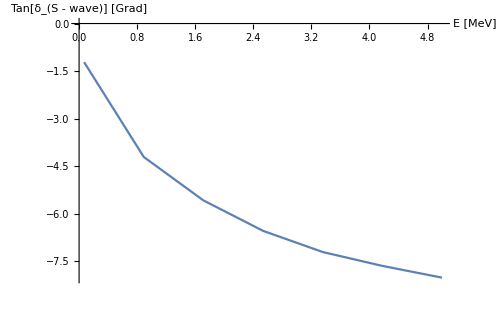
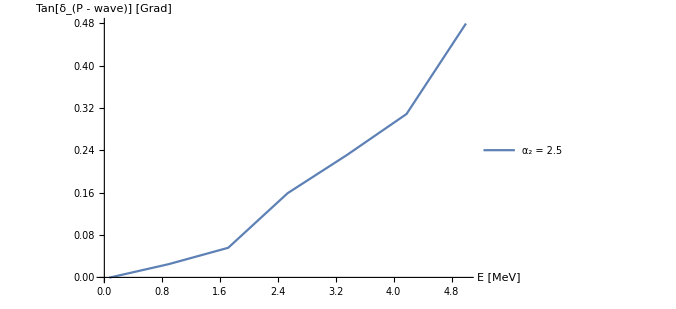
-Graphics- | -Graphics-

```mathematica
tanDsL=Get[LocalObject["tanDsL"]];tanDpL=Get[LocalObject["tanDpL"]];αL=Get[LocalObject["3-1_CorePara_P"]];
cselect=c2Range[[1]];
pLength=Length[a2Range];
Print["Plotting  ϕ_core += c_2×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with c_2=",NumberForm[cselect,nf]];
phaseS=Table[Transpose[{Select[tanDsL,#[[1]]==cselect&][[All,3]][[1]][[All,1]],(180./Pi) ArcTan[Select[tanDsL,#[[1]]==cselect&][[All,3]][[nn]][[All,2]]]}],{nn,pLength}];
phaseP=Table[Transpose[{Select[tanDpL,#[[1]]==cselect&][[All,3]][[1]][[All,1]],(180./Pi) ArcTan[Select[tanDpL,#[[1]]==cselect&][[All,3]][[nn]][[All,2]]]}],{nn,pLength}];
leg="α_2 = "<>ToString[#]&/@a2Range;
Grid[{{ListPlot[phaseS,AxesLabel->{"E [MeV]","Tan[δ_(S - wave)] [Grad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True],
ListPlot[phaseP,AxesLabel->{"E [MeV]","Tan[δ_(P - wave)] [Grad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True,PlotLegends->leg]}}]
```

Plotting  ϕ_core += c_2×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.5000

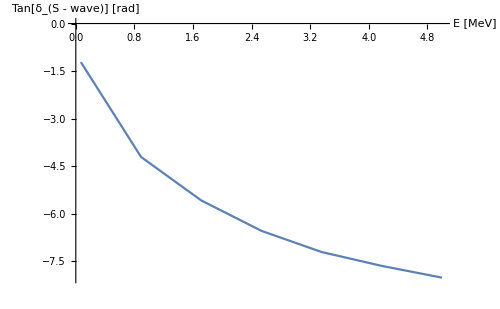
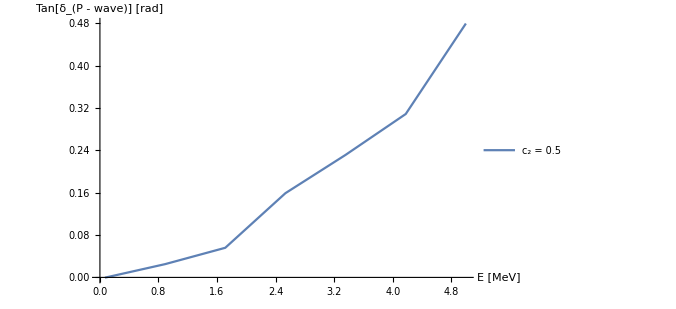
-Graphics- | -Graphics-

```mathematica
aselect=a2Range[[1]];
pLength=Length[c2Range];
Print["Plotting  ϕ_core += c_2×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=",NumberForm[aselect,nf]];
phaseS=Table[Transpose[{Select[tanDsL,#[[2]]==aselect&][[All,3]][[1]][[All,1]],(180./Pi) ArcTan[Select[tanDsL,#[[2]]==aselect&][[All,3]][[nn]][[All,2]]]}],{nn,pLength}];
phaseP=Table[Transpose[{Select[tanDpL,#[[2]]==aselect&][[All,3]][[1]][[All,1]],(180./Pi) ArcTan[Select[tanDpL,#[[2]]==aselect&][[All,3]][[nn]][[All,2]]]}],{nn,pLength}];
leg="c_2 = "<>ToString[#]&/@c2Range;
Grid[{{ListPlot[phaseS,AxesLabel->{"E [MeV]","Tan[δ_(S - wave)] [rad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True],
ListPlot[phaseP,AxesLabel->{"E [MeV]","Tan[δ_(P - wave)] [rad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True,PlotLegends->leg]}}]
```

λ = 16.  c_2 = 0.5000  α_2 = 2.5000:  a_s = 0.427987 fm    r_s = -6.78622 fm        a_p = 0.288589 fm^3     r_p = 330.226 fm

/home/kirscher/kette_repo/31_resonances/code/../data/TwoGaussCore_EREpara.dat

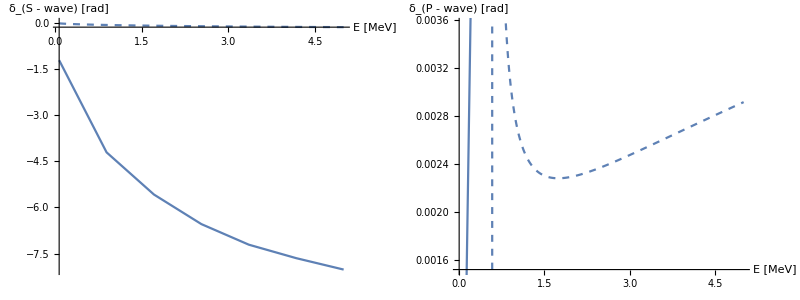

```mathematica
f1=1;f2=5;
exportTab={};
dataTab={};
α1=Select[αL,#[[1]]==λ&][[1]][[2]];
Do[
Lrel = 0;
dataS=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)/Select[tanDsL,#[[2]]==aselect&&#[[1]]==cselect&][[1]][[3]][[All,2]]}];
EreS=Fit[dataS[[f1;;f2]],{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)^3/Select[tanDpL,#[[2]]==aselect&&#[[1]]==cselect&][[1]][[3]][[All,2]]}];
EreP=Fit[dataP[[f1;;f2]],{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;

AppendTo[exportTab,{NumberForm[λ,nf],NumberForm[1.0,nf],NumberForm[α1,nf],NumberForm[cselect,nf],NumberForm[α1 aselect,nf],NumberForm[a0tf,nf],NumberForm[r0tf,nf],NumberForm[a1tf,nf],NumberForm[r1tf,nf]}];
AppendTo[dataTab,{λ,1.0,α1,cselect,α1 aselect,a0tf,r0tf,a1tf,r1tf}];

λ=0.25 activeLEC⟦nn⟧[[1]]^2;
Print["λ = ",λ,"  c_2 = ",NumberForm[cselect,nf],"  α_2 = ",NumberForm[aselect,nf],":  a_s = ",a0tf," fm    r_s = ",r0tf," fm        a_p = ",a1tf," fm^3     r_p = ",r1tf," fm"];
,{aselect,a2Range},{cselect,c2Range}]
Export[NotebookDirectory[]<>"../data/TwoGaussCore_EREpara.dat",exportTab,"Table"]
Grid[{{
Show[Plot[(Sqrt[2 μ ee]/hbar)/(-1./#[[6]]+(#[[7]])/2 (Sqrt[2 μ ee]/hbar)^2)&/@dataTab,{ee,phaseS[[1]][[All,1]][[1]],phaseS[[1]][[All,1]][[-1]]},PlotStyle->Dashed,AxesLabel->{"E [MeV]","δ_(S - wave) [rad]"},ImageSize->500],
ListPlot[phaseS,Joined->True],PlotRange->{Automatic,Automatic}],
Show[Plot[(Sqrt[2 μ ee]/hbar)^3/(-1./#[[8]]+(#[[9]])/2 (Sqrt[2 μ ee]/hbar)^2)&/@dataTab,{ee,phaseP[[1]][[All,1]][[1]],phaseP[[1]][[All,1]][[-1]]},PlotStyle->Dashed,AxesLabel->{"E [MeV]","δ_(P - wave) [rad]"},ImageSize->500,PlotRange->{Automatic,Automatic}],
ListPlot[phaseP,Joined->True]]
}}]
```